## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

### DataToEquations and the critical congestion solver

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];
```

```mathematica
(*using reverseSort simplifyCount*)
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Iterative DNF convertion took 319.396 seconds to terminate

Iterative DNF convertion took 0.877362 seconds to terminate

Iterative DNF convertion took 0.067287 seconds to terminate

Iterative DNF convertion took 0.067017 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18≤jt30≤19

Picked one value for the variable(s) {jt30} {18} (respectively)

{323.212,Null}

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];
```

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

```mathematica
(*using sort simplifyCount*)
Get[dddRicardo]
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

Iterative DNF convertion took 739.781 seconds to terminate

Iterative DNF convertion took 0.274199 seconds to terminate

Iterative DNF convertion took 0.061759 seconds to terminate

Iterative DNF convertion took 0.071944 seconds to terminate

Iterative DNF convertion took 0.000015 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 18≤jt30≤19

Picked one value for the variable(s) {jt30} {18} (respectively)

{740.348,Null}

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

```mathematica
(*using sort only*)
Get[dddRicardo]
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

Iterative DNF convertion took 131.622 seconds to terminate

Iterative DNF convertion took 0.278929 seconds to terminate

Iterative DNF convertion took 0.061162 seconds to terminate

Iterative DNF convertion took 0.064259 seconds to terminate

Iterative DNF convertion took 0.000061 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18≤jt30≤19

Picked one value for the variable(s) {jt30} {18} (respectively)

{132.339,Null}

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

```mathematica
(*no sorting*)
Get[dddRicardo]
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

Iterative DNF convertion took 173.971 seconds to terminate

Iterative DNF convertion took 0.218254 seconds to terminate

Iterative DNF convertion took 0.065158 seconds to terminate

Iterative DNF convertion took 0.073613 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18≤jt30≤19

Picked one value for the variable(s) {jt30} {18} (respectively)

{174.452,Null}

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

```mathematica
(*using sort only second try*)
Get[dddRicardo]
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

Iterative DNF convertion took 134.453 seconds to terminate

Iterative DNF convertion took 0.287803 seconds to terminate

Iterative DNF convertion took 0.061545 seconds to terminate

Iterative DNF convertion took 0.086417 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 18≤jt30≤19

Picked one value for the variable(s) {jt30} {18} (respectively)

{135.032,Null}

All restrictions are True

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {-5.68434×10^-14,-1.13687×10^-13,2.13163×10^-14,-8.52651×10^-14,-9.9476×10^-14,5.32907×10^-15,-8.52651×10^-14,-8.52651×10^-14,1.11022×10^-15,-2.13163×10^-14,-6.39488×10^-14,-2.13163×10^-14,-6.39488×10^-14,-4.26326×10^-14}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 1.13687×10^-13

<|u1→257.,u2→205.,u3→328.,u4→224.,u5→205.,u6→224.,u7→205.,u8→134.,u9→224.,u10→139.,u11→134.,u12→139.,u13→134.,u14→58.,u15→139.,u16→59.,u17→58.,u18→59.,u19→58.,u20→39.,u21→58.,u22→0.,u23→59.,u24→39.,u25→59.,u26→0.,u27→39.,u28→0.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→257.,u36→257.,u37→328.,u38→328.,j1→0.,j2→52.,j3→0.,j4→104.,j5→19.,j6→0.,j7→0.,j8→71.,j9→0.,j10→85.,j11→5.,j12→0.,j13→0.,j14→76.,j15→0.,j16→80.,j17→1.,j18→0.,j19→0.,j20→19.,j21→0.,j22→58.,j23→0.,j24→20.,j25→0.,j26→59.,j27→0.,j28→39.,j29→0.,j30→58.,j31→0.,j32→59.,j33→0.,j34→39.,j35→0.,j36→52.,j37→0.,j38→104.,jt1→0.,jt2→52.,jt3→0.,jt4→104.,jt5→0.,jt6→52.,jt7→0.,jt8→19.,jt9→0.,jt10→0.,jt11→19.,jt12→85.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→71.,jt19→0.,jt20→5.,jt21→0.,jt22→0.,jt23→5.,jt24→80.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→18.,jt31→58.,jt32→0.,jt33→1.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→1.,jt42→20.,jt43→59.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→19.,jt55→0.,jt56→20.,jt57→0.,jt58→0.,jt59→58.,jt60→0.,jt61→59.,jt62→0.,jt63→39.,jt64→0.|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
Get[dddRicardo]
alpha[edge_]:=0.2
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 71.2052 seconds to terminate

Iterative DNF convertion took 0.742791 seconds to terminate

Iterative DNF convertion took 0.064043 seconds to terminate

Iterative DNF convertion took 0.065963 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8862052404961/520000000000≤jt30≤9238378341951/520000000000

Picked one value for the variable(s) {jt30} {8862052404961/520000000000} (respectively)

{45.3711,95.0782,-14.6943,63.4246,76.8172,-2.57022,68.2004,72.0271,0.219014,14.6943,51.0535,15.5986,52.0025,33.1401}
{45.3711,95.0782,-14.2744,62.9805,77.2634,-2.46936,67.6335,72.5948,0.337553,13.5825,51.3994,15.2484,53.1952,31.6249}

Iterative DNF convertion took 61.2271 seconds to terminate

Iterative DNF convertion took 0.531289 seconds to terminate

Iterative DNF convertion took 0.0631 seconds to terminate

Iterative DNF convertion took 0.062746 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8375415201713/520000000000≤jt30≤8662279800547/520000000000

Picked one value for the variable(s) {jt30} {8375415201713/520000000000} (respectively)

{45.3711,95.0782,-14.2744,62.9805,77.2634,-2.46936,67.6335,72.5948,0.337553,13.5825,51.3994,15.2484,53.1952,31.6249}
{45.3711,95.0782,-13.8718,62.5541,77.692,-2.36573,67.0805,73.1489,0.393045,12.5885,51.7384,14.8869,54.2882,30.2179}

Iterative DNF convertion took 60.852 seconds to terminate

Iterative DNF convertion took 0.533347 seconds to terminate

Iterative DNF convertion took 0.068481 seconds to terminate

Iterative DNF convertion took 0.066923 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7906276799849/520000000000≤jt30≤4071951970491/260000000000

Picked one value for the variable(s) {jt30} {7906276799849/520000000000} (respectively)

{45.3711,95.0782,-13.8718,62.5541,77.692,-2.36573,67.0805,73.1489,0.393045,12.5885,51.7384,14.8869,54.2882,30.2179}
{45.3711,95.0782,-13.4865,62.1455,78.1029,-2.26303,66.5459,73.6847,0.414486,11.6979,52.0637,14.5226,55.2936,28.9132}

Iterative DNF convertion took 64.5761 seconds to terminate

Iterative DNF convertion took 0.563486 seconds to terminate

Iterative DNF convertion took 0.065442 seconds to terminate

Iterative DNF convertion took 0.069179 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1492209766279/104000000000≤jt30≤7675428008821/520000000000

Picked one value for the variable(s) {jt30} {1492209766279/104000000000} (respectively)

{45.3711,95.0782,-13.4865,62.1455,78.1029,-2.26303,66.5459,73.6847,0.414486,11.6979,52.0637,14.5226,55.2936,28.9132}
{45.3711,95.0782,-13.1189,61.7551,78.4955,-2.16481,66.0346,74.1974,0.421577,10.8963,52.3684,14.1638,56.2235,27.7051}

Iterative DNF convertion took 140.526 seconds to terminate

Iterative DNF convertion took 0.312693 seconds to terminate

Iterative DNF convertion took 0.070935 seconds to terminate

Iterative DNF convertion took 0.067131 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1408907391683/104000000000≤jt30≤7250135676453/520000000000

Picked one value for the variable(s) {jt30} {1408907391683/104000000000} (respectively)

{45.3711,95.0782,-13.1189,61.7551,78.4955,-2.16481,66.0346,74.1974,0.421577,10.8963,52.3684,14.1638,56.2235,27.7051}
{45.3711,95.0782,-12.7692,61.3833,78.8695,-2.07364,65.55,74.6834,0.423651,10.1717,52.6472,13.8173,57.0884,26.5882}

Iterative DNF convertion took 135.278 seconds to terminate

Iterative DNF convertion took 0.28996 seconds to terminate

Iterative DNF convertion took 0.061333 seconds to terminate

Iterative DNF convertion took 0.06359 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 3329508520589/260000000000≤jt30≤3431483552741/260000000000

Picked one value for the variable(s) {jt30} {3329508520589/260000000000} (respectively)

{45.3711,95.0782,-12.7692,61.3833,78.8695,-2.07364,65.55,74.6834,0.423651,10.1717,52.6472,13.8173,57.0884,26.5882}
{45.3711,95.0782,-12.4375,61.0301,79.225,-1.99068,65.0937,75.1412,0.424001,9.5148,52.8975,13.4866,57.8961,25.5571}

Iterative DNF convertion took 60.3536 seconds to terminate

Iterative DNF convertion took 0.534344 seconds to terminate

Iterative DNF convertion took 0.062501 seconds to terminate

Iterative DNF convertion took 0.067274 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6304679589269/520000000000≤jt30≤1627558671587/130000000000

Picked one value for the variable(s) {jt30} {6304679589269/520000000000} (respectively)

{45.3711,95.0782,-12.4375,61.0301,79.225,-1.99068,65.0937,75.1412,0.424001,9.5148,52.8975,13.4866,57.8961,25.5571}
{45.3711,95.0782,-12.1233,60.695,79.5622,-1.91604,64.6656,75.5709,0.423661,8.91883,53.1188,13.1735,58.652,24.6065}

Iterative DNF convertion took 137.761 seconds to terminate

Iterative DNF convertion took 0.395721 seconds to terminate

Iterative DNF convertion took 0.082163 seconds to terminate

Iterative DNF convertion took 0.078633 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 2990256061249/260000000000≤jt30≤6189080095351/520000000000

Picked one value for the variable(s) {jt30} {2990256061249/260000000000} (respectively)

{45.3711,95.0782,-12.1233,60.695,79.5622,-1.91604,64.6656,75.5709,0.423661,8.91883,53.1188,13.1735,58.652,24.6065}
{45.3711,95.0782,-11.826,60.3777,79.8817,-1.84927,64.2647,75.9734,0.42299,8.37845,53.312,12.8781,59.3602,23.7313}

Iterative DNF convertion took 59.8547 seconds to terminate

Iterative DNF convertion took 0.539991 seconds to terminate

Iterative DNF convertion took 0.063686 seconds to terminate

Iterative DNF convertion took 0.064074 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 218651622891/20000000000≤jt30≤453621854293/40000000000

Picked one value for the variable(s) {jt30} {218651622891/20000000000} (respectively)

{45.3711,95.0782,-11.826,60.3777,79.8817,-1.84927,64.2647,75.9734,0.42299,8.37845,53.312,12.8781,59.3602,23.7313}
{45.3711,95.0782,-11.5451,60.0774,80.1841,-1.78967,63.8895,76.3502,0.422139,7.88915,53.4786,12.6001,60.0238,22.9267}

Iterative DNF convertion took 57.9696 seconds to terminate

Iterative DNF convertion took 0.527069 seconds to terminate

Iterative DNF convertion took 0.060066 seconds to terminate

Iterative DNF convertion took 0.062203 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 5416179732419/520000000000≤jt30≤1408015989769/130000000000

Picked one value for the variable(s) {jt30} {5416179732419/520000000000} (respectively)

{45.3711,95.0782,-11.5451,60.0774,80.1841,-1.78967,63.8895,76.3502,0.422139,7.88915,53.4786,12.6001,60.0238,22.9267}
{45.3711,95.0782,-11.2799,59.7935,80.47,-1.73649,63.5386,76.7027,0.421187,7.44685,53.6203,12.3388,60.6456,22.1879}

Iterative DNF convertion took 127.271 seconds to terminate

Iterative DNF convertion took 0.287946 seconds to terminate

Iterative DNF convertion took 0.064837 seconds to terminate

Iterative DNF convertion took 0.063699 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 258618942649/26000000000≤jt30≤673997862999/65000000000

Picked one value for the variable(s) {jt30} {258618942649/26000000000} (respectively)

{45.3711,95.0782,-11.2799,59.7935,80.47,-1.73649,63.5386,76.7027,0.421187,7.44685,53.6203,12.3388,60.6456,22.1879}
{45.3711,95.0782,-11.0297,59.5254,80.7401,-1.689,63.2104,77.0324,0.420179,7.04775,53.739,12.0935,61.2284,21.5104}

Iterative DNF convertion took 57.8995 seconds to terminate

Iterative DNF convertion took 0.525488 seconds to terminate

Iterative DNF convertion took 0.062393 seconds to terminate

Iterative DNF convertion took 0.063425 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1237928084567/130000000000≤jt30≤2587456798107/260000000000

Picked one value for the variable(s) {jt30} {1237928084567/130000000000} (respectively)

{45.3711,95.0782,-11.0297,59.5254,80.7401,-1.689,63.2104,77.0324,0.420179,7.04775,53.739,12.0935,61.2284,21.5104}
{45.3711,95.0782,-10.7938,59.2723,80.9951,-1.64652,62.9034,77.3409,0.419149,6.68828,53.8365,11.8633,61.7744,20.8898}

Iterative DNF convertion took 127.256 seconds to terminate

Iterative DNF convertion took 0.288324 seconds to terminate

Iterative DNF convertion took 0.058463 seconds to terminate

Iterative DNF convertion took 0.062825 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 297025422851/32500000000≤jt30≤622378137087/65000000000

Picked one value for the variable(s) {jt30} {297025422851/32500000000} (respectively)

{45.3711,95.0782,-10.7938,59.2723,80.9951,-1.64652,62.9034,77.3409,0.419149,6.68828,53.8365,11.8633,61.7744,20.8898}
{45.3711,95.0782,-10.5716,59.0336,81.2357,-1.60845,62.6163,77.6296,0.41812,6.3651,53.9146,11.6477,62.2858,20.3221}

Iterative DNF convertion took 127.972 seconds to terminate

Iterative DNF convertion took 0.284964 seconds to terminate

Iterative DNF convertion took 0.059064 seconds to terminate

Iterative DNF convertion took 0.066891 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4572760066047/520000000000≤jt30≤4802579584449/520000000000

Picked one value for the variable(s) {jt30} {4572760066047/520000000000} (respectively)

{45.3711,95.0782,-10.5716,59.0336,81.2357,-1.60845,62.6163,77.6296,0.41812,6.3651,53.9146,11.6477,62.2858,20.3221}
{45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}

Iterative DNF convertion took 127.795 seconds to terminate

Iterative DNF convertion took 0.288065 seconds to terminate

Iterative DNF convertion took 0.060532 seconds to terminate

Iterative DNF convertion took 0.063322 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 2205575467103/260000000000≤jt30≤1160983163623/130000000000

Picked one value for the variable(s) {jt30} {2205575467103/260000000000} (respectively)

{45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{45.3711,95.0782,-10.1653,58.5964,81.6763,-1.54336,62.096,78.1526,0.416144,5.81513,54.02,11.2568,63.2136,19.3294}

Iterated 15 times out of 15

{1444.61,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.3711,95.0782,-10.1653,58.5964,81.6763,-1.54336,62.096,78.1526,0.416144,5.81513,54.02,11.2568,63.2136,19.3294}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.473763

```mathematica
(*Continuing the previous example but printing the sup norm*)
Get[dddRicardo]
alpha[edge_]:=0.2
nn2=NonLinear[nn];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 57.0324 seconds to terminate

Iterative DNF convertion took 0.572954 seconds to terminate

Iterative DNF convertion took 0.065085 seconds to terminate

Iterative DNF convertion took 0.063528 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2133022062963/260000000000≤jt30≤1125383629983/130000000000

Picked one value for the variable(s) {jt30} {2133022062963/260000000000} (respectively)

{45.3711,95.0782,-10.1653,58.5964,81.6763,-1.54336,62.096,78.1526,0.416144,5.81513,54.02,11.2568,63.2136,19.3294}
{45.3711,95.0782,-9.98002,58.3967,81.8777,-1.51542,61.8606,78.3894,0.415229,5.58259,54.0505,11.0802,63.6338,18.8972}

Max error for non-linear solution: 0.432163

Iterative DNF convertion took 136.019 seconds to terminate

Iterative DNF convertion took 0.304171 seconds to terminate

Iterative DNF convertion took 0.068537 seconds to terminate

Iterative DNF convertion took 0.067365 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1033998344837/130000000000≤jt30≤4373930953461/520000000000

Picked one value for the variable(s) {jt30} {1033998344837/130000000000} (respectively)

{45.3711,95.0782,-9.98002,58.3967,81.8777,-1.51542,61.8606,78.3894,0.415229,5.58259,54.0505,11.0802,63.6338,18.8972}
{45.3711,95.0782,-9.80579,58.2088,82.0672,-1.49004,61.64,78.6113,0.414377,5.37485,54.0684,10.9153,64.0272,18.5034}

Max error for non-linear solution: 0.393881

Iterative DNF convertion took 135.327 seconds to terminate

Iterative DNF convertion took 0.289963 seconds to terminate

Iterative DNF convertion took 0.067719 seconds to terminate

Iterative DNF convertion took 0.0651 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1004910681997/130000000000≤jt30≤425976348461/52000000000

Picked one value for the variable(s) {jt30} {1004910681997/130000000000} (respectively)

{45.3711,95.0782,-9.80579,58.2088,82.0672,-1.49004,61.64,78.6113,0.414377,5.37485,54.0684,10.9153,64.0272,18.5034}
{45.3711,95.0782,-9.642,58.0319,82.2456,-1.46687,61.4333,78.8192,0.413599,5.18953,54.075,10.7615,64.3956,18.1446}

Max error for non-linear solution: 0.368397

Iterative DNF convertion took 59.8922 seconds to terminate

Iterative DNF convertion took 0.532367 seconds to terminate

Iterative DNF convertion took 0.06556 seconds to terminate

Iterative DNF convertion took 0.063585 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 783145314903/104000000000≤jt30≤2078884343129/260000000000

Picked one value for the variable(s) {jt30} {783145314903/104000000000} (respectively)

{45.3711,95.0782,-9.642,58.0319,82.2456,-1.46687,61.4333,78.8192,0.413599,5.18953,54.075,10.7615,64.3956,18.1446}
{45.3711,95.0782,-9.48807,57.8655,82.4135,-1.44564,61.2396,79.0142,0.412899,5.0244,54.0718,10.618,64.7405,17.8182}

Max error for non-linear solution: 0.344926

Iterative DNF convertion took 59.8643 seconds to terminate

Iterative DNF convertion took 0.532226 seconds to terminate

Iterative DNF convertion took 0.06445 seconds to terminate

Iterative DNF convertion took 0.066641 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3823068734827/520000000000≤jt30≤4066776540343/520000000000

Picked one value for the variable(s) {jt30} {3823068734827/520000000000} (respectively)

{45.3711,95.0782,-9.48807,57.8655,82.4135,-1.44564,61.2396,79.0142,0.412899,5.0244,54.0718,10.618,64.7405,17.8182}
{45.3711,95.0782,-9.34345,57.709,82.5713,-1.42608,61.0579,79.197,0.412281,4.87746,54.06,10.4844,65.0635,17.5213}

Max error for non-linear solution: 0.322942

Iterative DNF convertion took 129.361 seconds to terminate

Iterative DNF convertion took 0.286507 seconds to terminate

Iterative DNF convertion took 0.059916 seconds to terminate

Iterative DNF convertion took 0.065483 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 748116120581/104000000000≤jt30≤398570795367/52000000000

Picked one value for the variable(s) {jt30} {748116120581/104000000000} (respectively)

{45.3711,95.0782,-9.34345,57.709,82.5713,-1.42608,61.0579,79.197,0.412281,4.87746,54.06,10.4844,65.0635,17.5213}
{45.3711,95.0782,-9.2076,57.5619,82.7197,-1.40798,60.8873,79.3686,0.411747,4.74685,54.0408,10.36,65.3658,17.2514}

Max error for non-linear solution: 0.302355

Iterative DNF convertion took 58.2746 seconds to terminate

Iterative DNF convertion took 0.526553 seconds to terminate

Iterative DNF convertion took 0.065265 seconds to terminate

Iterative DNF convertion took 0.061695 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 733451713719/104000000000≤jt30≤3913571536779/520000000000

Picked one value for the variable(s) {jt30} {733451713719/104000000000} (respectively)

{45.3711,95.0782,-9.2076,57.5619,82.7197,-1.40798,60.8873,79.3686,0.411747,4.74685,54.0408,10.36,65.3658,17.2514}
{45.3711,95.0782,-9.07999,57.4236,82.8593,-1.39116,60.7273,79.5298,0.411295,4.63088,54.0152,10.2443,65.6489,17.0062}

Max error for non-linear solution: 0.283081

Iterative DNF convertion took 128.682 seconds to terminate

Iterative DNF convertion took 0.286852 seconds to terminate

Iterative DNF convertion took 0.061251 seconds to terminate

Iterative DNF convertion took 0.065198 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3602180815991/520000000000≤jt30≤962364944979/130000000000

Picked one value for the variable(s) {jt30} {3602180815991/520000000000} (respectively)

{45.3711,95.0782,-9.07999,57.4236,82.8593,-1.39116,60.7273,79.5298,0.411295,4.63088,54.0152,10.2443,65.6489,17.0062}
{45.3711,95.0782,-8.96015,57.2936,82.9905,-1.37546,60.5769,79.6811,0.410923,4.52801,53.9843,10.1368,65.9139,16.7835}

Max error for non-linear solution: 0.265039

Iterative DNF convertion took 133.765 seconds to terminate

Iterative DNF convertion took 0.30443 seconds to terminate

Iterative DNF convertion took 0.0643 seconds to terminate

Iterative DNF convertion took 0.065002 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3544503627133/520000000000≤jt30≤3792544765447/520000000000

Picked one value for the variable(s) {jt30} {3544503627133/520000000000} (respectively)

{45.3711,95.0782,-8.96015,57.2936,82.9905,-1.37546,60.5769,79.6811,0.410923,4.52801,53.9843,10.1368,65.9139,16.7835}
{45.3711,95.0782,-8.8476,57.1714,83.1138,-1.36073,60.4356,79.8233,0.410627,4.43685,53.9488,10.0369,66.1621,16.5813}

Max error for non-linear solution: 0.248154

Iterative DNF convertion took 63.6677 seconds to terminate

Iterative DNF convertion took 0.574612 seconds to terminate

Iterative DNF convertion took 0.063073 seconds to terminate

Iterative DNF convertion took 0.065144 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 109170541037/16250000000≤jt30≤3742073553567/520000000000

Picked one value for the variable(s) {jt30} {109170541037/16250000000} (respectively)

{45.3711,95.0782,-8.8476,57.1714,83.1138,-1.36073,60.4356,79.8233,0.410627,4.43685,53.9488,10.0369,66.1621,16.5813}
{45.3711,95.0782,-8.74189,57.0566,83.2297,-1.34688,60.3028,79.9571,0.410402,4.35615,53.9097,9.94421,66.3944,16.3978}

Max error for non-linear solution: 0.232353

Iterative DNF convertion took 131.383 seconds to terminate

Iterative DNF convertion took 0.284155 seconds to terminate

Iterative DNF convertion took 0.060168 seconds to terminate

Iterative DNF convertion took 0.063534 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 1724170943723/260000000000≤jt30≤462170421069/65000000000

Picked one value for the variable(s) {jt30} {1724170943723/260000000000} (respectively)

{45.3711,95.0782,-8.74189,57.0566,83.2297,-1.34688,60.3028,79.9571,0.410402,4.35615,53.9097,9.94421,66.3944,16.3978}
{45.3711,95.0782,-8.64262,56.9486,83.3386,-1.33379,60.1779,80.0829,0.410244,4.28476,53.8675,9.85824,66.612,16.2314}

Max error for non-linear solution: 0.217569

Iterative DNF convertion took 137.797 seconds to terminate

Iterative DNF convertion took 0.291991 seconds to terminate

Iterative DNF convertion took 0.061316 seconds to terminate

Iterative DNF convertion took 0.064308 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 852130646353/130000000000≤jt30≤3657796697987/520000000000

Picked one value for the variable(s) {jt30} {852130646353/130000000000} (respectively)

{45.3711,95.0782,-8.64262,56.9486,83.3386,-1.33379,60.1779,80.0829,0.410244,4.28476,53.8675,9.85824,66.612,16.2314}
{45.3711,95.0782,-8.54938,56.8472,83.441,-1.32139,60.0603,80.2013,0.410144,4.22167,53.8231,9.77854,66.8158,16.0804}

Max error for non-linear solution: 0.203738

Iterative DNF convertion took 131.286 seconds to terminate

Iterative DNF convertion took 0.285786 seconds to terminate

Iterative DNF convertion took 0.060147 seconds to terminate

Iterative DNF convertion took 0.065942 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3373425325813/520000000000≤jt30≤3622816402867/520000000000

Picked one value for the variable(s) {jt30} {3373425325813/520000000000} (respectively)

{45.3711,95.0782,-8.54938,56.8472,83.441,-1.32139,60.0603,80.2013,0.410144,4.22167,53.8231,9.77854,66.8158,16.0804}
{45.3711,95.0782,-8.4618,56.7518,83.5373,-1.30962,59.9496,80.3128,0.410098,4.16596,53.7769,9.7047,67.0066,15.9434}

Max error for non-linear solution: 0.190799

Iterative DNF convertion took 64.3844 seconds to terminate

Iterative DNF convertion took 0.663923 seconds to terminate

Iterative DNF convertion took 0.138774 seconds to terminate

Iterative DNF convertion took 0.077471 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 0.000014 seconds to terminate

MFGSS: Multiple solutions: 1671266096183/260000000000≤jt30≤1795960458949/260000000000

Picked one value for the variable(s) {jt30} {1671266096183/260000000000} (respectively)

{45.3711,95.0782,-8.4618,56.7518,83.5373,-1.30962,59.9496,80.3128,0.410098,4.16596,53.7769,9.7047,67.0066,15.9434}
{45.3711,95.0782,-8.37952,56.6622,83.6278,-1.2984,59.8454,80.4177,0.410099,4.11681,53.7294,9.63631,67.1852,15.8192}

Max error for non-linear solution: 0.178694

Iterative DNF convertion took 60.4466 seconds to terminate

Iterative DNF convertion took 0.529082 seconds to terminate

Iterative DNF convertion took 0.06071 seconds to terminate

Iterative DNF convertion took 0.062915 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 41442212547/6500000000≤jt30≤71293192119/10400000000

Picked one value for the variable(s) {jt30} {41442212547/6500000000} (respectively)

{45.3711,95.0782,-8.37952,56.6622,83.6278,-1.2984,59.8454,80.4177,0.410099,4.11681,53.7294,9.63631,67.1852,15.8192}
{45.3711,95.0782,-8.30222,56.5779,83.7129,-1.28771,59.7472,80.5167,0.410141,4.07348,53.6811,9.573,67.3526,15.7066}

Max error for non-linear solution: 0.167372

Iterated 15 times out of 15

{1514.6,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.3711,95.0782,-10.1653,58.5964,81.6763,-1.54336,62.096,78.1526,0.416144,5.81513,54.02,11.2568,63.2136,19.3294}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.473763

```mathematica
(*Continuing the previous example but printing the sup norm*)
Get[dddRicardo]
alpha[edge_]:=0.2
nn3=NonLinear[nn2];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative DNF convertion took 60.0718 seconds to terminate

Iterative DNF convertion took 0.538221 seconds to terminate

Iterative DNF convertion took 0.063687 seconds to terminate

Iterative DNF convertion took 0.064791 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 1645770512583/260000000000≤jt30≤708125662883/104000000000

Picked one value for the variable(s) {jt30} {1645770512583/260000000000} (respectively)

{45.3711,95.0782,-8.30222,56.5779,83.7129,-1.28771,59.7472,80.5167,0.410141,4.07348,53.6811,9.573,67.3526,15.7066}
{45.3711,95.0782,-8.22958,56.4987,83.7928,-1.27748,59.6547,80.6099,0.410218,4.03532,53.6323,9.51442,67.5094,15.6045}

Max error for non-linear solution: 0.156781

Iterative DNF convertion took 141.79 seconds to terminate

Iterative DNF convertion took 0.324765 seconds to terminate

Iterative DNF convertion took 0.070528 seconds to terminate

Iterative DNF convertion took 0.076881 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 408831107829/65000000000≤jt30≤351946516781/52000000000

Picked one value for the variable(s) {jt30} {408831107829/65000000000} (respectively)

{45.3711,95.0782,-8.22958,56.4987,83.7928,-1.27748,59.6547,80.6099,0.410218,4.03532,53.6323,9.51442,67.5094,15.6045}
{45.3711,95.0782,-8.16132,56.4242,83.8681,-1.2677,59.5674,80.6978,0.410324,4.00173,53.5835,9.46024,67.6563,15.5118}

Max error for non-linear solution: 0.146874

Iterative DNF convertion took 71.2964 seconds to terminate

Iterative DNF convertion took 0.608693 seconds to terminate

Iterative DNF convertion took 0.07736 seconds to terminate

Iterative DNF convertion took 0.084198 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 0.000016 seconds to terminate

MFGSS: Multiple solutions: 81309114251/13000000000≤jt30≤875211654563/130000000000

Picked one value for the variable(s) {jt30} {81309114251/13000000000} (respectively)

{45.3711,95.0782,-8.16132,56.4242,83.8681,-1.2677,59.5674,80.6978,0.410324,4.00173,53.5835,9.46024,67.6563,15.5118}
{45.3711,95.0782,-8.09715,56.3542,83.9388,-1.25834,59.4851,80.7807,0.410455,3.97221,53.5349,9.41013,67.7939,15.4279}

Max error for non-linear solution: 0.137608

Iterative DNF convertion took 142.374 seconds to terminate

Iterative DNF convertion took 0.297767 seconds to terminate

Iterative DNF convertion took 0.065685 seconds to terminate

Iterative DNF convertion took 0.068314 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 809096997199/130000000000≤jt30≤217780235403/32500000000

Picked one value for the variable(s) {jt30} {809096997199/130000000000} (respectively)

{45.3711,95.0782,-8.09715,56.3542,83.9388,-1.25834,59.4851,80.7807,0.410455,3.97221,53.5349,9.41013,67.7939,15.4279}
{45.3711,95.0782,-8.03682,56.2883,84.0054,-1.24936,59.4075,80.8589,0.410606,3.94628,53.4866,9.3638,67.9228,15.3517}

Max error for non-linear solution: 0.128939

Iterative DNF convertion took 139.927 seconds to terminate

Iterative DNF convertion took 0.297431 seconds to terminate

Iterative DNF convertion took 0.064841 seconds to terminate

Iterative DNF convertion took 0.064647 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1611225665633/260000000000≤jt30≤138804758253/20800000000

Picked one value for the variable(s) {jt30} {1611225665633/260000000000} (respectively)

{45.3711,95.0782,-8.03682,56.2883,84.0054,-1.24936,59.4075,80.8589,0.410606,3.94628,53.4866,9.3638,67.9228,15.3517}
{45.3711,95.0782,-7.9801,56.2263,84.068,-1.24076,59.3343,80.9327,0.410772,3.92353,53.4391,9.32098,68.0437,15.2827}

Max error for non-linear solution: 0.120831

Iterative DNF convertion took 61.8569 seconds to terminate

Iterative DNF convertion took 0.447156 seconds to terminate

Iterative DNF convertion took 0.064472 seconds to terminate

Iterative DNF convertion took 0.066543 seconds to terminate

Iterative DNF convertion took 0.000016 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3210316012833/520000000000≤jt30≤216095165099/32500000000

Picked one value for the variable(s) {jt30} {3210316012833/520000000000} (respectively)

{45.3711,95.0782,-7.9801,56.2263,84.068,-1.24076,59.3343,80.9327,0.410772,3.92353,53.4391,9.32098,68.0437,15.2827}
{45.3711,95.0782,-7.92674,56.168,84.1269,-1.23251,59.2651,81.0024,0.410951,3.90359,53.3923,9.28141,68.1569,15.22}

Max error for non-linear solution: 0.113245

Iterative DNF convertion took 133.653 seconds to terminate

Iterative DNF convertion took 0.288736 seconds to terminate

Iterative DNF convertion took 0.063434 seconds to terminate

Iterative DNF convertion took 0.068477 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 199985608167/32500000000≤jt30≤3446490515891/520000000000

Picked one value for the variable(s) {jt30} {199985608167/32500000000} (respectively)

{45.3711,95.0782,-7.92674,56.168,84.1269,-1.23251,59.2651,81.0024,0.410951,3.90359,53.3923,9.28141,68.1569,15.22}
{45.3711,95.0782,-7.87656,56.1131,84.1823,-1.2246,59.1999,81.0681,0.411138,3.88613,53.3465,9.24485,68.263,15.1632}

Max error for non-linear solution: 0.106148

Iterative DNF convertion took 60.6262 seconds to terminate

Iterative DNF convertion took 0.537901 seconds to terminate

Iterative DNF convertion took 0.062944 seconds to terminate

Iterative DNF convertion took 0.064857 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 49853496629/8125000000≤jt30≤429605112047/65000000000

Picked one value for the variable(s) {jt30} {49853496629/8125000000} (respectively)

{45.3711,95.0782,-7.87656,56.1131,84.1823,-1.2246,59.1999,81.0681,0.411138,3.88613,53.3465,9.24485,68.263,15.1632}
{45.3711,95.0782,-7.82934,56.0614,84.2345,-1.21701,59.1383,81.1302,0.411331,3.87086,53.3018,9.21107,68.3626,15.1117}

Max error for non-linear solution: 0.0995087

Iterative DNF convertion took 134.207 seconds to terminate

Iterative DNF convertion took 0.297836 seconds to terminate

Iterative DNF convertion took 0.072976 seconds to terminate

Iterative DNF convertion took 0.067791 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3182710627907/520000000000≤jt30≤857103086679/130000000000

Picked one value for the variable(s) {jt30} {3182710627907/520000000000} (respectively)

{45.3711,95.0782,-7.82934,56.0614,84.2345,-1.21701,59.1383,81.1302,0.411331,3.87086,53.3018,9.21107,68.3626,15.1117}
{45.3711,95.0782,-7.7849,56.0128,84.2836,-1.20974,59.0801,81.1888,0.411528,3.85754,53.2582,9.17986,68.4559,15.0649}

Max error for non-linear solution: 0.093296

Iterative DNF convertion took 136.334 seconds to terminate

Iterative DNF convertion took 0.290088 seconds to terminate

Iterative DNF convertion took 0.065021 seconds to terminate

Iterative DNF convertion took 0.068337 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1587940822213/260000000000≤jt30≤427632690623/65000000000

Picked one value for the variable(s) {jt30} {1587940822213/260000000000} (respectively)

{45.3711,95.0782,-7.7849,56.0128,84.2836,-1.20974,59.0801,81.1888,0.411528,3.85754,53.2582,9.17986,68.4559,15.0649}
{45.3711,95.0782,-7.74307,55.967,84.3299,-1.20277,59.0252,81.2442,0.411727,3.84591,53.2159,9.15104,68.5433,15.0225}

Max error for non-linear solution: 0.0874824

Iterative DNF convertion took 60.5172 seconds to terminate

Iterative DNF convertion took 0.532956 seconds to terminate

Iterative DNF convertion took 0.062182 seconds to terminate

Iterative DNF convertion took 0.06404 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3170005126799/520000000000≤jt30≤3414661240689/520000000000

Picked one value for the variable(s) {jt30} {3170005126799/520000000000} (respectively)

{45.3711,95.0782,-7.74307,55.967,84.3299,-1.20277,59.0252,81.2442,0.411727,3.84591,53.2159,9.15104,68.5433,15.0225}
{45.3711,95.0782,-7.70369,55.9238,84.3735,-1.19609,58.9733,81.2965,0.411925,3.8358,53.1749,9.12441,68.6254,14.9839}

Max error for non-linear solution: 0.0820418

Iterative DNF convertion took 60.5545 seconds to terminate

Iterative DNF convertion took 0.536915 seconds to terminate

Iterative DNF convertion took 0.062723 seconds to terminate

Iterative DNF convertion took 0.072401 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 791241113513/130000000000≤jt30≤1704549352367/260000000000

Picked one value for the variable(s) {jt30} {791241113513/130000000000} (respectively)

{45.3711,95.0782,-7.70369,55.9238,84.3735,-1.19609,58.9733,81.2965,0.411925,3.8358,53.1749,9.12441,68.6254,14.9839}
{45.3711,95.0782,-7.66662,55.8832,84.4145,-1.18969,58.9243,81.3459,0.412121,3.82701,53.1353,9.09982,68.7023,14.949}

Max error for non-linear solution: 0.0769496

Iterative DNF convertion took 60.4982 seconds to terminate

Iterative DNF convertion took 0.539337 seconds to terminate

Iterative DNF convertion took 0.065827 seconds to terminate

Iterative DNF convertion took 0.065314 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 3160656447327/520000000000≤jt30≤85106848923/13000000000

Picked one value for the variable(s) {jt30} {3160656447327/520000000000} (respectively)

{45.3711,95.0782,-7.66662,55.8832,84.4145,-1.18969,58.9243,81.3459,0.412121,3.82701,53.1353,9.09982,68.7023,14.949}
{45.3711,95.0782,-7.6317,55.8449,84.4532,-1.18357,58.878,81.3925,0.412315,3.81939,53.097,9.0771,68.7745,14.9172}

Max error for non-linear solution: 0.0721831

Iterative DNF convertion took 135.872 seconds to terminate

Iterative DNF convertion took 0.293095 seconds to terminate

Iterative DNF convertion took 0.063473 seconds to terminate

Iterative DNF convertion took 0.069808 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3156989891383/520000000000≤jt30≤3400098455313/520000000000

Picked one value for the variable(s) {jt30} {3156989891383/520000000000} (respectively)

{45.3711,95.0782,-7.6317,55.8449,84.4532,-1.18357,58.878,81.3925,0.412315,3.81939,53.097,9.0771,68.7745,14.9172}
{45.3711,95.0782,-7.59881,55.8089,84.4896,-1.17772,58.8342,81.4366,0.412504,3.81279,53.06,9.05612,68.8422,14.8883}

Max error for non-linear solution: 0.0677209

Iterative DNF convertion took 134.059 seconds to terminate

Iterative DNF convertion took 0.290841 seconds to terminate

Iterative DNF convertion took 0.05639 seconds to terminate

Iterative DNF convertion took 0.057359 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1576942104119/260000000000≤jt30≤3396493813179/520000000000

Picked one value for the variable(s) {jt30} {1576942104119/260000000000} (respectively)

{45.3711,95.0782,-7.59881,55.8089,84.4896,-1.17772,58.8342,81.4366,0.412504,3.81279,53.06,9.05612,68.8422,14.8883}
{45.3711,95.0782,-7.56782,55.7749,84.5239,-1.17212,58.7929,81.4783,0.412689,3.8071,53.0245,9.03673,68.9058,14.8621}

Max error for non-linear solution: 0.063543

Iterated 15 times out of 15

{1561.53,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.3711,95.0782,-10.1653,58.5964,81.6763,-1.54336,62.096,78.1526,0.416144,5.81513,54.02,11.2568,63.2136,19.3294}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.473763

Iterative boolean convert took 159.323 seconds to terminate

Iterative boolean convert took 0.623975 seconds to terminate

Iterative boolean convert took 0.590477 seconds to terminate

Iterative boolean convert took 0.042511 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt30==(126076584035067+5200000000000 (-126076584035067/5200000000000+jt30))/5200000000000&&5073875508519/208000000000-jt30==(5073875508519-208000000000 jt30)/208000000000&&126076584035067/5200000000000≤jt30≤5073875508519/208000000000

Picked one for the variable(s) {jt30}

Iterative boolean convert took 142.016 seconds to terminate

Iterative boolean convert took 0.624258 seconds to terminate

Iterative boolean convert took 0.581708 seconds to terminate

Iterative boolean convert took 0.048187 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt30==(2980803401547+208000000000 (-2980803401547/208000000000+jt30))/208000000000&&20407457178833/1300000000000-jt30==(20407457178833-1300000000000 jt30)/1300000000000&&2980803401547/208000000000≤jt30≤20407457178833/1300000000000

Picked one for the variable(s) {jt30}

Iterative boolean convert took 173.437 seconds to terminate

Iterative boolean convert took 0.445585 seconds to terminate

Iterative boolean convert took 0.355802 seconds to terminate

Iterative boolean convert took 0.055716 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt42==(133387815099311-5200000000000 (133387815099311/5200000000000-jt42))/5200000000000&&130513506717313/5200000000000≤jt42≤133387815099311/5200000000000

Picked one for the variable(s) {jt42}

Iterative boolean convert took 143.253 seconds to terminate

Iterative boolean convert took 0.644752 seconds to terminate

Iterative boolean convert took 0.58285 seconds to terminate

Iterative boolean convert took 0.043988 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt30==(6498026426923+1300000000000 (-6498026426923/1300000000000+jt30))/1300000000000&&38624680277337/5200000000000-jt30==(38624680277337-5200000000000 jt30)/5200000000000&&6498026426923/1300000000000≤jt30≤38624680277337/5200000000000

Picked one for the variable(s) {jt30}

Iterative boolean convert took 173.438 seconds to terminate

Iterative boolean convert took 0.441692 seconds to terminate

Iterative boolean convert took 0.348497 seconds to terminate

Iterative boolean convert took 0.055142 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: jt42==(81058885057187-2600000000000 (81058885057187/2600000000000-jt42))/2600000000000&&148819509586229/5200000000000≤jt42≤81058885057187/2600000000000

Picked one for the variable(s) {jt42}

Iterative boolean convert took 113.254 seconds to terminate

Iterative boolean convert took 0.68818 seconds to terminate

Iterative boolean convert took 0.228879 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Iterative boolean convert took 215.835 seconds to terminate

Iterative boolean convert took 0.494333 seconds to terminate

Iterative boolean convert took 0.147232 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 74.9398 seconds to terminate

Iterative boolean convert took 0.508065 seconds to terminate

Iterative boolean convert took 0.417723 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 57741880260029/2600000000000≤jt32≤24619845589513/650000000000

Picked one for the variable(s) {jt32}

Iterative boolean convert took 235.887 seconds to terminate

Iterative boolean convert took 0.4433 seconds to terminate

Iterative boolean convert took 0.246364 seconds to terminate

Iterative boolean convert took 6.×10^-6 seconds to terminate

Iterative boolean convert took 63.6685 seconds to terminate

Iterative boolean convert took 0.416909 seconds to terminate

Iterative boolean convert took 0.221692 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 234.79 seconds to terminate

Iterative boolean convert took 0.668626 seconds to terminate

Iterative boolean convert took 0.407618 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Iterative boolean convert took 63.142 seconds to terminate

Iterative boolean convert took 0.442194 seconds to terminate

Iterative boolean convert took 0.217028 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 235.266 seconds to terminate

Iterative boolean convert took 0.779117 seconds to terminate

Iterative boolean convert took 0.424019 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Iterative boolean convert took 65.6732 seconds to terminate

Iterative boolean convert took 0.44306 seconds to terminate

Iterative boolean convert took 0.229494 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Iterative boolean convert took 241.805 seconds to terminate

Iterative boolean convert took 0.701468 seconds to terminate

Iterative boolean convert took 0.450542 seconds to terminate

Iterative boolean convert took 7.×10^-6 seconds to terminate

Iterated 15 times out of 15

{2360.72,Null}

EqEntryIn: j36==52&&j38==104	True

EqValueAuxiliaryEdges: u35==u36&&u37==u38&&u29==u30&&u31==u32&&u33==u34	True

EqCompCon: (jt1==0||1000000-u1+u36==0)&&(jt2==0||u1-u36==0)&&(jt3==0||1000000-u3+u38==0)&&(jt4==0||u3-u38==0)&&(jt5==0||-u2+u5==0)&&(jt6==0||-u2+u7==0)&&(jt7==0||u2-u5==0)&&(jt8==0||-u5+u7==0)&&(jt9==0||u2-u7==0)&&(jt10==0||u5-u7==0)&&(jt11==0||-u4+u6==0)&&(jt12==0||-u4+u9==0)&&(jt13==0||u4-u6==0)&&(jt14==0||-u6+u9==0)&&(jt15==0||u4-u9==0)&&(jt16==0||u6-u9==0)&&(jt17==0||u11-u8==0)&&(jt18==0||u13-u8==0)&&(jt19==0||-u11+u8==0)&&(jt20==0||-u11+u13==0)&&(jt21==0||-u13+u8==0)&&(jt22==0||u11-u13==0)&&(jt23==0||-u10+u12==0)&&(jt24==0||-u10+u15==0)&&(jt25==0||u10-u12==0)&&(jt26==0||-u12+u15==0)&&(jt27==0||u10-u15==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u14+u17==0)&&(jt30==0||-u14+u19==0)&&(jt31==0||-u14+u21==0)&&(jt32==0||u14-u17==0)&&(jt33==0||-u17+u19==0)&&(jt34==0||-u17+u21==0)&&(jt35==0||u14-u19==0)&&(jt36==0||u17-u19==0)&&(jt37==0||-u19+u21==0)&&(jt38==0||u14-u21==0)&&(jt39==0||u17-u21==0)&&(jt40==0||u19-u21==0)&&(jt41==0||-u16+u18==0)&&(jt42==0||-u16+u23==0)&&(jt43==0||-u16+u25==0)&&(jt44==0||u16-u18==0)&&(jt45==0||-u18+u23==0)&&(jt46==0||-u18+u25==0)&&(jt47==0||u16-u23==0)&&(jt48==0||u18-u23==0)&&(jt49==0||-u23+u25==0)&&(jt50==0||u16-u25==0)&&(jt51==0||u18-u25==0)&&(jt52==0||u23-u25==0)&&(jt53==0||-u20+u24==0)&&(jt54==0||-u20+u27==0)&&(jt55==0||u20-u24==0)&&(jt56==0||-u24+u27==0)&&(jt57==0||u20-u27==0)&&(jt58==0||u24-u27==0)&&(jt59==0||-u22+u29==0)&&(jt60==0||1000000+u22-u29==0)&&(jt61==0||-u26+u31==0)&&(jt62==0||1000000+u26-u31==0)&&(jt63==0||-u28+u33==0)&&(jt64==0||1000000+u28-u33==0)	True

EqBalanceSplittingCurrents: j1==jt1&&j36==jt2&&j3==jt3&&j38==jt4&&j2==jt5+jt6&&j5==jt7+jt8&&j7==jt10+jt9&&j4==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j8==jt17+jt18&&j11==jt19+jt20&&j13==jt21+jt22&&j10==jt23+jt24&&j12==jt25+jt26&&j15==jt27+jt28&&j14==jt29+jt30+jt31&&j17==jt32+jt33+jt34&&j19==jt35+jt36+jt37&&j21==jt38+jt39+jt40&&j16==jt41+jt42+jt43&&j18==jt44+jt45+jt46&&j23==jt47+jt48+jt49&&j25==jt50+jt51+jt52&&j20==jt53+jt54&&j24==jt55+jt56&&j27==jt57+jt58&&j22==jt59&&j29==jt60&&j26==jt61&&j31==jt62&&j28==jt63&&j33==jt64	True

EqCurrentCompCon: (j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0)	True

EqTransitionCompCon: (jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt13==0)&&(jt12==0||jt15==0)&&(jt14==0||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt21==0)&&(jt20==0||jt22==0)&&(jt23==0||jt25==0)&&(jt24==0||jt27==0)&&(jt26==0||jt28==0)&&(jt29==0||jt32==0)&&(jt3==0||jt4==0)&&(jt30==0||jt35==0)&&(jt31==0||jt38==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(jt37==0||jt40==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt43==0||jt50==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(jt49==0||jt52==0)&&(jt5==0||jt7==0)&&(jt53==0||jt55==0)&&(jt54==0||jt57==0)&&(jt56==0||jt58==0)&&(jt59==0||jt60==0)&&(jt6==0||jt9==0)&&(jt61==0||jt62==0)&&(jt63==0||jt64==0)	True

EqPosJs: j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0	True

EqPosJts: jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0	True

EqSwitchingByVertex: u1≤1000000+u36&&u36≤u1&&u3≤1000000+u38&&u38≤u3&&u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5&&u4≤u6&&u4≤u9&&u6≤u4&&u6≤u9&&u9≤u4&&u9≤u6&&u8≤u11&&u8≤u13&&u11≤u8&&u11≤u13&&u13≤u8&&u13≤u11&&u10≤u12&&u10≤u15&&u12≤u10&&u12≤u15&&u15≤u10&&u15≤u12&&u14≤u17&&u14≤u19&&u14≤u21&&u17≤u14&&u17≤u19&&u17≤u21&&u19≤u14&&u19≤u17&&u19≤u21&&u21≤u14&&u21≤u17&&u21≤u19&&u16≤u18&&u16≤u23&&u16≤u25&&u18≤u16&&u18≤u23&&u18≤u25&&u23≤u16&&u23≤u18&&u23≤u25&&u25≤u16&&u25≤u18&&u25≤u23&&u20≤u24&&u20≤u27&&u24≤u20&&u24≤u27&&u27≤u20&&u27≤u24&&u22≤u29&&u29≤1000000+u22&&u26≤u31&&u31≤1000000+u26&&u28≤u33&&u33≤1000000+u28	True

Nlhs: {-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}	{-63.8483,-166.281,-1.68731×10^6,1.68654×10^6,-1.68885×10^6,161863.,1.37358×10^6,-1.37579×10^6,1.02374×10^6,197385.,0.,-197385.,-287.647,0.}

Nrhs: {-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->4],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,3->5],j10-j9-IntM[j10-j9,4->6],-j11+j12-IntM[-j11+j12,5->6],-j13+j14-IntM[-j13+j14,5->7],-j15+j16-IntM[-j15+j16,6->8],-j17+j18-IntM[-j17+j18,7->8],-j19+j20-IntM[-j19+j20,7->9],-j21+j22-IntM[-j21+j22,7->10],-j23+j24-IntM[-j23+j24,8->9],-j25+j26-IntM[-j25+j26,8->11],-j27+j28-IntM[-j27+j28,9->12]}	{-63.8483,-166.281,3.5154×10^7,-3.51553×10^7,3.51512×10^7,-3.803×10^6,-2.81385×10^7,2.81346×10^7,-2.19877×10^7,-3.4081×10^6,-287.647,3.4081×10^6,0.,0.}

Max error for non-linear solution: 3.68419×10^7

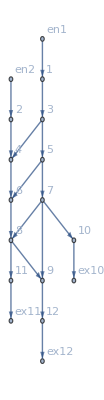

```mathematica
d2e["FG"]
```

### TIGRAN

#### large costs: 10^6

```mathematica
d2e["FG"]
```

-Graphics-

```mathematica
critNoSplt["jtvars"]
```

<|{1,1->3,en1->1}→jt1,{1,en1->1,1->3}→jt2,{2,2->4,en2->2}→jt3,{2,en2->2,2->4}→jt4,{3,1->3,3->4}→jt5,{3,1->3,3->5}→jt6,{3,3->4,1->3}→jt7,{3,3->4,3->5}→jt8,{3,3->5,1->3}→jt9,{3,3->5,3->4}→jt10,{4,2->4,3->4}→jt11,{4,2->4,4->6}→jt12,{4,3->4,2->4}→jt13,{4,3->4,4->6}→jt14,{4,4->6,2->4}→jt15,{4,4->6,3->4}→jt16,{5,3->5,5->6}→jt17,{5,3->5,5->7}→jt18,{5,5->6,3->5}→jt19,{5,5->6,5->7}→jt20,{5,5->7,3->5}→jt21,{5,5->7,5->6}→jt22,{6,4->6,5->6}→jt23,{6,4->6,6->8}→jt24,{6,5->6,4->6}→jt25,{6,5->6,6->8}→jt26,{6,6->8,4->6}→jt27,{6,6->8,5->6}→jt28,{7,5->7,7->8}→jt29,{7,5->7,7->9}→jt30,{7,5->7,7->10}→jt31,{7,7->8,5->7}→jt32,{7,7->8,7->9}→jt33,{7,7->8,7->10}→jt34,{7,7->9,5->7}→jt35,{7,7->9,7->8}→jt36,{7,7->9,7->10}→jt37,{7,7->10,5->7}→jt38,{7,7->10,7->8}→jt39,{7,7->10,7->9}→jt40,{8,6->8,7->8}→jt41,{8,6->8,8->9}→jt42,{8,6->8,8->11}→jt43,{8,7->8,6->8}→jt44,{8,7->8,8->9}→jt45,{8,7->8,8->11}→jt46,{8,8->9,6->8}→jt47,{8,8->9,7->8}→jt48,{8,8->9,8->11}→jt49,{8,8->11,6->8}→jt50,{8,8->11,7->8}→jt51,{8,8->11,8->9}→jt52,{9,7->9,8->9}→jt53,{9,7->9,9->12}→jt54,{9,8->9,7->9}→jt55,{9,8->9,9->12}→jt56,{9,9->12,7->9}→jt57,{9,9->12,8->9}→jt58,{10,7->10,10->ex10}→jt59,{10,10->ex10,7->10}→jt60,{11,8->11,11->ex11}→jt61,{11,11->ex11,8->11}→jt62,{12,9->12,12->ex12}→jt63,{12,12->ex12,9->12}→jt64|>

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{
{5,7,9,4001},{10,7,9,4001},{8,7,9,4001},
{11,8,9,4001},{6,8,9,4001},{7,8,9,4001}(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critNoSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1005000≤8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤-5000&&-25000≤21 jt10-21 jt17-21 jt18+jt27+jt28+jt32+jt33+jt34-jt41-jt42-jt44-jt45+jt49-u1≤975000&&-1022000≤24 jt10-22 jt17-22 jt18-2 jt19+2 jt22+jt27+jt28-2 jt29-2 jt30+jt32+jt33+3 jt34+2 jt37-jt41-jt42-jt44-jt45+jt49+u19≤-22000&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-2000≤5 jt10-5 jt17-5 jt18+u1-u19≤2001&&20000≤-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001},(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||25000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt49==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||20000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt42==0||24001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(jt10+jt22==jt19+jt32||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt37==0||2000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt33==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt30==0||5 jt10+u1==2001+5 jt17+5 jt18+u19)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 219.435 seconds to terminate

Simplifying :
{{True,True},(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&-3001≤u19≤0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&3001+u19==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&-3001≤u19≤0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&3001+u19==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==4000&&3001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&3001+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&jt10==0&&jt11==0&&jt27==0&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)}

Iterative DNF convertion took 2.06022 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)}

Iterative DNF convertion took 0.717492 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&-3001≤u19≤0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==-3001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==4000&&u19==0)}

Iterative DNF convertion took 0.056643 seconds to terminate

Simplifying :
{{True,-3001≤u19≤0},True}

Iterative DNF convertion took 0.00001 seconds to terminate

Simplifying :
{{True,-3001≤u19≤0},True}

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -3001≤u19≤0

Picked one value for the variable(s) {u19} {-2974} (respectively)

{223.302,Null}

```mathematica
critNoSplt["AssoCritical"]
```

<|u1→4000,u2→3000,u3→4000,u4→3000,u5→3000,u6→3000,u7→3000,u8→2000,u9→3000,u10→2000,u11→2000,u12→2000,u13→2000,u14→1000,u15→2000,u16→1000,u17→1000,u18→1000,u19→-2974,u20→-2974,u21→1000,u22→0,u23→-2974,u24→-2974,u25→1000,u26→0,u27→-2974,u28→-2974,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→4000,u36→4000,u37→4000,u38→4000,j1→0,j2→1000,j3→0,j4→1000,j5→0,j6→0,j7→0,j8→1000,j9→0,j10→1000,j11→0,j12→0,j13→0,j14→1000,j15→0,j16→1000,j17→0,j18→0,j19→0,j20→0,j21→0,j22→1000,j23→0,j24→0,j25→0,j26→1000,j27→0,j28→0,j29→0,j30→1000,j31→0,j32→1000,j33→0,j34→0,j35→0,j36→1000,j37→0,j38→1000,jt1→0,jt2→1000,jt3→0,jt4→1000,jt5→0,jt6→1000,jt7→0,jt8→0,jt9→0,jt10→0,jt11→0,jt12→1000,jt13→0,jt14→0,jt15→0,jt16→0,jt17→0,jt18→1000,jt19→0,jt20→0,jt21→0,jt22→0,jt23→0,jt24→1000,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→0,jt31→1000,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→0,jt42→0,jt43→1000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→0,jt56→0,jt57→0,jt58→0,jt59→1000,jt60→0,jt61→1000,jt62→0,jt63→0,jt64→0|>

```mathematica
crit["jvars"]/.crit["AssoCritical"]
```

<|{1,1->3}→0,{3,1->3}→1000,{2,2->4}→0,{4,2->4}→1000,{3,3->4}→0,{4,3->4}→0,{3,3->5}→0,{5,3->5}→1000,{4,4->6}→0,{6,4->6}→1000,{5,5->6}→0,{6,5->6}→0,{5,5->7}→0,{7,5->7}→1000,{6,6->8}→0,{8,6->8}→1000,{7,7->8}→0,{8,7->8}→0,{7,7->9}→0,{9,7->9}→0,{7,7->10}→0,{10,7->10}→1000,{8,8->9}→0,{9,8->9}→0,{8,8->11}→0,{11,8->11}→1000,{9,9->12}→0,{12,9->12}→0,{10,10->ex10}→0,{ex10,10->ex10}→1000,{11,11->ex11}→0,{ex11,11->ex11}→1000,{12,12->ex12}→0,{ex12,12->ex12}→0,{en1,en1->1}→0,{1,en1->1}→1000,{en2,en2->2}→0,{2,en2->2}→1000|>

```mathematica
{B,K,cost,vars}=GetKirchhoffMatrix[critNoSplt]
```

{SparseArray[…],SparseArray[…],Function[currents$,MapThread[#1[#2]&,{KeyMap[Join[jvars$9524986,jtvars$9524986]][CostArgs$9524986]/@vars$9524986,currents$}]],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}

```mathematica
vars
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}

```mathematica
cost[vars]
```

{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,0,0,0,0,0,j4,j5,j6,j7,j8,j9,1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1/1000000,1000000,1/1000000,1000000,1/1000000,1000000,1/1000000,1/1000000,1/1000000}

```mathematica
Get[dddRicardo]

Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Iterative DNF convertion took 391.2 seconds to terminate

Iterative DNF convertion took 5.99267 seconds to terminate

Iterative DNF convertion took 4.60787 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

{403.404,Null}

```mathematica
Get[dddRicardo]
(*this has large but not infinity costs on entrance and exits*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
```

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11000+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt29&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45≥22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33&&-1000000≤5000+8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤0&&-953000≤-44 jt10+43 jt17+43 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤47000&&-1000000≤46000+52 jt10-49 jt17-49 jt18-3 jt19+3 jt22-3 jt29-3 jt30+3 jt34+3 jt37+u1≤0&&jt10+jt22≥jt19+jt32&&5000+4 jt10+jt27+jt28≥4 jt17+4 jt18+jt41+jt42&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&3000+3 jt10+jt19≤4 jt17+3 jt18+jt22&&3000+3 jt10+jt28≤4 jt17+3 jt18+jt22&&5000+4 jt10+jt16+jt28≥5 jt17+4 jt18+jt22&&2000+jt10+jt16≥jt17+jt18&&11000+11 jt10+jt32+jt33+jt34≥11 jt17+11 jt18+jt44+jt45&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&35 jt10+2 (16500+jt22+jt34+jt37)≤33 jt17+33 jt18+2 (jt19+jt29+jt30)&&11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37≤11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48&&22 jt17+22 jt18+jt19+jt27+jt28+jt29+2 jt30+jt32+2 jt33≥22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48},(35 jt10+2 (16500+jt22+jt34+jt37)==33 jt17+33 jt18+2 (jt19+jt29+jt30)||46000+52 jt10+3 jt22+3 jt34+3 jt37+u1==49 jt17+49 jt18+3 (jt19+jt29+jt30))&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(38000+38 jt10+jt22+jt34+jt37==37 jt17+37 jt18+jt19+jt29+jt30||47000+44 jt10+jt22+jt34+jt37==43 jt17+43 jt18+jt19+jt29+jt30+u1)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45+jt47+jt48==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(22000+23 jt10+jt22+jt37+jt41+jt42+jt44+jt45==22 jt17+22 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||5000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11 (jt17+jt18)==11000+11 jt10+jt32+jt33+jt34)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt27+jt28==0||4 (jt17+jt18)==5000+4 jt10+jt27+jt28)&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 103.818 seconds to terminate

Simplifying :
{{True,True},(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&u1==3750&&jt30==250&&jt42==250)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt30==250+jt34&&jt32==0&&jt30+jt33==250&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt44==0&&jt32==0&&jt42==250&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt44==0&&jt32==0&&jt42==250&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt30==250&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt42==250&&u1==3750)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt30==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30+jt33==250&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==250+jt34&&jt37==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750&&jt30==250)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt30==250+jt34&&jt32==0&&jt30+jt33==250&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt29==0&&jt42==250&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt42+jt45==250&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==250&&jt44==0&&jt42+jt45==250&&jt47==0&&jt48==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt44==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt44==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&u1==3750)||(jt29==0&&jt41==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt45==0&&jt47==0&&jt41+jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt42==250&&jt44==0&&u1==3750)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt41+jt42==250&&jt45==0&&jt47==0&&jt48==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt44==0&&u1==3750&&jt41==0&&jt29==0)||(jt29==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt29==0&&jt16==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt17==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt29==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt33==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt29==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt34==0&&jt29==jt37&&jt44==0&&jt45==0&&jt48==0&&jt47==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==250&&jt32==0&&jt41==0&&jt42==250&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)}

Iterative DNF convertion took 0.805282 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==250&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==250&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&u1==3750)}

Iterative DNF convertion took 0.590852 seconds to terminate

Simplifying :
{{True,True},True}

Iterative DNF convertion took 4.×10^-6 seconds to terminate

{105.851,Null}

```mathematica
Get[dddRicardo]
(*infinity costs at entrance and exit*)
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1},{7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9},{7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
d2e=Data2Equations[Data/.{I1->1000,I2->1000,U1->0,U2->0,U3->0}];
critSplt=CriticalCongestionSolver[d2e];//AbsoluteTiming
"Iterative DNF convertion took "107.29792" seconds to terminate"
"Iterative DNF convertion took "0.770732" seconds to terminate"
"Iterative DNF convertion took "0.583327" seconds to terminate"
"Iterative DNF convertion took "5.*^-6" seconds to terminate"
{109.240226,Null}
critSplt["AssoCritical"]
<|u1->3750,u2->2750,u3->3750,u4->2750,u5->2750,u6->2750,u7->2750,u8->1750,u9->2750,u10->1750,u11->1750,u12->1750,u13->1750,u14->750,u15->1750,u16->750,u17->750,u18->750,u19->750,u20->500,u21->750,u22->0,u23->750,u24->500,u25->750,u26->0,u27->500,u28->0,u29->0,u30->0,u31->0,u32->0,u33->0,u34->0,u35->3750,u36->3750,u37->3750,u38->3750,j1->0,j2->1000,j3->0,j4->1000,j5->0,j6->0,j7->0,j8->1000,j9->0,j10->1000,j11->0,j12->0,j13->0,j14->1000,j15->0,j16->1000,j17->0,j18->0,j19->0,j20->250,j21->0,j22->750,j23->0,j24->250,j25->0,j26->750,j27->0,j28->500,j29->0,j30->750,j31->0,j32->750,j33->0,j34->500,j35->0,j36->1000,j37->0,j38->1000,jt1->0,jt2->1000,jt3->0,jt4->1000,jt5->0,jt6->1000,jt7->0,jt8->0,jt9->0,jt10->0,jt11->0,jt12->1000,jt13->0,jt14->0,jt15->0,jt16->0,jt17->0,jt18->1000,jt19->0,jt20->0,jt21->0,jt22->0,jt23->0,jt24->1000,jt25->0,jt26->0,jt27->0,jt28->0,jt29->0,jt30->250,jt31->750,jt32->0,jt33->0,jt34->0,jt35->0,jt36->0,jt37->0,jt38->0,jt39->0,jt40->0,jt41->0,jt42->250,jt43->750,jt44->0,jt45->0,jt46->0,jt47->0,jt48->0,jt49->0,jt50->0,jt51->0,jt52->0,jt53->0,jt54->250,jt55->0,jt56->250,jt57->0,jt58->0,jt59->750,jt60->0,jt61->750,jt62->0,jt63->500,jt64->0|>
GetKirchhoffMatrix[critSplt]
{SparseArray[…],SparseArray[…],Function[currents$,MapThread[#1[#2]&,{KeyMap[Join[jvars$5539288,jtvars$5539288]][CostArgs$5539288]/@vars$5539288,currents$}]],{j1,j10,j11,j12,j13,j14,j15,j16,j17,j18,j19,j2,j20,j21,j22,j23,j24,j25,j26,j27,j28,j3,j30,j32,j34,j36,j38,j4,j5,j6,j7,j8,j9,jt1,jt10,jt11,jt12,jt13,jt14,jt15,jt16,jt17,jt18,jt19,jt2,jt20,jt21,jt22,jt23,jt24,jt25,jt26,jt27,jt28,jt29,jt3,jt30,jt31,jt32,jt33,jt34,jt35,jt36,jt37,jt38,jt39,jt4,jt40,jt41,jt42,jt43,jt44,jt45,jt46,jt47,jt48,jt49,jt5,jt50,jt51,jt52,jt53,jt54,jt55,jt56,jt57,jt58,jt59,jt6,jt60,jt61,jt62,jt63,jt64,jt7,jt8,jt9}}
```

```mathematica
alpha[x_]:=1;
NonLinear[critNoSplt]
```

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1013000≤8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤-13000&&-17000≤21 jt10-21 jt17-21 jt18+jt27+jt28+jt32+jt33+jt34-jt41-jt42-jt44-jt45+jt49-u1≤983000&&-1022000≤24 jt10-22 jt17-22 jt18-2 jt19+2 jt22+jt27+jt28-2 jt29-2 jt30+jt32+jt33+3 jt34+2 jt37-jt41-jt42-jt44-jt45+jt49+u19≤-22000&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-8000≤5 jt10-5 jt17-5 jt18+u1-u19≤-3999&&20000≤6000-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001},(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||17000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||13000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt49==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt42==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11000+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(jt10+jt22==jt19+jt32||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt37==0||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt33==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt30==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt27+jt28==0||5000+4 jt10+jt27+jt28==4 (jt17+jt18))&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 205.416 seconds to terminate

Simplifying :
{{True,True},(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&-5001≤u19≤-1000)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt44==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)}

Iterative DNF convertion took 3.19833 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.905726 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.048229 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 5.×10^-6 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 3.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -5001≤u19≤-1000

Picked one value for the variable(s) {u19} {-4974} (respectively)

Max error for non-linear solution: 1.13687×10^-12

Simplifying :
{{True,jt10≥0&&0≤jt11≤1000&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt10≥jt19&&jt22≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&4 jt17+4 jt18+jt22≥3000+3 jt10+jt19+jt29+jt30&&jt32≥0&&jt33≥0&&jt34≥0&&11 jt17+11 jt18+jt29≤11000+11 jt10+jt32+jt33+jt34&&jt37≥0&&jt41≥0&&jt42≥0&&jt44≥0&&jt45≥0&&jt47≥0&&jt48≥0&&jt49≥0&&-1013000≤8 jt10-9 jt17-9 jt18+jt19-jt22+jt29+jt30-jt34-jt37+u1≤-13000&&-17000≤21 jt10-21 jt17-21 jt18+jt27+jt28+jt32+jt33+jt34-jt41-jt42-jt44-jt45+jt49-u1≤983000&&-1022000≤24 jt10-22 jt17-22 jt18-2 jt19+2 jt22+jt27+jt28-2 jt29-2 jt30+jt32+jt33+3 jt34+2 jt37-jt41-jt42-jt44-jt45+jt49+u19≤-22000&&jt10+jt22≥jt19+jt32&&4 jt17+4 jt18+jt41+jt42≤5000+4 jt10+jt27+jt28&&jt17+jt18≤1000+jt11+jt16&&jt11+jt16≤jt17+jt18&&jt16≥jt27&&jt16≤jt17+jt22+jt27&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt19&&4 jt17+3 jt18+jt22≥3000+3 jt10+jt28&&5 jt17+4 jt18+jt22≤5000+4 jt10+jt16+jt28&&2000+jt10+jt16≥jt17+jt18&&11 jt17+11 jt18+jt44+jt45≤11000+11 jt10+jt32+jt33+jt34&&jt27+jt28≥jt44+jt47&&jt32+jt33+jt34≥jt41+jt48&&jt27+jt28+jt32+jt33+jt34≤jt41+jt44+jt47+jt48&&11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45≥11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49&&11 jt17+11 jt18+jt19+jt29+jt41+jt42+jt44+jt45+jt47+jt48≥11000+12 jt10+jt22+jt27+jt28+jt32+2 jt33+2 jt34+jt37&&jt30+jt33≥jt47+jt48+jt49&&-8000≤5 jt10-5 jt17-5 jt18+u1-u19≤-3999&&20000≤6000-18 jt10+17 jt17+17 jt18+jt19-jt22+jt27+jt28+jt29+jt30+jt32+jt33-jt37-jt41-jt42-jt44-jt45+jt49+u1-u19≤24001},(11000+12 jt10+jt22+jt27+jt28+jt32+jt33+2 jt34+jt37+jt49==11 jt17+11 jt18+jt19+jt29+jt30+jt41+jt42+jt44+jt45||22000+24 jt10+2 jt22+jt27+jt28+jt32+jt33+3 jt34+2 jt37+jt49+u19==22 jt17+22 jt18+2 jt19+2 jt29+2 jt30+jt41+jt42+jt44+jt45)&&(16000+15 jt10+jt27+jt28+jt32+jt33+jt34+jt49==15 jt17+15 jt18+jt41+jt42+jt44+jt45||17000+21 jt10+jt27+jt28+jt32+jt33+jt34+jt49==21 jt17+21 jt18+jt41+jt42+jt44+jt45+u1)&&(jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(3000+3 jt10+jt19+jt29+jt30==4 jt17+4 jt18+jt22+jt34+jt37||13000+8 jt10+jt19+jt29+jt30+u1==9 jt17+9 jt18+jt22+jt34+jt37)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt49==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt48==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt47==0||14000+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt45==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(jt42==0||18001+18 jt10+jt22+jt37+jt41+jt42+jt44+jt45+u19==17 jt17+17 jt18+jt19+jt27+jt28+jt29+jt30+jt32+jt33+jt49+u1)&&(11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt44+jt45||jt32+jt33+jt34==jt41+jt48)&&(jt47+jt48+jt49==0||11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29)&&(11000+12 jt10+jt22+jt33+jt34+jt37==11 jt17+11 jt18+jt19+jt29||jt30+jt33==0)&&(jt33==0||11000+11 jt10+jt32+jt33+jt34==11 jt17+11 jt18+jt29)&&(5000+4 jt10+jt27+jt28==4 jt17+4 jt18+jt41+jt42||jt27+jt28==jt44+jt47)&&(jt32+jt33+jt34==0||11000+11 jt10+jt32+jt33+jt34==11 (jt17+jt18))&&(jt10+jt22==jt19+jt32||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt10+jt22==jt19||3000+3 jt10+jt19==4 jt17+4 jt18+jt22)&&(5000+4 jt10+jt16+jt28==5 jt17+4 jt18+jt22||jt27==0)&&(3000+3 jt10==4 jt17+3 jt18+jt22||jt17+jt22==0)&&(jt37==0||8000+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt33==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt30==0||3999+5 jt10+u1==5 jt17+5 jt18+u19)&&(jt27+jt28==0||5000+4 jt10+jt27+jt28==4 (jt17+jt18))&&(3000+3 jt10+jt28==4 jt17+3 jt18+jt22||jt16==jt27)&&(3000+3 jt10+jt19==4 jt17+3 jt18+jt22||jt22==0)&&(jt47+jt48+jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt42+jt44+jt45+jt47+jt48)&&(jt11+jt16==0||1000+jt10+jt11+jt16==jt17+jt18)&&(jt49==0||jt27+jt28+jt32+jt33+jt34==jt41+jt44+jt47+jt48)&&(1000+jt10+jt11+jt16==jt17+jt18||jt16==0)&&(jt16==0||2000+jt10+jt16==jt17+jt18)&&(jt30==0||jt10+jt22==jt19+jt32)&&(jt16==jt17+jt22+jt27||jt28==0)&&(jt10==0||jt17+jt18==0)&&(jt10==0||jt11+jt16==0)&&(jt45==0||jt48==0)&&(jt42==0||jt47==0)&&(jt41==0||jt44==0)&&(jt29==0||jt32==0)&&(jt18==0||jt10==jt19)&&(jt17==0||jt19==0)}

Iterative DNF convertion took 205.436 seconds to terminate

Simplifying :
{{True,True},(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&-5001≤u19≤-1000)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt30==0&&jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt44==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt45==0&&jt41==jt49&&jt32==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt42==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt41==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt44==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt45==0&&jt41==jt49&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41+jt42==0&&jt44==0&&jt45==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt47==0&&jt48==0&&jt49==0&&jt41==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt42==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt33==0&&jt32+jt34==0&&jt32==jt37&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30==0&&jt49==0&&1000+u19==0&&jt32==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30+jt33==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&jt30==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt32==0&&jt30==jt34&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&jt10==0&&jt11==0&&jt27==0&&jt30+jt33==0&&jt49==0&&5001+u19==0&&jt30==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41+jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt42+jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt32==jt37&&jt33==0&&jt32+jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt30==jt34&&jt32==0&&jt30+jt33==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt44==jt49&&jt45==0&&jt44+jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt41==jt49&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt41+jt48==0&&4000+u1==0&&1000+u19==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt29==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt28==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&1000+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt42==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&4000+u1==0&&5001+u19==0&&jt10==0&&jt11==0&&jt27==0&&jt49==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&5001+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt29==jt37&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&4000+u1==0&&1000+u19==0)}

Iterative DNF convertion took 3.12396 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.868602 seconds to terminate

Simplifying :
{{True,True},(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&-5001≤u19≤-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-1000)||(jt10==0&&jt11==0&&jt16==0&&jt17==0&&jt18==1000&&jt19==0&&jt22==0&&jt27==0&&jt28==0&&jt29==0&&jt30==0&&jt32==0&&jt33==0&&jt34==0&&jt37==0&&jt41==0&&jt42==0&&jt44==0&&jt45==0&&jt47==0&&jt48==0&&jt49==0&&u1==-4000&&u19==-5001)}

Iterative DNF convertion took 0.061149 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 6.×10^-6 seconds to terminate

Simplifying :
{{True,-5001≤u19≤-1000},True}

Iterative DNF convertion took 4.×10^-6 seconds to terminate

MFGSS: Multiple solutions: -5001≤u19≤-1000

Picked one value for the variable(s) {u19} {-4974} (respectively)

Max error for non-linear solution: 1.13687×10^-12

Iterated 2 times out of 15

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12},63,AssoNonCritical→<|u1→-4000,u2→-3000,u3→-4000,u4→-3000,u5→-3000,u6→-3000,u7→-3000,u8→-2000,u9→-3000,u10→-2000,u11→-2000,u12→-2000,u13→-2000,u14→-1000,u15→-2000,u16→-1000,u17→-1000,u18→-1000,u19→-4974,u20→-4974,u21→-1000,u22→0,u23→-4974,u24→-4974,u25→-1000,u26→0,u27→-4974,u28→-4974,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→-4000,u36→-4000,u37→-4000,u38→-4000,j1→0,62,jt26→0,jt27→0,jt28→0,jt29→0,jt30→0,jt31→1000,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→0,jt42→0,jt43→1000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→0,jt56→0,jt57→0,jt58→0,jt59→1000,jt60→0,jt61→1000,jt62→0,jt63→0,jt64→0|>|>
 |  |  |  |

```mathematica
critNoSplt["AssoCritical"]
```

<|u1→4000,u2→3000,u3→4000,u4→3000,u5→3000,u6→3000,u7→3000,u8→2000,u9→3000,u10→2000,u11→2000,u12→2000,u13→2000,u14→1000,u15→2000,u16→1000,u17→1000,u18→1000,u19→-2974,u20→-2974,u21→1000,u22→0,u23→-2974,u24→-2974,u25→1000,u26→0,u27→-2974,u28→-2974,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→4000,u36→4000,u37→4000,u38→4000,j1→0,j2→1000,j3→0,j4→1000,j5→0,j6→0,j7→0,j8→1000,j9→0,j10→1000,j11→0,j12→0,j13→0,j14→1000,j15→0,j16→1000,j17→0,j18→0,j19→0,j20→0,j21→0,j22→1000,j23→0,j24→0,j25→0,j26→1000,j27→0,j28→0,j29→0,j30→1000,j31→0,j32→1000,j33→0,j34→0,j35→0,j36→1000,j37→0,j38→1000,jt1→0,jt2→1000,jt3→0,jt4→1000,jt5→0,jt6→1000,jt7→0,jt8→0,jt9→0,jt10→0,jt11→0,jt12→1000,jt13→0,jt14→0,jt15→0,jt16→0,jt17→0,jt18→1000,jt19→0,jt20→0,jt21→0,jt22→0,jt23→0,jt24→1000,jt25→0,jt26→0,jt27→0,jt28→0,jt29→0,jt30→0,jt31→1000,jt32→0,jt33→0,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→0,jt42→0,jt43→1000,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→0,jt55→0,jt56→0,jt57→0,jt58→0,jt59→1000,jt60→0,jt61→1000,jt62→0,jt63→0,jt64→0|>

```mathematica
Get[dddRicardo]
alpha[x_]:=1;
IsNonLinearSolution[critNoSplt][critNoSplt["AssoCritical"]]
```

EqEntryIn: True
j36==1000&&j38==1000

EqValueAuxiliaryEdges: True
u35==u36&&u37==u38&&u29==u30&&u31==u32&&u33==u34

EqCompCon: True
(jt1==0||1000000-u1+u36==0)&&(jt2==0||u1-u36==0)&&(jt3==0||1000000-u3+u38==0)&&(jt4==0||u3-u38==0)&&(jt5==0||-u2+u5==0)&&(jt6==0||-u2+u7==0)&&(jt7==0||u2-u5==0)&&(jt8==0||-u5+u7==0)&&(jt9==0||u2-u7==0)&&(jt10==0||u5-u7==0)&&(jt11==0||-u4+u6==0)&&(jt12==0||-u4+u9==0)&&(jt13==0||u4-u6==0)&&(jt14==0||-u6+u9==0)&&(jt15==0||u4-u9==0)&&(jt16==0||u6-u9==0)&&(jt17==0||u11-u8==0)&&(jt18==0||u13-u8==0)&&(jt19==0||-u11+u8==0)&&(jt20==0||-u11+u13==0)&&(jt21==0||-u13+u8==0)&&(jt22==0||u11-u13==0)&&(jt23==0||-u10+u12==0)&&(jt24==0||-u10+u15==0)&&(jt25==0||u10-u12==0)&&(jt26==0||-u12+u15==0)&&(jt27==0||u10-u15==0)&&(jt28==0||u12-u15==0)&&(jt29==0||-u14+u17==0)&&(jt30==0||4001-u14+u19==0)&&(jt31==0||-u14+u21==0)&&(jt32==0||u14-u17==0)&&(jt33==0||4001-u17+u19==0)&&(jt34==0||-u17+u21==0)&&(jt35==0||u14-u19==0)&&(jt36==0||u17-u19==0)&&(jt37==0||-u19+u21==0)&&(jt38==0||u14-u21==0)&&(jt39==0||u17-u21==0)&&(jt40==0||4001+u19-u21==0)&&(jt41==0||-u16+u18==0)&&(jt42==0||4001-u16+u23==0)&&(jt43==0||-u16+u25==0)&&(jt44==0||u16-u18==0)&&(jt45==0||4001-u18+u23==0)&&(jt46==0||-u18+u25==0)&&(jt47==0||u16-u23==0)&&(jt48==0||u18-u23==0)&&(jt49==0||-u23+u25==0)&&(jt50==0||u16-u25==0)&&(jt51==0||u18-u25==0)&&(jt52==0||4001+u23-u25==0)&&(jt53==0||-u20+u24==0)&&(jt54==0||-u20+u27==0)&&(jt55==0||u20-u24==0)&&(jt56==0||-u24+u27==0)&&(jt57==0||u20-u27==0)&&(jt58==0||u24-u27==0)&&(jt59==0||-u22+u29==0)&&(jt60==0||1000000+u22-u29==0)&&(jt61==0||-u26+u31==0)&&(jt62==0||1000000+u26-u31==0)&&(jt63==0||-u28+u33==0)&&(jt64==0||1000000+u28-u33==0)

EqBalanceSplittingCurrents: True
j1==jt1&&j36==jt2&&j3==jt3&&j38==jt4&&j2==jt5+jt6&&j5==jt7+jt8&&j7==jt10+jt9&&j4==jt11+jt12&&j6==jt13+jt14&&j9==jt15+jt16&&j8==jt17+jt18&&j11==jt19+jt20&&j13==jt21+jt22&&j10==jt23+jt24&&j12==jt25+jt26&&j15==jt27+jt28&&j14==jt29+jt30+jt31&&j17==jt32+jt33+jt34&&j19==jt35+jt36+jt37&&j21==jt38+jt39+jt40&&j16==jt41+jt42+jt43&&j18==jt44+jt45+jt46&&j23==jt47+jt48+jt49&&j25==jt50+jt51+jt52&&j20==jt53+jt54&&j24==jt55+jt56&&j27==jt57+jt58&&j22==jt59&&j29==jt60&&j26==jt61&&j31==jt62&&j28==jt63&&j33==jt64

EqCurrentCompCon: True
(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)&&(j27==0||j28==0)&&(j29==0||j30==0)&&(j31==0||j32==0)&&(j33==0||j34==0)&&(j35==0||j36==0)&&(j37==0||j38==0)

EqTransitionCompCon: True
(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt13==0)&&(jt12==0||jt15==0)&&(jt14==0||jt16==0)&&(jt17==0||jt19==0)&&(jt18==0||jt21==0)&&(jt20==0||jt22==0)&&(jt23==0||jt25==0)&&(jt24==0||jt27==0)&&(jt26==0||jt28==0)&&(jt29==0||jt32==0)&&(jt3==0||jt4==0)&&(jt30==0||jt35==0)&&(jt31==0||jt38==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(jt37==0||jt40==0)&&(jt41==0||jt44==0)&&(jt42==0||jt47==0)&&(jt43==0||jt50==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(jt49==0||jt52==0)&&(jt5==0||jt7==0)&&(jt53==0||jt55==0)&&(jt54==0||jt57==0)&&(jt56==0||jt58==0)&&(jt59==0||jt60==0)&&(jt6==0||jt9==0)&&(jt61==0||jt62==0)&&(jt63==0||jt64==0)

EqPosJs: True
j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0&&j27≥0&&j28≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j35≥0&&j36≥0&&j37≥0&&j38≥0

EqPosJts: True
jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0&&jt33≥0&&jt34≥0&&jt35≥0&&jt36≥0&&jt37≥0&&jt38≥0&&jt39≥0&&jt40≥0&&jt41≥0&&jt42≥0&&jt43≥0&&jt44≥0&&jt45≥0&&jt46≥0&&jt47≥0&&jt48≥0&&jt49≥0&&jt50≥0&&jt51≥0&&jt52≥0&&jt53≥0&&jt54≥0&&jt55≥0&&jt56≥0&&jt57≥0&&jt58≥0&&jt59≥0&&jt60≥0&&jt61≥0&&jt62≥0&&jt63≥0&&jt64≥0

EqSwitchingByVertex: True
u1≤1000000+u36&&u36≤u1&&u3≤1000000+u38&&u38≤u3&&u2≤u5&&u2≤u7&&u5≤u2&&u5≤u7&&u7≤u2&&u7≤u5&&u4≤u6&&u4≤u9&&u6≤u4&&u6≤u9&&u9≤u4&&u9≤u6&&u8≤u11&&u8≤u13&&u11≤u8&&u11≤u13&&u13≤u8&&u13≤u11&&u10≤u12&&u10≤u15&&u12≤u10&&u12≤u15&&u15≤u10&&u15≤u12&&u14≤u17&&u14≤4001+u19&&u14≤u21&&u17≤u14&&u17≤4001+u19&&u17≤u21&&u19≤u14&&u19≤u17&&u19≤u21&&u21≤u14&&u21≤u17&&u21≤4001+u19&&u16≤u18&&u16≤4001+u23&&u16≤u25&&u18≤u16&&u18≤4001+u23&&u18≤u25&&u23≤u16&&u23≤u18&&u23≤u25&&u25≤u16&&u25≤u18&&u25≤4001+u23&&u20≤u24&&u20≤u27&&u24≤u20&&u24≤u27&&u27≤u20&&u27≤u24&&u22≤u29&&u29≤1000000+u22&&u26≤u31&&u31≤1000000+u26&&u28≤u33&&u33≤1000000+u28

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {2000.,2000.,0.,2000.,2000.,0.,2000.,2000.,0.,0.,2000.,0.,2000.,0.}
{-j1+j2+IntM[-j1+j2,1->3],-j3+j4+IntM[-j3+j4,2->4],-j5+j6+IntM[-j5+j6,3->4],-j7+j8+IntM[-j7+j8,3->5],j10-j9+IntM[j10-j9,4->6],-j11+j12+IntM[-j11+j12,5->6],-j13+j14+IntM[-j13+j14,5->7],-j15+j16+IntM[-j15+j16,6->8],-j17+j18+IntM[-j17+j18,7->8],-j19+j20+IntM[-j19+j20,7->9],-j21+j22+IntM[-j21+j22,7->10],-j23+j24+IntM[-j23+j24,8->9],-j25+j26+IntM[-j25+j26,8->11],-j27+j28+IntM[-j27+j28,9->12]}

Max error for non-linear solution: 2000.

<|u1→4000.,u2→3000.,u3→4000.,u4→3000.,u5→3000.,u6→3000.,u7→3000.,u8→2000.,u9→3000.,u10→2000.,u11→2000.,u12→2000.,u13→2000.,u14→1000.,u15→2000.,u16→1000.,u17→1000.,u18→1000.,u19→-2974.,u20→-2974.,u21→1000.,u22→0.,u23→-2974.,u24→-2974.,u25→1000.,u26→0.,u27→-2974.,u28→-2974.,u29→0.,u30→0.,u31→0.,u32→0.,u33→0.,u34→0.,u35→4000.,u36→4000.,u37→4000.,u38→4000.,j1→0.,j2→1000.,j3→0.,j4→1000.,j5→0.,j6→0.,j7→0.,j8→1000.,j9→0.,j10→1000.,j11→0.,j12→0.,j13→0.,j14→1000.,j15→0.,j16→1000.,j17→0.,j18→0.,j19→0.,j20→0.,j21→0.,j22→1000.,j23→0.,j24→0.,j25→0.,j26→1000.,j27→0.,j28→0.,j29→0.,j30→1000.,j31→0.,j32→1000.,j33→0.,j34→0.,j35→0.,j36→1000.,j37→0.,j38→1000.,jt1→0.,jt2→1000.,jt3→0.,jt4→1000.,jt5→0.,jt6→1000.,jt7→0.,jt8→0.,jt9→0.,jt10→0.,jt11→0.,jt12→1000.,jt13→0.,jt14→0.,jt15→0.,jt16→0.,jt17→0.,jt18→1000.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→1000.,jt25→0.,jt26→0.,jt27→0.,jt28→0.,jt29→0.,jt30→0.,jt31→1000.,jt32→0.,jt33→0.,jt34→0.,jt35→0.,jt36→0.,jt37→0.,jt38→0.,jt39→0.,jt40→0.,jt41→0.,jt42→0.,jt43→1000.,jt44→0.,jt45→0.,jt46→0.,jt47→0.,jt48→0.,jt49→0.,jt50→0.,jt51→0.,jt52→0.,jt53→0.,jt54→0.,jt55→0.,jt56→0.,jt57→0.,jt58→0.,jt59→1000.,jt60→0.,jt61→1000.,jt62→0.,jt63→0.,jt64→0.|>

```mathematica
d2eNS=Data2Equations[d2e];
```

```mathematica
d2eNS["Nrhs"]
```

{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

```mathematica
d2eNS["Nlhs"]
```

{-j1+j2+u1-u2,-j3+j4+u3-u4,-j5+j6+u5-u6,-j7+j8+u7-u8,j10-j9-u10+u9,-j11+j12+u11-u12,-j13+j14+u13-u14,-j15+j16+u15-u16,-j17+j18+u17-u18,-j19+j20+u19-u20,-j21+j22+u21-u22,-j23+j24+u23-u24,-j25+j26+u25-u26,-j27+j28+u27-u28}

```mathematica
Get[dddRicardo]
```

### decreasing the alpha to 0.2

```mathematica
crit
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10,11,12},62,AssoCritical→<|u1→257,u2→205,u3→328,u4→224,u5→205,u6→224,u7→205,u8→134,u9→224,u10→139,u11→134,u12→139,u13→134,u14→58,u15→139,u16→59,u17→58,u18→59,u19→58,u20→39,u21→58,u22→0,u23→59,u24→39,u25→59,u26→0,u27→39,u28→0,u29→0,u30→0,u31→0,u32→0,u33→0,u34→0,u35→257,u36→257,68,jt29→0,jt30→18,jt31→58,jt32→0,jt33→1,jt34→0,jt35→0,jt36→0,jt37→0,jt38→0,jt39→0,jt40→0,jt41→1,jt42→20,jt43→59,jt44→0,jt45→0,jt46→0,jt47→0,jt48→0,jt49→0,jt50→0,jt51→0,jt52→0,jt53→0,jt54→19,jt55→0,jt56→20,jt57→0,jt58→0,jt59→58,jt60→0,jt61→59,jt62→0,jt63→39,jt64→0|>|>
 |  |  |  |

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
(*d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];*)
alpha[edge_]:=0.9
nnn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.8
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.7
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.6
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.5
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.4
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.3
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.2
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
```

Iterative DNF convertion took 135.768 seconds to terminate

Iterative DNF convertion took 0.33828 seconds to terminate

Iterative DNF convertion took 0.074673 seconds to terminate

Iterative DNF convertion took 0.084576 seconds to terminate

Iterative DNF convertion took 0.000014 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

MFGSS: Multiple solutions: 684170814791/40000000000≤jt30≤726434483601/40000000000

Picked one value for the variable(s) {jt30} {684170814791/40000000000} (respectively)

{15.11,34.9331,-4.1645,22.1029,27.4561,-0.566607,23.9976,25.5274,0.0335578,4.1645,17.2791,4.45978,17.6444,10.5639}
{15.11,34.9331,-4.00123,21.8927,27.6724,-0.582684,23.816,25.7106,0.0297466,3.91944,17.4319,4.32538,17.9646,10.1253}

Max error for non-linear solution: 0.438606

Iterative DNF convertion took 156.036 seconds to terminate

Iterative DNF convertion took 0.447893 seconds to terminate

Iterative DNF convertion took 0.0693 seconds to terminate

Iterative DNF convertion took 0.067602 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 873813608483/52000000000≤jt30≤371925906219/20800000000

Picked one value for the variable(s) {jt30} {873813608483/52000000000} (respectively)

{15.11,34.9331,-4.00123,21.8927,27.6724,-0.582684,23.816,25.7106,0.0297466,3.91944,17.4319,4.32538,17.9646,10.1253}
{15.11,34.9331,-3.94432,21.8192,27.7482,-0.586577,23.7491,25.7782,0.0283093,3.8383,17.4773,4.28034,18.0776,9.97925}

Max error for non-linear solution: 0.146081

Iterative DNF convertion took 65.8385 seconds to terminate

Iterative DNF convertion took 0.558262 seconds to terminate

Iterative DNF convertion took 0.064181 seconds to terminate

Iterative DNF convertion took 0.066047 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 1085765514039/65000000000≤jt30≤2312452398831/130000000000

Picked one value for the variable(s) {jt30} {1085765514039/65000000000} (respectively)

{15.11,34.9331,-3.94432,21.8192,27.7482,-0.586577,23.7491,25.7782,0.0283093,3.8383,17.4773,4.28034,18.0776,9.97925}
{15.11,34.9331,-3.92436,21.7933,27.7749,-0.587399,23.7245,25.8031,0.0278024,3.81141,17.4903,4.26523,18.1175,9.93061}

Max error for non-linear solution: 0.0486433

Iterative DNF convertion took 136.647 seconds to terminate

Iterative DNF convertion took 0.298223 seconds to terminate

Iterative DNF convertion took 0.06399 seconds to terminate

Iterative DNF convertion took 0.06648 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 1733768206197/104000000000≤jt30≤4616883669661/260000000000

Picked one value for the variable(s) {jt30} {1733768206197/104000000000} (respectively)

{15.11,34.9331,-3.92436,21.7933,27.7749,-0.587399,23.7245,25.8031,0.0278024,3.81141,17.4903,4.26523,18.1175,9.93061}
{15.11,34.9331,-3.91732,21.7842,27.7843,-0.587517,23.7155,25.8122,0.0276303,3.80249,17.4938,4.26016,18.1316,9.91441}

Max error for non-linear solution: 0.0161974

Iterative DNF convertion took 133.967 seconds to terminate

Iterative DNF convertion took 0.295126 seconds to terminate

Iterative DNF convertion took 0.063992 seconds to terminate

Iterative DNF convertion took 0.06334 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8663106929733/520000000000≤jt30≤4614222499817/260000000000

Picked one value for the variable(s) {jt30} {8663106929733/520000000000} (respectively)

{15.11,34.9331,-3.91732,21.7842,27.7843,-0.587517,23.7155,25.8122,0.0276303,3.80249,17.4938,4.26016,18.1316,9.91441}
{15.11,34.9331,-3.91482,21.781,27.7876,-0.587505,23.7122,25.8155,0.0275731,3.79953,17.4947,4.25846,18.1366,9.90902}

Max error for non-linear solution: 0.00539374

Iterative DNF convertion took 133.704 seconds to terminate

Iterative DNF convertion took 0.295393 seconds to terminate

Iterative DNF convertion took 0.064282 seconds to terminate

Iterative DNF convertion took 0.063537 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1082650784283/65000000000≤jt30≤2306669882909/130000000000

Picked one value for the variable(s) {jt30} {1082650784283/65000000000} (respectively)

{15.11,34.9331,-3.91482,21.781,27.7876,-0.587505,23.7122,25.8155,0.0275731,3.79953,17.4947,4.25846,18.1366,9.90902}
{15.11,34.9331,-3.91394,21.7798,27.7888,-0.587483,23.711,25.8167,0.0275543,3.79855,17.4948,4.25789,18.1384,9.90722}

Max error for non-linear solution: 0.00179624

Iterative DNF convertion took 134.124 seconds to terminate

Iterative DNF convertion took 0.285364 seconds to terminate

Iterative DNF convertion took 0.060501 seconds to terminate

Iterative DNF convertion took 0.063865 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8660576660689/520000000000≤jt30≤9226094016249/520000000000

Picked one value for the variable(s) {jt30} {8660576660689/520000000000} (respectively)

{15.11,34.9331,-3.91394,21.7798,27.7888,-0.587483,23.711,25.8167,0.0275543,3.79855,17.4948,4.25789,18.1384,9.90722}
{15.11,34.9331,-3.91362,21.7794,27.7892,-0.58747,23.7106,25.8171,0.0275482,3.79823,17.4949,4.2577,18.139,9.90663}

Max error for non-linear solution: 0.000629859

Iterative DNF convertion took 60.7134 seconds to terminate

Iterative DNF convertion took 0.562965 seconds to terminate

Iterative DNF convertion took 0.062245 seconds to terminate

Iterative DNF convertion took 0.064137 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 173207363709/10400000000≤jt30≤9225899868001/520000000000

Picked one value for the variable(s) {jt30} {173207363709/10400000000} (respectively)

{15.11,34.9331,-3.91362,21.7794,27.7892,-0.58747,23.7106,25.8171,0.0275482,3.79823,17.4949,4.2577,18.139,9.90663}
{15.11,34.9331,-3.91351,21.7793,27.7894,-0.587464,23.7104,25.8173,0.0275462,3.79812,17.4949,4.25764,18.1393,9.90643}

Max error for non-linear solution: 0.000224115

Iterative DNF convertion took 137.541 seconds to terminate

Iterative DNF convertion took 0.295649 seconds to terminate

Iterative DNF convertion took 0.063674 seconds to terminate

Iterative DNF convertion took 0.076517 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1082537397361/65000000000≤jt30≤369033420143/20800000000

Picked one value for the variable(s) {jt30} {1082537397361/65000000000} (respectively)

{15.11,34.9331,-3.91351,21.7793,27.7894,-0.587464,23.7104,25.8173,0.0275462,3.79812,17.4949,4.25764,18.1393,9.90643}
{15.11,34.9331,-3.91347,21.7792,27.7894,-0.587461,23.7104,25.8174,0.0275455,3.79808,17.4949,4.25762,18.1394,9.90636}

Max error for non-linear solution: 0.0000798606

Iterative DNF convertion took 66.5089 seconds to terminate

Iterative DNF convertion took 0.65898 seconds to terminate

Iterative DNF convertion took 0.074906 seconds to terminate

Iterative DNF convertion took 0.071857 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8660276343369/520000000000≤jt30≤9225814169139/520000000000

Picked one value for the variable(s) {jt30} {8660276343369/520000000000} (respectively)

{15.11,34.9331,-3.91347,21.7792,27.7894,-0.587461,23.7104,25.8174,0.0275455,3.79808,17.4949,4.25762,18.1394,9.90636}
{15.11,34.9331,-3.91346,21.7792,27.7895,-0.58746,23.7104,25.8174,0.0275453,3.79807,17.4948,4.25761,18.1394,9.90634}

Max error for non-linear solution: 0.0000284977

Iterative DNF convertion took 61.434 seconds to terminate

Iterative DNF convertion took 0.533138 seconds to terminate

Iterative DNF convertion took 0.064624 seconds to terminate

Iterative DNF convertion took 0.063712 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8660268788331/520000000000≤jt30≤9225807098687/520000000000

Picked one value for the variable(s) {jt30} {8660268788331/520000000000} (respectively)

{15.11,34.9331,-3.91346,21.7792,27.7895,-0.58746,23.7104,25.8174,0.0275453,3.79807,17.4948,4.25761,18.1394,9.90634}
{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275453,3.79807,17.4948,4.25761,18.1394,9.90633}

Max error for non-linear solution: 0.0000101833

Iterative DNF convertion took 60.2193 seconds to terminate

Iterative DNF convertion took 0.530468 seconds to terminate

Iterative DNF convertion took 0.064733 seconds to terminate

Iterative DNF convertion took 0.068129 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4330133144641/260000000000≤jt30≤1153225594477/65000000000

Picked one value for the variable(s) {jt30} {4330133144641/260000000000} (respectively)

{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275453,3.79807,17.4948,4.25761,18.1394,9.90633}
{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}

Max error for non-linear solution: 3.64372×10^-6

Iterative DNF convertion took 61.425 seconds to terminate

Iterative DNF convertion took 0.541238 seconds to terminate

Iterative DNF convertion took 0.065192 seconds to terminate

Iterative DNF convertion took 0.065052 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2165066365687/130000000000≤jt30≤9225803979549/520000000000

Picked one value for the variable(s) {jt30} {2165066365687/130000000000} (respectively)

{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}
{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}

Max error for non-linear solution: 1.30548×10^-6

Iterative DNF convertion took 136.048 seconds to terminate

Iterative DNF convertion took 0.288481 seconds to terminate

Iterative DNF convertion took 0.071934 seconds to terminate

Iterative DNF convertion took 0.069986 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2165066297359/130000000000≤jt30≤922580372237/52000000000

Picked one value for the variable(s) {jt30} {2165066297359/130000000000} (respectively)

{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}
{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}

Max error for non-linear solution: 4.6829×10^-7

Iterative DNF convertion took 59.8262 seconds to terminate

Iterative DNF convertion took 0.530015 seconds to terminate

Iterative DNF convertion took 0.063045 seconds to terminate

Iterative DNF convertion took 0.065331 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 666174238389/40000000000≤jt30≤35483860143/2000000000

Picked one value for the variable(s) {jt30} {666174238389/40000000000} (respectively)

{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}
{15.11,34.9331,-3.91345,21.7792,27.7895,-0.587459,23.7103,25.8174,0.0275452,3.79807,17.4948,4.25761,18.1394,9.90633}

Max error for non-linear solution: 1.68186×10^-7

Iterated 15 times out of 15

{1569.18,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {15.11,34.9331,-2.72836,20.2051,29.4272,-0.318979,21.5789,27.9964,0.0518291,1.43762,18.4238,3.06724,22.0196,5.70267}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 60.1451

Iterative DNF convertion took 60.074 seconds to terminate

Iterative DNF convertion took 0.547289 seconds to terminate

Iterative DNF convertion took 0.079999 seconds to terminate

Iterative DNF convertion took 0.067562 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8322806078907/520000000000≤jt30≤1777551655091/104000000000

Picked one value for the variable(s) {jt30} {8322806078907/520000000000} (respectively)

{24.9997,56.3935,-6.73341,35.6494,45.1632,-1.06264,38.7138,42.0489,0.0531913,6.54043,28.8213,7.30802,29.8514,16.594}
{24.9997,56.3935,-6.54821,35.4211,45.3972,-1.06687,38.4907,42.274,0.0533511,6.22729,28.9842,7.15225,30.2558,16.0646}

Max error for non-linear solution: 0.529376

Iterative DNF convertion took 60.3818 seconds to terminate

Iterative DNF convertion took 0.534945 seconds to terminate

Iterative DNF convertion took 0.062308 seconds to terminate

Iterative DNF convertion took 0.067281 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2034680008741/130000000000≤jt30≤4354156221703/260000000000

Picked one value for the variable(s) {jt30} {2034680008741/130000000000} (respectively)

{24.9997,56.3935,-6.54821,35.4211,45.3972,-1.06687,38.4907,42.274,0.0533511,6.22729,28.9842,7.15225,30.2558,16.0646}
{24.9997,56.3935,-6.44326,35.2913,45.5304,-1.06684,38.3597,42.4062,0.0520815,6.06201,29.0641,7.06482,30.4832,15.779}

Max error for non-linear solution: 0.285641

Iterative DNF convertion took 60.1676 seconds to terminate

Iterative DNF convertion took 0.53202 seconds to terminate

Iterative DNF convertion took 0.062633 seconds to terminate

Iterative DNF convertion took 0.067541 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 803927786903/52000000000≤jt30≤538304060179/32500000000

Picked one value for the variable(s) {jt30} {803927786903/52000000000} (respectively)

{24.9997,56.3935,-6.44326,35.2913,45.5304,-1.06684,38.3597,42.4062,0.0520815,6.06201,29.0641,7.06482,30.4832,15.779}
{24.9997,56.3935,-6.38366,35.2175,45.6061,-1.06573,38.2834,42.4834,0.0509794,5.97437,29.1018,7.0163,30.6116,15.625}

Max error for non-linear solution: 0.153994

Iterative DNF convertion took 132.99 seconds to terminate

Iterative DNF convertion took 0.296665 seconds to terminate

Iterative DNF convertion took 0.065131 seconds to terminate

Iterative DNF convertion took 0.065752 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 614297008071/40000000000≤jt30≤32930867559/2000000000

Picked one value for the variable(s) {jt30} {614297008071/40000000000} (respectively)

{24.9997,56.3935,-6.38366,35.2175,45.6061,-1.06573,38.2834,42.4834,0.0509794,5.97437,29.1018,7.0163,30.6116,15.625}
{24.9997,56.3935,-6.34973,35.1754,45.6493,-1.06457,38.239,42.5282,0.0502639,5.92777,29.1188,6.98955,30.6843,15.542}

Max error for non-linear solution: 0.0829866

Iterative DNF convertion took 132.08 seconds to terminate

Iterative DNF convertion took 0.287537 seconds to terminate

Iterative DNF convertion took 0.065982 seconds to terminate

Iterative DNF convertion took 0.066549 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7957261975499/520000000000≤jt30≤8534921306853/520000000000

Picked one value for the variable(s) {jt30} {7957261975499/520000000000} (respectively)

{24.9997,56.3935,-6.34973,35.1754,45.6493,-1.06457,38.239,42.5282,0.0502639,5.92777,29.1188,6.98955,30.6843,15.542}
{24.9997,56.3935,-6.33039,35.1515,45.6739,-1.06365,38.2132,42.5543,0.0498473,5.90295,29.1259,6.97485,30.7256,15.4973}

Max error for non-linear solution: 0.0447136

Iterative DNF convertion took 132.319 seconds to terminate

Iterative DNF convertion took 0.287919 seconds to terminate

Iterative DNF convertion took 0.065926 seconds to terminate

Iterative DNF convertion took 0.066678 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1588396088429/104000000000≤jt30≤266264456959/16250000000

Picked one value for the variable(s) {jt30} {1588396088429/104000000000} (respectively)

{24.9997,56.3935,-6.33039,35.1515,45.6739,-1.06365,38.2132,42.5543,0.0498473,5.90295,29.1259,6.97485,30.7256,15.4973}
{24.9997,56.3935,-6.31933,35.1377,45.688,-1.06299,38.1982,42.5694,0.0496175,5.88971,29.1285,6.96678,30.749,15.4732}

Max error for non-linear solution: 0.0240911

Iterative DNF convertion took 131.914 seconds to terminate

Iterative DNF convertion took 0.289016 seconds to terminate

Iterative DNF convertion took 0.066661 seconds to terminate

Iterative DNF convertion took 0.066919 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7933825050123/520000000000≤jt30≤8512747013103/520000000000

Picked one value for the variable(s) {jt30} {7933825050123/520000000000} (respectively)

{24.9997,56.3935,-6.31933,35.1377,45.688,-1.06299,38.1982,42.5694,0.0496175,5.88971,29.1285,6.96678,30.749,15.4732}
{24.9997,56.3935,-6.31301,35.1299,45.6961,-1.06254,38.1896,42.5782,0.0494946,5.88265,29.1293,6.96237,30.7623,15.4602}

Max error for non-linear solution: 0.0133175

Iterative DNF convertion took 137.468 seconds to terminate

Iterative DNF convertion took 0.287505 seconds to terminate

Iterative DNF convertion took 0.056545 seconds to terminate

Iterative DNF convertion took 0.061556 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7929476231877/520000000000≤jt30≤8508628978479/520000000000

Picked one value for the variable(s) {jt30} {7929476231877/520000000000} (respectively)

{24.9997,56.3935,-6.31301,35.1299,45.6961,-1.06254,38.1896,42.5782,0.0494946,5.88265,29.1293,6.96237,30.7623,15.4602}
{24.9997,56.3935,-6.30938,35.1254,45.7007,-1.06225,38.1845,42.5833,0.04943,5.87888,29.1292,6.95995,30.7699,15.4532}

Max error for non-linear solution: 0.00758407

Iterative DNF convertion took 132.184 seconds to terminate

Iterative DNF convertion took 0.288355 seconds to terminate

Iterative DNF convertion took 0.05593 seconds to terminate

Iterative DNF convertion took 0.060102 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 198178964323/13000000000≤jt30≤1063303865337/65000000000

Picked one value for the variable(s) {jt30} {198178964323/13000000000} (respectively)

{24.9997,56.3935,-6.30938,35.1254,45.7007,-1.06225,38.1845,42.5833,0.04943,5.87888,29.1292,6.95995,30.7699,15.4532}
{24.9997,56.3935,-6.3073,35.1228,45.7034,-1.06206,38.1816,42.5863,0.0493966,5.87687,29.129,6.95863,30.7742,15.4494}

Max error for non-linear solution: 0.00432396

Iterative DNF convertion took 140.294 seconds to terminate

Iterative DNF convertion took 0.310336 seconds to terminate

Iterative DNF convertion took 0.059204 seconds to terminate

Iterative DNF convertion took 0.05899 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7925923947791/520000000000≤jt30≤8505257694771/520000000000

Picked one value for the variable(s) {jt30} {7925923947791/520000000000} (respectively)

{24.9997,56.3935,-6.3073,35.1228,45.7034,-1.06206,38.1816,42.5863,0.0493966,5.87687,29.129,6.95863,30.7742,15.4494}
{24.9997,56.3935,-6.3061,35.1213,45.7049,-1.06194,38.1799,42.588,0.0493794,5.8758,29.1287,6.95791,30.7767,15.4474}

Max error for non-linear solution: 0.00246794

Iterative DNF convertion took 59.5274 seconds to terminate

Iterative DNF convertion took 0.52551 seconds to terminate

Iterative DNF convertion took 0.055378 seconds to terminate

Iterative DNF convertion took 0.055756 seconds to terminate

Iterative DNF convertion took 0.000014 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7925266509481/520000000000≤jt30≤4252315758959/260000000000

Picked one value for the variable(s) {jt30} {7925266509481/520000000000} (respectively)

{24.9997,56.3935,-6.3061,35.1213,45.7049,-1.06194,38.1799,42.588,0.0493794,5.8758,29.1287,6.95791,30.7767,15.4474}
{24.9997,56.3935,-6.30541,35.1205,45.7058,-1.06186,38.1789,42.589,0.0493706,5.87522,29.1285,6.95751,30.7781,15.4463}

Max error for non-linear solution: 0.00141008

Iterative DNF convertion took 59.57 seconds to terminate

Iterative DNF convertion took 0.531699 seconds to terminate

Iterative DNF convertion took 0.055931 seconds to terminate

Iterative DNF convertion took 0.056868 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 609608965313/40000000000≤jt30≤163544179809/10000000000

Picked one value for the variable(s) {jt30} {609608965313/40000000000} (respectively)

{24.9997,56.3935,-6.30541,35.1205,45.7058,-1.06186,38.1789,42.589,0.0493706,5.87522,29.1285,6.95751,30.7781,15.4463}
{24.9997,56.3935,-6.30501,35.12,45.7063,-1.06182,38.1783,42.5896,0.0493662,5.87492,29.1284,6.9573,30.7789,15.4457}

Max error for non-linear solution: 0.000806479

Iterative DNF convertion took 59.5691 seconds to terminate

Iterative DNF convertion took 0.534952 seconds to terminate

Iterative DNF convertion took 0.062353 seconds to terminate

Iterative DNF convertion took 0.056899 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1981182582317/130000000000≤jt30≤8504119042007/520000000000

Picked one value for the variable(s) {jt30} {1981182582317/130000000000} (respectively)

{24.9997,56.3935,-6.30501,35.12,45.7063,-1.06182,38.1783,42.5896,0.0493662,5.87492,29.1284,6.9573,30.7789,15.4457}
{24.9997,56.3935,-6.30478,35.1197,45.7066,-1.06179,38.178,42.5899,0.049364,5.87476,29.1282,6.95718,30.7793,15.4454}

Max error for non-linear solution: 0.000461713

Iterative DNF convertion took 131.125 seconds to terminate

Iterative DNF convertion took 0.288296 seconds to terminate

Iterative DNF convertion took 0.056101 seconds to terminate

Iterative DNF convertion took 0.05745 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 792463127619/52000000000≤jt30≤8504023915029/520000000000

Picked one value for the variable(s) {jt30} {792463127619/52000000000} (respectively)

{24.9997,56.3935,-6.30478,35.1197,45.7066,-1.06179,38.178,42.5899,0.049364,5.87476,29.1282,6.95718,30.7793,15.4454}
{24.9997,56.3935,-6.30465,35.1195,45.7067,-1.06177,38.1778,42.5901,0.0493629,5.87467,29.1282,6.95711,30.7796,15.4452}

Max error for non-linear solution: 0.000264587

Iterative DNF convertion took 131.677 seconds to terminate

Iterative DNF convertion took 0.287559 seconds to terminate

Iterative DNF convertion took 0.056604 seconds to terminate

Iterative DNF convertion took 0.059447 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7924578609949/520000000000≤jt30≤531498323437/32500000000

Picked one value for the variable(s) {jt30} {7924578609949/520000000000} (respectively)

{24.9997,56.3935,-6.30465,35.1195,45.7067,-1.06177,38.1778,42.5901,0.0493629,5.87467,29.1282,6.95711,30.7796,15.4452}
{24.9997,56.3935,-6.30457,35.1194,45.7068,-1.06176,38.1777,42.5902,0.0493623,5.87462,29.1281,6.95708,30.7798,15.4451}

Max error for non-linear solution: 0.000151764

Iterated 15 times out of 15

{1588.79,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {24.9997,56.3935,-4.74223,33.1458,47.7445,-0.584851,35.3311,45.4895,0.104136,2.54269,30.3057,5.31384,36.0313,9.70679}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 38.6847

Iterative DNF convertion took 59.5151 seconds to terminate

Iterative DNF convertion took 0.529175 seconds to terminate

Iterative DNF convertion took 0.057433 seconds to terminate

Iterative DNF convertion took 0.06018 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 590347492817/40000000000≤jt30≤633482984919/40000000000

Picked one value for the variable(s) {jt30} {590347492817/40000000000} (respectively)

{31.6944,70.1066,-8.26885,44.1577,57.1066,-1.45154,47.9063,53.3028,0.0715007,7.7183,36.7911,9.10258,38.8251,19.8143}
{31.6944,70.1066,-8.10299,43.9601,57.3084,-1.44084,47.6906,53.5205,0.079029,7.40409,36.9267,8.96041,39.2288,19.3083}

Max error for non-linear solution: 0.50603

Iterative DNF convertion took 60.0158 seconds to terminate

Iterative DNF convertion took 0.532239 seconds to terminate

Iterative DNF convertion took 0.057045 seconds to terminate

Iterative DNF convertion took 0.060311 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1875848209459/130000000000≤jt30≤8060109322503/520000000000

Picked one value for the variable(s) {jt30} {1875848209459/130000000000} (respectively)

{31.6944,70.1066,-8.10299,43.9601,57.3084,-1.44084,47.6906,53.5205,0.079029,7.40409,36.9267,8.96041,39.2288,19.3083}
{31.6944,70.1066,-7.98552,43.8198,57.4517,-1.43128,47.5344,53.6781,0.0806311,7.20018,37.0112,8.85791,39.5078,18.9682}

Max error for non-linear solution: 0.340037

Iterative DNF convertion took 132.009 seconds to terminate

Iterative DNF convertion took 0.286884 seconds to terminate

Iterative DNF convertion took 0.057796 seconds to terminate

Iterative DNF convertion took 0.059439 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7387871676921/520000000000≤jt30≤794524749033/52000000000

Picked one value for the variable(s) {jt30} {7387871676921/520000000000} (respectively)

{31.6944,70.1066,-7.98552,43.8198,57.4517,-1.43128,47.5344,53.6781,0.0806311,7.20018,37.0112,8.85791,39.5078,18.9682}
{31.6944,70.1066,-7.90235,43.7204,57.5533,-1.42365,47.4224,53.7913,0.0803707,7.06688,37.0617,8.78559,39.7019,18.7399}

Max error for non-linear solution: 0.22828

Iterative DNF convertion took 135.079 seconds to terminate

Iterative DNF convertion took 0.285679 seconds to terminate

Iterative DNF convertion took 0.058393 seconds to terminate

Iterative DNF convertion took 0.060135 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7310535537637/520000000000≤jt30≤983706490211/65000000000

Picked one value for the variable(s) {jt30} {7310535537637/520000000000} (respectively)

{31.6944,70.1066,-7.90235,43.7204,57.5533,-1.42365,47.4224,53.7913,0.0803707,7.06688,37.0617,8.78559,39.7019,18.7399}
{31.6944,70.1066,-7.84347,43.6499,57.6254,-1.41784,47.3423,53.8722,0.079682,6.97933,37.0906,8.73521,39.8373,18.5868}

Max error for non-linear solution: 0.153164

Iterative DNF convertion took 60.3268 seconds to terminate

Iterative DNF convertion took 0.529196 seconds to terminate

Iterative DNF convertion took 0.06476 seconds to terminate

Iterative DNF convertion took 0.069069 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.000016 seconds to terminate

MFGSS: Multiple solutions: 3629513894681/260000000000≤jt30≤1954946680143/130000000000

Picked one value for the variable(s) {jt30} {3629513894681/260000000000} (respectively)

{31.6944,70.1066,-7.84347,43.6499,57.6254,-1.41784,47.3423,53.8722,0.079682,6.97933,37.0906,8.73521,39.8373,18.5868}
{31.6944,70.1066,-7.80178,43.6,57.6764,-1.41351,47.2853,53.9298,0.07903,6.92166,37.1061,8.70038,39.9321,18.484}

Max error for non-linear solution: 0.102729

Iterative DNF convertion took 59.7292 seconds to terminate

Iterative DNF convertion took 0.52959 seconds to terminate

Iterative DNF convertion took 0.055406 seconds to terminate

Iterative DNF convertion took 0.056764 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 277878167187/20000000000≤jt30≤598988403893/40000000000

Picked one value for the variable(s) {jt30} {277878167187/20000000000} (respectively)

{31.6944,70.1066,-7.80178,43.6,57.6764,-1.41351,47.2853,53.9298,0.07903,6.92166,37.1061,8.70038,39.9321,18.484}
{31.6944,70.1066,-7.77223,43.5646,57.7126,-1.4103,47.2446,53.971,0.0785294,6.8836,37.1137,8.6764,39.9986,18.4152}

Max error for non-linear solution: 0.0688894

Iterative DNF convertion took 130.773 seconds to terminate

Iterative DNF convertion took 0.288076 seconds to terminate

Iterative DNF convertion took 0.058405 seconds to terminate

Iterative DNF convertion took 0.059683 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3601088489101/260000000000≤jt30≤7765075360739/520000000000

Picked one value for the variable(s) {jt30} {3601088489101/260000000000} (respectively)

{31.6944,70.1066,-7.77223,43.5646,57.7126,-1.4103,47.2446,53.971,0.0785294,6.8836,37.1137,8.6764,39.9986,18.4152}
{31.6944,70.1066,-7.75129,43.5395,57.7383,-1.40794,47.2156,54.0003,0.078178,6.85846,37.1167,8.65994,40.0453,18.369}

Max error for non-linear solution: 0.0466704

Iterative DNF convertion took 133.413 seconds to terminate

Iterative DNF convertion took 0.290933 seconds to terminate

Iterative DNF convertion took 0.057406 seconds to terminate

Iterative DNF convertion took 0.060061 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 276430292929/20000000000≤jt30≤298102865927/20000000000

Picked one value for the variable(s) {jt30} {276430292929/20000000000} (respectively)

{31.6944,70.1066,-7.75129,43.5395,57.7383,-1.40794,47.2156,54.0003,0.078178,6.85846,37.1167,8.65994,40.0453,18.369}
{31.6944,70.1066,-7.73643,43.5217,57.7565,-1.4062,47.1949,54.0211,0.077943,6.84184,37.1173,8.64867,40.0781,18.338}

Max error for non-linear solution: 0.0328035

Iterative DNF convertion took 133.731 seconds to terminate

Iterative DNF convertion took 0.287996 seconds to terminate

Iterative DNF convertion took 0.055925 seconds to terminate

Iterative DNF convertion took 0.058809 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3588639818531/260000000000≤jt30≤309645902821/20800000000

Picked one value for the variable(s) {jt30} {3588639818531/260000000000} (respectively)

{31.6944,70.1066,-7.73643,43.5217,57.7565,-1.4062,47.1949,54.0211,0.077943,6.84184,37.1173,8.64867,40.0781,18.338}
{31.6944,70.1066,-7.72588,43.509,57.7695,-1.40492,47.1802,54.0361,0.0777908,6.83084,37.1166,8.64095,40.1012,18.3172}

Max error for non-linear solution: 0.0230792

Iterative DNF convertion took 130.891 seconds to terminate

Iterative DNF convertion took 0.289502 seconds to terminate

Iterative DNF convertion took 0.054435 seconds to terminate

Iterative DNF convertion took 0.058623 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7170735037991/520000000000≤jt30≤7734844210801/520000000000

Picked one value for the variable(s) {jt30} {7170735037991/520000000000} (respectively)

{31.6944,70.1066,-7.72588,43.509,57.7695,-1.40492,47.1802,54.0361,0.0777908,6.83084,37.1166,8.64095,40.1012,18.3172}
{31.6944,70.1066,-7.71838,43.5,57.7787,-1.40397,47.1697,54.0467,0.0776943,6.82357,37.1153,8.63567,40.1174,18.3033}

Max error for non-linear solution: 0.0162518

Iterative DNF convertion took 131.009 seconds to terminate

Iterative DNF convertion took 0.299902 seconds to terminate

Iterative DNF convertion took 0.058034 seconds to terminate

Iterative DNF convertion took 0.056503 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7166414515719/520000000000≤jt30≤1546134716063/104000000000

Picked one value for the variable(s) {jt30} {7166414515719/520000000000} (respectively)

{31.6944,70.1066,-7.71838,43.5,57.7787,-1.40397,47.1697,54.0467,0.0776943,6.82357,37.1153,8.63567,40.1174,18.3033}
{31.6944,70.1066,-7.71306,43.4937,57.7852,-1.40328,47.1621,54.0543,0.0776344,6.81876,37.1139,8.63206,40.1289,18.2939}

Max error for non-linear solution: 0.0114536

Iterative DNF convertion took 59.6087 seconds to terminate

Iterative DNF convertion took 0.53416 seconds to terminate

Iterative DNF convertion took 0.054713 seconds to terminate

Iterative DNF convertion took 0.055345 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 7163563668537/520000000000≤jt30≤7727914199669/520000000000

Picked one value for the variable(s) {jt30} {7163563668537/520000000000} (respectively)

{31.6944,70.1066,-7.71306,43.4937,57.7852,-1.40328,47.1621,54.0543,0.0776344,6.81876,37.1139,8.63206,40.1289,18.2939}
{31.6944,70.1066,-7.70926,43.4891,57.7899,-1.40277,47.1568,54.0598,0.0775978,6.81557,37.1126,8.62959,40.137,18.2877}

Max error for non-linear solution: 0.00807836

Iterative DNF convertion took 130.903 seconds to terminate

Iterative DNF convertion took 0.286511 seconds to terminate

Iterative DNF convertion took 0.054142 seconds to terminate

Iterative DNF convertion took 0.059135 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 179042086527/13000000000≤jt30≤3863044359619/260000000000

Picked one value for the variable(s) {jt30} {179042086527/13000000000} (respectively)

{31.6944,70.1066,-7.70926,43.4891,57.7899,-1.40277,47.1568,54.0598,0.0775978,6.81557,37.1126,8.62959,40.137,18.2877}
{31.6944,70.1066,-7.70657,43.4859,57.7932,-1.40239,47.1529,54.0636,0.0775759,6.81347,37.1115,8.62791,40.1427,18.2835}

Max error for non-linear solution: 0.0057021

Iterative DNF convertion took 66.9128 seconds to terminate

Iterative DNF convertion took 0.534535 seconds to terminate

Iterative DNF convertion took 0.062135 seconds to terminate

Iterative DNF convertion took 0.059958 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 111881937707/8125000000≤jt30≤308995249873/20800000000

Picked one value for the variable(s) {jt30} {111881937707/8125000000} (respectively)

{31.6944,70.1066,-7.70657,43.4859,57.7932,-1.40239,47.1529,54.0636,0.0775759,6.81347,37.1115,8.62791,40.1427,18.2835}
{31.6944,70.1066,-7.70464,43.4836,57.7955,-1.40211,47.1501,54.0664,0.0775631,6.81208,37.1105,8.62676,40.1467,18.2807}

Max error for non-linear solution: 0.0040278

Iterative DNF convertion took 136.059 seconds to terminate

Iterative DNF convertion took 0.286113 seconds to terminate

Iterative DNF convertion took 0.055826 seconds to terminate

Iterative DNF convertion took 0.057789 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3579813688463/260000000000≤jt30≤3862041357633/260000000000

Picked one value for the variable(s) {jt30} {3579813688463/260000000000} (respectively)

{31.6944,70.1066,-7.70464,43.4836,57.7955,-1.40211,47.1501,54.0664,0.0775631,6.81208,37.1105,8.62676,40.1467,18.2807}
{31.6944,70.1066,-7.70327,43.4819,57.7972,-1.40191,47.1482,54.0684,0.0775558,6.81115,37.1097,8.62597,40.1495,18.2788}

Max error for non-linear solution: 0.00284717

Iterated 15 times out of 15

{1587.28,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {31.6944,70.1066,-6.26319,41.7345,59.5902,-0.809149,44.4174,56.8415,0.156664,3.40871,38.2415,6.99869,45.2762,12.5964}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 24.9717

Iterative DNF convertion took 133.379 seconds to terminate

Iterative DNF convertion took 0.292527 seconds to terminate

Iterative DNF convertion took 0.054987 seconds to terminate

Iterative DNF convertion took 0.057907 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6969868238269/520000000000≤jt30≤3752651710533/260000000000

Picked one value for the variable(s) {jt30} {6969868238269/520000000000} (respectively)

{36.3623,79.1766,-9.10454,49.5687,65.5191,-1.71614,53.6618,61.3721,0.100066,8.07133,42.4391,10.1705,45.8429,21.211}
{36.3623,79.1766,-8.96552,49.4075,65.6832,-1.69392,53.4672,61.5684,0.114883,7.77929,42.5426,10.0495,46.2187,20.7592}

Max error for non-linear solution: 0.451734

Iterative DNF convertion took 131.507 seconds to terminate

Iterative DNF convertion took 0.287058 seconds to terminate

Iterative DNF convertion took 0.054573 seconds to terminate

Iterative DNF convertion took 0.060889 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

MFGSS: Multiple solutions: 6821814635097/520000000000≤jt30≤3672954840827/260000000000

Picked one value for the variable(s) {jt30} {6821814635097/520000000000} (respectively)

{36.3623,79.1766,-8.96552,49.4075,65.6832,-1.69392,53.4672,61.5684,0.114883,7.77929,42.5426,10.0495,46.2187,20.7592}
{36.3623,79.1766,-8.85385,49.2779,65.8153,-1.67478,53.3089,61.7282,0.120472,7.56731,42.6169,9.94811,46.5092,20.4163}

Max error for non-linear solution: 0.342977

Iterative DNF convertion took 130.481 seconds to terminate

Iterative DNF convertion took 0.286907 seconds to terminate

Iterative DNF convertion took 0.055094 seconds to terminate

Iterative DNF convertion took 0.058105 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6708280798679/520000000000≤jt30≤3614412811883/260000000000

Picked one value for the variable(s) {jt30} {6708280798679/520000000000} (respectively)

{36.3623,79.1766,-8.85385,49.2779,65.8153,-1.67478,53.3089,61.7282,0.120472,7.56731,42.6169,9.94811,46.5092,20.4163}
{36.3623,79.1766,-8.76436,49.1738,65.9212,-1.65915,53.1814,61.8569,0.122198,7.41204,42.6678,9.86567,46.7353,20.1561}

Max error for non-linear solution: 0.260192

Iterative DNF convertion took 59.3542 seconds to terminate

Iterative DNF convertion took 0.528877 seconds to terminate

Iterative DNF convertion took 0.062556 seconds to terminate

Iterative DNF convertion took 0.055321 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 827772248767/65000000000≤jt30≤178558490797/13000000000

Picked one value for the variable(s) {jt30} {827772248767/65000000000} (respectively)

{36.3623,79.1766,-8.76436,49.1738,65.9212,-1.65915,53.1814,61.8569,0.122198,7.41204,42.6678,9.86567,46.7353,20.1561}
{36.3623,79.1766,-8.69276,49.0905,66.0061,-1.64671,53.0794,61.9598,0.122384,7.29758,42.7012,9.79991,46.9124,19.9588}

Max error for non-linear solution: 0.197275

Iterative DNF convertion took 131.856 seconds to terminate

Iterative DNF convertion took 0.290503 seconds to terminate

Iterative DNF convertion took 0.062171 seconds to terminate

Iterative DNF convertion took 0.063897 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 327866822119/26000000000≤jt30≤221194640453/16250000000

Picked one value for the variable(s) {jt30} {327866822119/26000000000} (respectively)

{36.3623,79.1766,-8.69276,49.0905,66.0061,-1.64671,53.0794,61.9598,0.122384,7.29758,42.7012,9.79991,46.9124,19.9588}
{36.3623,79.1766,-8.63553,49.0239,66.074,-1.63693,52.998,62.042,0.12203,7.21287,42.7219,9.74804,47.0514,19.8093}

Max error for non-linear solution: 0.14951

Iterative DNF convertion took 59.8204 seconds to terminate

Iterative DNF convertion took 0.535072 seconds to terminate

Iterative DNF convertion took 0.060274 seconds to terminate

Iterative DNF convertion took 0.054963 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 15645975381/1250000000≤jt30≤540815389561/40000000000

Picked one value for the variable(s) {jt30} {15645975381/1250000000} (respectively)

{36.3623,79.1766,-8.63553,49.0239,66.074,-1.63693,52.998,62.042,0.12203,7.21287,42.7219,9.74804,47.0514,19.8093}
{36.3623,79.1766,-8.58981,48.9706,66.1283,-1.62925,52.9332,62.1075,0.121553,7.15002,42.7336,9.7074,47.1607,19.696}

Max error for non-linear solution: 0.11328

Iterative DNF convertion took 59.2962 seconds to terminate

Iterative DNF convertion took 0.526887 seconds to terminate

Iterative DNF convertion took 0.056388 seconds to terminate

Iterative DNF convertion took 0.054969 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6472390288161/520000000000≤jt30≤6995170486037/520000000000

Picked one value for the variable(s) {jt30} {6472390288161/520000000000} (respectively)

{36.3623,79.1766,-8.58981,48.9706,66.1283,-1.62925,52.9332,62.1075,0.121553,7.15002,42.7336,9.7074,47.1607,19.696}
{36.3623,79.1766,-8.55329,48.9281,66.1717,-1.62322,52.8816,62.1597,0.121113,7.1033,42.7392,9.67571,47.2469,19.6102}

Max error for non-linear solution: 0.0862051

Iterative DNF convertion took 59.3717 seconds to terminate

Iterative DNF convertion took 0.529397 seconds to terminate

Iterative DNF convertion took 0.055555 seconds to terminate

Iterative DNF convertion took 0.056158 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1611321002491/130000000000≤jt30≤348439759079/26000000000

Picked one value for the variable(s) {jt30} {1611321002491/130000000000} (respectively)

{36.3623,79.1766,-8.55329,48.9281,66.1717,-1.62322,52.8816,62.1597,0.121113,7.1033,42.7392,9.67571,47.2469,19.6102}
{36.3623,79.1766,-8.52413,48.8941,66.2063,-1.61846,52.8404,62.2013,0.120757,7.06855,42.7407,9.65105,47.315,19.5452}

Max error for non-linear solution: 0.0680151

Iterative DNF convertion took 62.691 seconds to terminate

Iterative DNF convertion took 0.538747 seconds to terminate

Iterative DNF convertion took 0.055999 seconds to terminate

Iterative DNF convertion took 0.058599 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 321254532407/26000000000≤jt30≤1389830372857/104000000000

Picked one value for the variable(s) {jt30} {321254532407/26000000000} (respectively)

{36.3623,79.1766,-8.52413,48.8941,66.2063,-1.61846,52.8404,62.2013,0.120757,7.06855,42.7407,9.65105,47.315,19.5452}
{36.3623,79.1766,-8.50085,48.8669,66.234,-1.6147,52.8075,62.2345,0.120489,7.04268,42.7398,9.63192,47.3687,19.496}

Max error for non-linear solution: 0.0537111

Iterative DNF convertion took 131.444 seconds to terminate

Iterative DNF convertion took 0.289502 seconds to terminate

Iterative DNF convertion took 0.055986 seconds to terminate

Iterative DNF convertion took 0.057606 seconds to terminate

Iterative DNF convertion took 0.000022 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 801257806601/65000000000≤jt30≤3467259553119/260000000000

Picked one value for the variable(s) {jt30} {801257806601/65000000000} (respectively)

{36.3623,79.1766,-8.50085,48.8669,66.234,-1.6147,52.8075,62.2345,0.120489,7.04268,42.7398,9.63192,47.3687,19.496}
{36.3623,79.1766,-8.48225,48.8452,66.2561,-1.61171,52.7813,62.261,0.120296,7.02342,42.7373,9.61708,47.4111,19.4587}

Max error for non-linear solution: 0.0424474

Iterative DNF convertion took 59.3015 seconds to terminate

Iterative DNF convertion took 0.535181 seconds to terminate

Iterative DNF convertion took 0.056212 seconds to terminate

Iterative DNF convertion took 0.058174 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 30763880321/2500000000≤jt30≤532585997427/40000000000

Picked one value for the variable(s) {jt30} {30763880321/2500000000} (respectively)

{36.3623,79.1766,-8.48225,48.8452,66.2561,-1.61171,52.7813,62.261,0.120296,7.02342,42.7373,9.61708,47.4111,19.4587}
{36.3623,79.1766,-8.4674,48.8279,66.2738,-1.60931,52.7604,62.2821,0.120162,7.00907,42.734,9.60559,47.4447,19.4304}

Max error for non-linear solution: 0.0335684

Iterative DNF convertion took 130.975 seconds to terminate

Iterative DNF convertion took 0.286178 seconds to terminate

Iterative DNF convertion took 0.053674 seconds to terminate

Iterative DNF convertion took 0.058005 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6390582358067/520000000000≤jt30≤6915496936213/520000000000

Picked one value for the variable(s) {jt30} {6390582358067/520000000000} (respectively)

{36.3623,79.1766,-8.4674,48.8279,66.2738,-1.60931,52.7604,62.2821,0.120162,7.00907,42.734,9.60559,47.4447,19.4304}
{36.3623,79.1766,-8.45553,48.814,66.2879,-1.60739,52.7436,62.2991,0.120072,6.99839,42.7304,9.5967,47.4712,19.409}

Max error for non-linear solution: 0.0265633

Iterative DNF convertion took 130.573 seconds to terminate

Iterative DNF convertion took 0.286051 seconds to terminate

Iterative DNF convertion took 0.05568 seconds to terminate

Iterative DNF convertion took 0.058117 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6384414539843/520000000000≤jt30≤1727361878929/130000000000

Picked one value for the variable(s) {jt30} {6384414539843/520000000000} (respectively)

{36.3623,79.1766,-8.45553,48.814,66.2879,-1.60739,52.7436,62.2991,0.120072,6.99839,42.7304,9.5967,47.4712,19.409}
{36.3623,79.1766,-8.44605,48.803,66.2992,-1.60585,52.7302,62.3126,0.120014,6.99043,42.7268,9.58982,47.4923,19.3928}

Max error for non-linear solution: 0.0210326

Iterative DNF convertion took 59.3323 seconds to terminate

Iterative DNF convertion took 0.52803 seconds to terminate

Iterative DNF convertion took 0.055403 seconds to terminate

Iterative DNF convertion took 0.057205 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6379836434271/520000000000≤jt30≤6904941885227/520000000000

Picked one value for the variable(s) {jt30} {6379836434271/520000000000} (respectively)

{36.3623,79.1766,-8.44605,48.803,66.2992,-1.60585,52.7302,62.3126,0.120014,6.99043,42.7268,9.58982,47.4923,19.3928}
{36.3623,79.1766,-8.43846,48.7941,66.3082,-1.6046,52.7195,62.3235,0.119979,6.9845,42.7233,9.58449,47.5089,19.3805}

Max error for non-linear solution: 0.0166629

Iterative DNF convertion took 59.4085 seconds to terminate

Iterative DNF convertion took 0.527251 seconds to terminate

Iterative DNF convertion took 0.0568 seconds to terminate

Iterative DNF convertion took 0.056026 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3188220146681/260000000000≤jt30≤3450793355069/260000000000

Picked one value for the variable(s) {jt30} {3188220146681/260000000000} (respectively)

{36.3623,79.1766,-8.43846,48.7941,66.3082,-1.6046,52.7195,62.3235,0.119979,6.9845,42.7233,9.58449,47.5089,19.3805}
{36.3623,79.1766,-8.4324,48.787,66.3155,-1.60359,52.7109,62.3322,0.119959,6.98009,42.7201,9.58038,47.5221,19.3712}

Max error for non-linear solution: 0.0132085

Iterated 15 times out of 15

{1427.11,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {36.3623,79.1766,-7.43529,47.6157,67.5115,-1.00041,50.6137,64.4567,0.209197,4.09901,43.7071,8.28876,51.5727,14.7324}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 15.9016

Iterative DNF convertion took 59.5035 seconds to terminate

Iterative DNF convertion took 0.531366 seconds to terminate

Iterative DNF convertion took 0.056996 seconds to terminate

Iterative DNF convertion took 0.059532 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 5.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6228058391519/520000000000≤jt30≤6718559295501/520000000000

Picked one value for the variable(s) {jt30} {6228058391519/520000000000} (respectively)

{39.7027,85.3609,-9.45289,53.0072,71.6946,-1.85316,57.1978,67.4548,0.145609,7.85261,46.518,10.7142,51.6553,21.3855}
{39.7027,85.3609,-9.33638,52.875,71.8289,-1.82323,57.0236,67.6306,0.165873,7.58733,46.5928,10.612,52.0011,20.9875}

Max error for non-linear solution: 0.397912

Iterative DNF convertion took 59.4052 seconds to terminate

Iterative DNF convertion took 0.530142 seconds to terminate

Iterative DNF convertion took 0.056276 seconds to terminate

Iterative DNF convertion took 0.057305 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6102012634813/520000000000≤jt30≤51375989101/4062500000

Picked one value for the variable(s) {jt30} {6102012634813/520000000000} (respectively)

{39.7027,85.3609,-9.33638,52.875,71.8289,-1.82323,57.0236,67.6306,0.165873,7.58733,46.5928,10.612,52.0011,20.9875}
{39.7027,85.3609,-9.23518,52.7601,71.9456,-1.79647,56.871,67.7845,0.175002,7.38155,46.6517,10.5172,52.2868,20.662}

Max error for non-linear solution: 0.325563

Iterative DNF convertion took 130.841 seconds to terminate

Iterative DNF convertion took 0.288701 seconds to terminate

Iterative DNF convertion took 0.057764 seconds to terminate

Iterative DNF convertion took 0.058316 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5997177937139/520000000000≤jt30≤3232096153587/260000000000

Picked one value for the variable(s) {jt30} {5997177937139/520000000000} (respectively)

{39.7027,85.3609,-9.23518,52.7601,71.9456,-1.79647,56.871,67.7845,0.175002,7.38155,46.6517,10.5172,52.2868,20.662}
{39.7027,85.3609,-9.1476,52.6605,72.0467,-1.77355,56.7391,67.9175,0.178862,7.22024,46.6958,10.4327,52.5249,20.3958}

Max error for non-linear solution: 0.266197

Iterative DNF convertion took 131.219 seconds to terminate

Iterative DNF convertion took 0.285797 seconds to terminate

Iterative DNF convertion took 0.057811 seconds to terminate

Iterative DNF convertion took 0.062752 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 591119220739/52000000000≤jt30≤1275119985803/104000000000

Picked one value for the variable(s) {jt30} {591119220739/52000000000} (respectively)

{39.7027,85.3609,-9.1476,52.6605,72.0467,-1.77355,56.7391,67.9175,0.178862,7.22024,46.6958,10.4327,52.5249,20.3958}
{39.7027,85.3609,-9.07202,52.5745,72.1341,-1.75437,56.626,68.0316,0.180264,7.09284,46.7271,10.3592,52.7245,20.1782}

Max error for non-linear solution: 0.217547

Iterative DNF convertion took 59.522 seconds to terminate

Iterative DNF convertion took 0.53039 seconds to terminate

Iterative DNF convertion took 0.055315 seconds to terminate

Iterative DNF convertion took 0.057061 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5841300278907/520000000000≤jt30≤6305151727919/520000000000

Picked one value for the variable(s) {jt30} {5841300278907/520000000000} (respectively)

{39.7027,85.3609,-9.07202,52.5745,72.1341,-1.75437,56.626,68.0316,0.180264,7.09284,46.7271,10.3592,52.7245,20.1782}
{39.7027,85.3609,-9.00692,52.5004,72.2094,-1.7385,56.5295,68.1291,0.180562,6.9917,46.748,10.2962,52.8925,20.0005}

Max error for non-linear solution: 0.177718

Iterative DNF convertion took 134.934 seconds to terminate

Iterative DNF convertion took 0.286876 seconds to terminate

Iterative DNF convertion took 0.057006 seconds to terminate

Iterative DNF convertion took 0.058317 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1446205389077/130000000000≤jt30≤3124483071043/260000000000

Picked one value for the variable(s) {jt30} {1446205389077/130000000000} (respectively)

{39.7027,85.3609,-9.00692,52.5004,72.2094,-1.7385,56.5295,68.1291,0.180562,6.9917,46.748,10.2962,52.8925,20.0005}
{39.7027,85.3609,-8.95093,52.4366,72.2742,-1.72543,56.4472,68.2122,0.180405,6.91115,46.7606,10.2427,53.0342,19.8554}

Max error for non-linear solution: 0.145138

Iterative DNF convertion took 59.5411 seconds to terminate

Iterative DNF convertion took 0.54517 seconds to terminate

Iterative DNF convertion took 0.058627 seconds to terminate

Iterative DNF convertion took 0.059364 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1147871510347/104000000000≤jt30≤6204075643459/520000000000

Picked one value for the variable(s) {jt30} {1147871510347/104000000000} (respectively)

{39.7027,85.3609,-8.95093,52.4366,72.2742,-1.72543,56.4472,68.2122,0.180405,6.91115,46.7606,10.2427,53.0342,19.8554}
{39.7027,85.3609,-8.90282,52.3818,72.3299,-1.71466,56.377,68.283,0.180097,6.84686,46.7669,10.1975,53.154,19.7369}

Max error for non-linear solution: 0.119821

Iterative DNF convertion took 59.7818 seconds to terminate

Iterative DNF convertion took 0.525529 seconds to terminate

Iterative DNF convertion took 0.057583 seconds to terminate

Iterative DNF convertion took 0.05706 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 438681185463/40000000000≤jt30≤474474795919/40000000000

Picked one value for the variable(s) {jt30} {438681185463/40000000000} (respectively)

{39.7027,85.3609,-8.90282,52.3818,72.3299,-1.71466,56.377,68.283,0.180097,6.84686,46.7669,10.1975,53.154,19.7369}
{39.7027,85.3609,-8.86151,52.3347,72.3778,-1.70576,56.3173,68.3433,0.179776,6.79549,46.7685,10.1594,53.2554,19.6401}

Max error for non-linear solution: 0.101403

Iterative DNF convertion took 131.082 seconds to terminate

Iterative DNF convertion took 0.287112 seconds to terminate

Iterative DNF convertion took 0.055096 seconds to terminate

Iterative DNF convertion took 0.057866 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5673602009687/520000000000≤jt30≤61394406399/5200000000

Picked one value for the variable(s) {jt30} {5673602009687/520000000000} (respectively)

{39.7027,85.3609,-8.86151,52.3347,72.3778,-1.70576,56.3173,68.3433,0.179776,6.79549,46.7685,10.1594,53.2554,19.6401}
{39.7027,85.3609,-8.82606,52.2942,72.4189,-1.69838,56.2663,68.3947,0.179495,6.75441,46.7668,10.1275,53.3413,19.5612}

Max error for non-linear solution: 0.0858902

Iterative DNF convertion took 131.447 seconds to terminate

Iterative DNF convertion took 0.284962 seconds to terminate

Iterative DNF convertion took 0.057657 seconds to terminate

Iterative DNF convertion took 0.059195 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 70627364663/6500000000≤jt30≤152911041039/13000000000

Picked one value for the variable(s) {jt30} {70627364663/6500000000} (respectively)

{39.7027,85.3609,-8.82606,52.2942,72.4189,-1.69838,56.2663,68.3947,0.179495,6.75441,46.7668,10.1275,53.3413,19.5612}
{39.7027,85.3609,-8.79564,52.2595,72.4542,-1.69222,56.2229,68.4386,0.179272,6.72154,46.7628,10.1008,53.4141,19.4967}

Max error for non-linear solution: 0.0728005

Iterative DNF convertion took 132.289 seconds to terminate

Iterative DNF convertion took 0.291884 seconds to terminate

Iterative DNF convertion took 0.054618 seconds to terminate

Iterative DNF convertion took 0.057425 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5631470158837/520000000000≤jt30≤6098029817101/520000000000

Picked one value for the variable(s) {jt30} {5631470158837/520000000000} (respectively)

{39.7027,85.3609,-8.79564,52.2595,72.4542,-1.69222,56.2229,68.4386,0.179272,6.72154,46.7628,10.1008,53.4141,19.4967}
{39.7027,85.3609,-8.76955,52.2298,72.4844,-1.68707,56.1858,68.4761,0.179107,6.69525,46.7572,10.0784,53.4759,19.4441}

Max error for non-linear solution: 0.0617411

Iterative DNF convertion took 59.5691 seconds to terminate

Iterative DNF convertion took 0.52545 seconds to terminate

Iterative DNF convertion took 0.056995 seconds to terminate

Iterative DNF convertion took 0.056751 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5616516656197/520000000000≤jt30≤6083290639549/520000000000

Picked one value for the variable(s) {jt30} {5616516656197/520000000000} (respectively)

{39.7027,85.3609,-8.76955,52.2298,72.4844,-1.68707,56.1858,68.4761,0.179107,6.69525,46.7572,10.0784,53.4759,19.4441}
{39.7027,85.3609,-8.74717,52.2042,72.5104,-1.68273,56.154,68.5082,0.178991,6.6742,46.7507,10.0597,53.5283,19.4011}

Max error for non-linear solution: 0.0523885

Iterative DNF convertion took 133.232 seconds to terminate

Iterative DNF convertion took 0.284403 seconds to terminate

Iterative DNF convertion took 0.055156 seconds to terminate

Iterative DNF convertion took 0.059772 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1401145021891/130000000000≤jt30≤607149279377/52000000000

Picked one value for the variable(s) {jt30} {1401145021891/130000000000} (respectively)

{39.7027,85.3609,-8.74717,52.2042,72.5104,-1.68273,56.154,68.5082,0.178991,6.6742,46.7507,10.0597,53.5283,19.4011}
{39.7027,85.3609,-8.72798,52.1823,72.5327,-1.67905,56.1269,68.5356,0.178917,6.65736,46.7437,10.0441,53.5727,19.366}

Max error for non-linear solution: 0.0444736

Iterative DNF convertion took 61.3212 seconds to terminate

Iterative DNF convertion took 0.532622 seconds to terminate

Iterative DNF convertion took 0.057898 seconds to terminate

Iterative DNF convertion took 0.060325 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 430389105611/40000000000≤jt30≤466311607947/40000000000

Picked one value for the variable(s) {jt30} {430389105611/40000000000} (respectively)

{39.7027,85.3609,-8.72798,52.1823,72.5327,-1.67905,56.1269,68.5356,0.178917,6.65736,46.7437,10.0441,53.5727,19.366}
{39.7027,85.3609,-8.71153,52.1635,72.5518,-1.67593,56.1036,68.5591,0.178874,6.64389,46.7365,10.031,53.6105,19.3374}

Max error for non-linear solution: 0.0377714

Iterative DNF convertion took 135.372 seconds to terminate

Iterative DNF convertion took 0.287801 seconds to terminate

Iterative DNF convertion took 0.05814 seconds to terminate

Iterative DNF convertion took 0.061272 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2793734060323/260000000000≤jt30≤302724807287/26000000000

Picked one value for the variable(s) {jt30} {2793734060323/260000000000} (respectively)

{39.7027,85.3609,-8.71153,52.1635,72.5518,-1.67593,56.1036,68.5591,0.178874,6.64389,46.7365,10.031,53.6105,19.3374}
{39.7027,85.3609,-8.69741,52.1474,72.5682,-1.67327,56.0837,68.5792,0.178854,6.63311,46.7294,10.0202,53.6426,19.314}

Max error for non-linear solution: 0.0320931

Iterated 15 times out of 15

{1507.12,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {39.7027,85.3609,-8.3548,51.7553,72.9669,-1.16506,54.9587,69.7166,0.26155,4.65761,47.5745,9.29486,55.9827,16.3453}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 9.71737

Iterative DNF convertion took 131.539 seconds to terminate

Iterative DNF convertion took 0.284413 seconds to terminate

Iterative DNF convertion took 0.053798 seconds to terminate

Iterative DNF convertion took 0.057252 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 218685820937/20800000000≤jt30≤1179352419733/104000000000

Picked one value for the variable(s) {jt30} {218685820937/20800000000} (respectively)

{42.1492,89.6925,-9.45407,55.1501,76.4093,-1.86855,59.2543,72.2624,0.209369,7.24269,49.4951,10.8665,56.7095,20.7262}
{42.1492,89.6925,-9.35298,55.0374,76.5235,-1.83359,59.0947,72.4233,0.232624,7.00147,49.546,10.7774,57.0328,20.371}

Max error for non-linear solution: 0.35517

Iterative DNF convertion took 59.4547 seconds to terminate

Iterative DNF convertion took 0.567236 seconds to terminate

Iterative DNF convertion took 0.065881 seconds to terminate

Iterative DNF convertion took 0.064663 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 535863720213/52000000000≤jt30≤2884445178893/260000000000

Picked one value for the variable(s) {jt30} {535863720213/52000000000} (respectively)

{42.1492,89.6925,-9.35298,55.0374,76.5235,-1.83359,59.0947,72.4233,0.232624,7.00147,49.546,10.7774,57.0328,20.371}
{42.1492,89.6925,-9.26054,54.9342,76.628,-1.80118,58.9479,72.5713,0.243892,6.80648,49.5891,10.6886,57.3113,20.066}

Max error for non-linear solution: 0.305018

Iterative DNF convertion took 59.4617 seconds to terminate

Iterative DNF convertion took 0.53672 seconds to terminate

Iterative DNF convertion took 0.062943 seconds to terminate

Iterative DNF convertion took 0.058362 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2631624758837/260000000000≤jt30≤1416016332037/130000000000

Picked one value for the variable(s) {jt30} {2631624758837/260000000000} (respectively)

{42.1492,89.6925,-9.26054,54.9342,76.628,-1.80118,58.9479,72.5713,0.243892,6.80648,49.5891,10.6886,57.3113,20.066}
{42.1492,89.6925,-9.17642,54.8403,76.7232,-1.77231,58.8151,72.7052,0.249178,6.64702,49.6232,10.6043,57.5537,19.8042}

Max error for non-linear solution: 0.26182

Iterative DNF convertion took 131.13 seconds to terminate

Iterative DNF convertion took 0.2891 seconds to terminate

Iterative DNF convertion took 0.058411 seconds to terminate

Iterative DNF convertion took 0.05737 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1295205055529/130000000000≤jt30≤5577403678017/520000000000

Picked one value for the variable(s) {jt30} {1295205055529/130000000000} (respectively)

{42.1492,89.6925,-9.17642,54.8403,76.7232,-1.77231,58.8151,72.7052,0.249178,6.64702,49.6232,10.6043,57.5537,19.8042}
{42.1492,89.6925,-9.10017,54.7551,76.8095,-1.74717,58.6959,72.8254,0.251504,6.51546,49.6482,10.5267,57.7661,19.5795}

Max error for non-linear solution: 0.224647

Iterative DNF convertion took 59.3471 seconds to terminate

Iterative DNF convertion took 0.529936 seconds to terminate

Iterative DNF convertion took 0.058847 seconds to terminate

Iterative DNF convertion took 0.059637 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1022075980817/104000000000≤jt30≤1376336273623/130000000000

Picked one value for the variable(s) {jt30} {1022075980817/104000000000} (respectively)

{42.1492,89.6925,-9.10017,54.7551,76.8095,-1.74717,58.6959,72.8254,0.251504,6.51546,49.6482,10.5267,57.7661,19.5795}
{42.1492,89.6925,-9.03123,54.678,76.8876,-1.72556,58.5895,72.9327,0.252386,6.40626,49.6652,10.4565,57.953,19.3868}

Max error for non-linear solution: 0.192684

Iterative DNF convertion took 131.422 seconds to terminate

Iterative DNF convertion took 0.288804 seconds to terminate

Iterative DNF convertion took 0.056523 seconds to terminate

Iterative DNF convertion took 0.057808 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5050618850767/520000000000≤jt30≤5445210447147/520000000000

Picked one value for the variable(s) {jt30} {5050618850767/520000000000} (respectively)

{42.1492,89.6925,-9.03123,54.678,76.8876,-1.72556,58.5895,72.9327,0.252386,6.40626,49.6652,10.4565,57.953,19.3868}
{42.1492,89.6925,-8.96902,54.6084,76.9582,-1.70709,58.4949,73.0282,0.252588,6.31527,49.6752,10.3936,58.118,19.2216}

Max error for non-linear solution: 0.165222

Iterative DNF convertion took 59.4553 seconds to terminate

Iterative DNF convertion took 0.529443 seconds to terminate

Iterative DNF convertion took 0.058705 seconds to terminate

Iterative DNF convertion took 0.056212 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 24039221009/2500000000≤jt30≤103748405477/10000000000

Picked one value for the variable(s) {jt30} {24039221009/2500000000} (respectively)

{42.1492,89.6925,-8.96902,54.6084,76.9582,-1.70709,58.4949,73.0282,0.252588,6.31527,49.6752,10.3936,58.118,19.2216}
{42.1492,89.6925,-8.91297,54.5456,77.0218,-1.69132,58.4107,73.1131,0.252498,6.23927,49.6794,10.3376,58.2639,19.08}

Max error for non-linear solution: 0.145901

Iterative DNF convertion took 59.8932 seconds to terminate

Iterative DNF convertion took 0.532358 seconds to terminate

Iterative DNF convertion took 0.060835 seconds to terminate

Iterative DNF convertion took 0.058125 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 991537114553/104000000000≤jt30≤1070560502383/104000000000

Picked one value for the variable(s) {jt30} {991537114553/104000000000} (respectively)

{42.1492,89.6925,-8.91297,54.5456,77.0218,-1.69132,58.4107,73.1131,0.252498,6.23927,49.6794,10.3376,58.2639,19.08}
{42.1492,89.6925,-8.86251,54.4891,77.0791,-1.67784,58.3359,73.1886,0.252303,6.1757,49.679,10.2881,58.3931,18.9586}

Max error for non-linear solution: 0.129192

Iterative DNF convertion took 131.59 seconds to terminate

Iterative DNF convertion took 0.299883 seconds to terminate

Iterative DNF convertion took 0.067681 seconds to terminate

Iterative DNF convertion took 0.056395 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4922016324469/520000000000≤jt30≤5317514113573/520000000000

Picked one value for the variable(s) {jt30} {4922016324469/520000000000} (respectively)

{42.1492,89.6925,-8.86251,54.4891,77.0791,-1.67784,58.3359,73.1886,0.252303,6.1757,49.679,10.2881,58.3931,18.9586}
{42.1492,89.6925,-8.81714,54.4383,77.1306,-1.66628,58.2693,73.2558,0.252096,6.12247,49.6749,10.2443,58.5076,18.8545}

Max error for non-linear solution: 0.114494

Iterative DNF convertion took 59.5437 seconds to terminate

Iterative DNF convertion took 0.536766 seconds to terminate

Iterative DNF convertion took 0.060661 seconds to terminate

Iterative DNF convertion took 0.056056 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2446054519829/260000000000≤jt30≤5287937400489/520000000000

Picked one value for the variable(s) {jt30} {2446054519829/260000000000} (respectively)

{42.1492,89.6925,-8.81714,54.4383,77.1306,-1.66628,58.2693,73.2558,0.252096,6.12247,49.6749,10.2443,58.5076,18.8545}
{42.1492,89.6925,-8.77637,54.3926,77.177,-1.65633,58.21,73.3156,0.251916,6.0779,49.6681,10.2057,58.6091,18.7654}

Max error for non-linear solution: 0.101532

Iterative DNF convertion took 59.3071 seconds to terminate

Iterative DNF convertion took 0.580146 seconds to terminate

Iterative DNF convertion took 0.063307 seconds to terminate

Iterative DNF convertion took 0.06294 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 152095758551/16250000000≤jt30≤328946671319/32500000000

Picked one value for the variable(s) {jt30} {152095758551/16250000000} (respectively)

{42.1492,89.6925,-8.77637,54.3926,77.177,-1.65633,58.21,73.3156,0.251916,6.0779,49.6681,10.2057,58.6091,18.7654}
{42.1492,89.6925,-8.73975,54.3515,77.2186,-1.64773,58.1572,73.3689,0.251777,6.04057,49.6592,10.1718,58.6992,18.689}

Max error for non-linear solution: 0.090081

Iterative DNF convertion took 62.8191 seconds to terminate

Iterative DNF convertion took 0.527724 seconds to terminate

Iterative DNF convertion took 0.056818 seconds to terminate

Iterative DNF convertion took 0.058178 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2423056458539/260000000000≤jt30≤5242369627687/520000000000

Picked one value for the variable(s) {jt30} {2423056458539/260000000000} (respectively)

{42.1492,89.6925,-8.73975,54.3515,77.2186,-1.64773,58.1572,73.3689,0.251777,6.04057,49.6592,10.1718,58.6992,18.689}
{42.1492,89.6925,-8.70686,54.3147,77.256,-1.64025,58.1101,73.4164,0.251682,6.00929,49.6489,10.1419,58.7791,18.6235}

Max error for non-linear solution: 0.079955

Iterative DNF convertion took 131.803 seconds to terminate

Iterative DNF convertion took 0.28681 seconds to terminate

Iterative DNF convertion took 0.056591 seconds to terminate

Iterative DNF convertion took 0.056266 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4828601545447/520000000000≤jt30≤2612479753603/260000000000

Picked one value for the variable(s) {jt30} {4828601545447/520000000000} (respectively)

{42.1492,89.6925,-8.70686,54.3147,77.256,-1.64025,58.1101,73.4164,0.251682,6.00929,49.6489,10.1419,58.7791,18.6235}
{42.1492,89.6925,-8.67734,54.2815,77.2896,-1.63373,58.068,73.4589,0.251627,5.9831,49.6376,10.1157,58.8501,18.5674}

Max error for non-linear solution: 0.0709936

Iterative DNF convertion took 59.4787 seconds to terminate

Iterative DNF convertion took 0.529106 seconds to terminate

Iterative DNF convertion took 0.054895 seconds to terminate

Iterative DNF convertion took 0.057838 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2406988677/260000000≤jt30≤5210374369463/520000000000

Picked one value for the variable(s) {jt30} {2406988677/260000000} (respectively)

{42.1492,89.6925,-8.67734,54.2815,77.2896,-1.63373,58.068,73.4589,0.251627,5.9831,49.6376,10.1157,58.8501,18.5674}
{42.1492,89.6925,-8.65085,54.2518,77.3197,-1.62801,58.0305,73.4968,0.251606,5.96117,49.6257,10.0928,58.9132,18.5193}

Max error for non-linear solution: 0.0630584

Iterative DNF convertion took 59.5815 seconds to terminate

Iterative DNF convertion took 0.531672 seconds to terminate

Iterative DNF convertion took 0.056782 seconds to terminate

Iterative DNF convertion took 0.055915 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4801773987557/520000000000≤jt30≤5198159446151/520000000000

Picked one value for the variable(s) {jt30} {4801773987557/520000000000} (respectively)

{42.1492,89.6925,-8.65085,54.2518,77.3197,-1.62801,58.0305,73.4968,0.251606,5.96117,49.6257,10.0928,58.9132,18.5193}
{42.1492,89.6925,-8.62707,54.2251,77.3468,-1.62297,57.9969,73.5307,0.251612,5.9428,49.6136,10.0726,58.9692,18.4781}

Max error for non-linear solution: 0.0560286

Iterated 15 times out of 15

{1285.59,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {42.1492,89.6925,-9.08768,54.7411,76.8237,-1.30803,58.0817,73.4451,0.313573,5.11575,50.3777,10.0924,59.1491,17.5865}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 5.38571

Iterative DNF convertion took 59.8467 seconds to terminate

Iterative DNF convertion took 0.529987 seconds to terminate

Iterative DNF convertion took 0.059526 seconds to terminate

Iterative DNF convertion took 0.061715 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 940123268821/104000000000≤jt30≤252923253821/26000000000

Picked one value for the variable(s) {jt30} {940123268821/104000000000} (respectively)

{43.9783,92.8002,-9.19656,56.4114,80.1508,-1.77305,60.2892,76.2375,0.287952,6.37026,51.6669,10.7132,61.2885,19.4854}
{43.9783,92.8002,-9.1049,56.3107,80.2527,-1.73473,60.1387,76.3892,0.311596,6.14886,51.6983,10.6315,61.5976,19.1612}

Max error for non-linear solution: 0.324173

Iterative DNF convertion took 59.4461 seconds to terminate

Iterative DNF convertion took 0.528819 seconds to terminate

Iterative DNF convertion took 0.055382 seconds to terminate

Iterative DNF convertion took 0.057766 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 287821526359/32500000000≤jt30≤988467939509/104000000000

Picked one value for the variable(s) {jt30} {287821526359/32500000000} (respectively)

{43.9783,92.8002,-9.1049,56.3107,80.2527,-1.73473,60.1387,76.3892,0.311596,6.14886,51.6983,10.6315,61.5976,19.1612}
{43.9783,92.8002,-9.01811,56.2152,80.3492,-1.69812,59.9955,76.5334,0.323103,5.96534,51.7268,10.546,61.8715,18.8736}

Max error for non-linear solution: 0.287614

Iterative DNF convertion took 61.9043 seconds to terminate

Iterative DNF convertion took 0.634039 seconds to terminate

Iterative DNF convertion took 0.068205 seconds to terminate

Iterative DNF convertion took 0.104297 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

MFGSS: Multiple solutions: 903563827107/104000000000≤jt30≤24222822899/2600000000

Picked one value for the variable(s) {jt30} {903563827107/104000000000} (respectively)

{43.9783,92.8002,-9.01811,56.2152,80.3492,-1.69812,59.9955,76.5334,0.323103,5.96534,51.7268,10.546,61.8715,18.8736}
{43.9783,92.8002,-8.93643,56.1252,80.4402,-1.66452,59.8617,76.6683,0.328584,5.8112,51.75,10.4614,62.1167,18.6185}

Max error for non-linear solution: 0.255088

Iterative DNF convertion took 64.2058 seconds to terminate

Iterative DNF convertion took 0.558253 seconds to terminate

Iterative DNF convertion took 0.065585 seconds to terminate

Iterative DNF convertion took 0.071325 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 554951476653/65000000000≤jt30≤2380704768293/260000000000

Picked one value for the variable(s) {jt30} {554951476653/65000000000} (respectively)

{43.9783,92.8002,-8.93643,56.1252,80.4402,-1.66452,59.8617,76.6683,0.328584,5.8112,51.75,10.4614,62.1167,18.6185}
{43.9783,92.8002,-8.85989,56.0409,80.5254,-1.63442,59.738,76.7929,0.331094,5.68039,51.767,10.3804,62.338,18.3923}

Max error for non-linear solution: 0.226166

Iterative DNF convertion took 68.5585 seconds to terminate

Iterative DNF convertion took 0.655118 seconds to terminate

Iterative DNF convertion took 0.081757 seconds to terminate

Iterative DNF convertion took 0.069759 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4370516296763/520000000000≤jt30≤46902022953/5200000000

Picked one value for the variable(s) {jt30} {4370516296763/520000000000} (respectively)

{43.9783,92.8002,-8.85989,56.0409,80.5254,-1.63442,59.738,76.7929,0.331094,5.68039,51.767,10.3804,62.338,18.3923}
{43.9783,92.8002,-8.78841,55.9621,80.6051,-1.60783,59.6243,76.9075,0.332148,5.56858,51.7776,10.3044,62.5387,18.1919}

Max error for non-linear solution: 0.200729

Iterative DNF convertion took 67.1539 seconds to terminate

Iterative DNF convertion took 0.643769 seconds to terminate

Iterative DNF convertion took 0.068174 seconds to terminate

Iterative DNF convertion took 0.070643 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 4309996138979/520000000000≤jt30≤4628966552127/520000000000

Picked one value for the variable(s) {jt30} {4309996138979/520000000000} (respectively)

{43.9783,92.8002,-8.78841,55.9621,80.6051,-1.60783,59.6243,76.9075,0.332148,5.56858,51.7776,10.3044,62.5387,18.1919}
{43.9783,92.8002,-8.72182,55.8887,80.6794,-1.5845,59.5202,77.0125,0.332503,5.47258,51.7824,10.2339,62.7214,18.0142}

Max error for non-linear solution: 0.182673

Iterative DNF convertion took 66.2642 seconds to terminate

Iterative DNF convertion took 0.551 seconds to terminate

Iterative DNF convertion took 0.061975 seconds to terminate

Iterative DNF convertion took 0.068211 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2128639872863/260000000000≤jt30≤1144044329707/130000000000

Picked one value for the variable(s) {jt30} {2128639872863/260000000000} (respectively)

{43.9783,92.8002,-8.72182,55.8887,80.6794,-1.5845,59.5202,77.0125,0.332503,5.47258,51.7824,10.2339,62.7214,18.0142}
{43.9783,92.8002,-8.65988,55.8203,80.7485,-1.56407,59.4249,77.1085,0.33254,5.38995,51.782,10.1691,62.888,17.8569}

Max error for non-linear solution: 0.166572

Iterative DNF convertion took 144.222 seconds to terminate

Iterative DNF convertion took 0.319345 seconds to terminate

Iterative DNF convertion took 0.078832 seconds to terminate

Iterative DNF convertion took 0.081666 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4211527942997/520000000000≤jt30≤4530611137879/520000000000

Picked one value for the variable(s) {jt30} {4211527942997/520000000000} (respectively)

{43.9783,92.8002,-8.65988,55.8203,80.7485,-1.56407,59.4249,77.1085,0.33254,5.38995,51.782,10.1691,62.888,17.8569}
{43.9783,92.8002,-8.60235,55.7568,80.8128,-1.54618,59.3378,77.1963,0.332448,5.31872,51.7772,10.1096,63.04,17.7175}

Max error for non-linear solution: 0.152078

Iterative DNF convertion took 134.43 seconds to terminate

Iterative DNF convertion took 0.286919 seconds to terminate

Iterative DNF convertion took 0.064341 seconds to terminate

Iterative DNF convertion took 0.0674 seconds to terminate

Iterative DNF convertion took 0.000017 seconds to terminate

Iterative DNF convertion took 0.000017 seconds to terminate

MFGSS: Multiple solutions: 2085959964731/260000000000≤jt30≤2245628542393/260000000000

Picked one value for the variable(s) {jt30} {2085959964731/260000000000} (respectively)

{43.9783,92.8002,-8.60235,55.7568,80.8128,-1.54618,59.3378,77.1963,0.332448,5.31872,51.7772,10.1096,63.04,17.7175}
{43.9783,92.8002,-8.54896,55.6979,80.8724,-1.53048,59.2581,77.2767,0.332322,5.25726,51.7688,10.0553,63.179,17.594}

Max error for non-linear solution: 0.138955

Iterative DNF convertion took 137.456 seconds to terminate

Iterative DNF convertion took 0.319289 seconds to terminate

Iterative DNF convertion took 0.065261 seconds to terminate

Iterative DNF convertion took 0.066721 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 165507719601/20800000000≤jt30≤2228631534499/260000000000

Picked one value for the variable(s) {jt30} {165507719601/20800000000} (respectively)

{43.9783,92.8002,-8.54896,55.6979,80.8724,-1.53048,59.2581,77.2767,0.332322,5.25726,51.7688,10.0553,63.179,17.594}
{43.9783,92.8002,-8.49947,55.6432,80.9278,-1.51665,59.1851,77.3503,0.332206,5.20423,51.7574,10.0057,63.306,17.4847}

Max error for non-linear solution: 0.127033

Iterative DNF convertion took 131.575 seconds to terminate

Iterative DNF convertion took 0.287002 seconds to terminate

Iterative DNF convertion took 0.062744 seconds to terminate

Iterative DNF convertion took 0.06678 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 821631534713/104000000000≤jt30≤4427901892829/520000000000

Picked one value for the variable(s) {jt30} {821631534713/104000000000} (respectively)

{43.9783,92.8002,-8.49947,55.6432,80.9278,-1.51665,59.1851,77.3503,0.332206,5.20423,51.7574,10.0057,63.306,17.4847}
{43.9783,92.8002,-8.45362,55.5925,80.9791,-1.50442,59.1182,77.4177,0.33212,5.15847,51.7438,9.96063,63.4222,17.3879}

Max error for non-linear solution: 0.11618

Iterative DNF convertion took 59.9263 seconds to terminate

Iterative DNF convertion took 0.600983 seconds to terminate

Iterative DNF convertion took 0.065672 seconds to terminate

Iterative DNF convertion took 0.066216 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4082700547583/520000000000≤jt30≤2201274181961/260000000000

Picked one value for the variable(s) {jt30} {4082700547583/520000000000} (respectively)

{43.9783,92.8002,-8.45362,55.5925,80.9791,-1.50442,59.1182,77.4177,0.33212,5.15847,51.7438,9.96063,63.4222,17.3879}
{43.9783,92.8002,-8.41116,55.5455,81.0266,-1.49356,59.0569,77.4796,0.332068,5.11898,51.7283,9.91963,63.5285,17.3022}

Max error for non-linear solution: 0.106289

Iterative DNF convertion took 59.8482 seconds to terminate

Iterative DNF convertion took 0.545026 seconds to terminate

Iterative DNF convertion took 0.065511 seconds to terminate

Iterative DNF convertion took 0.064346 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2030390495927/260000000000≤jt30≤1095165689187/130000000000

Picked one value for the variable(s) {jt30} {2030390495927/260000000000} (respectively)

{43.9783,92.8002,-8.41116,55.5455,81.0266,-1.49356,59.0569,77.4796,0.332068,5.11898,51.7283,9.91963,63.5285,17.3022}
{43.9783,92.8002,-8.37186,55.5021,81.0706,-1.48388,59.0006,77.5364,0.332051,5.08491,51.7115,9.88239,63.6258,17.2264}

Max error for non-linear solution: 0.0972674

Iterative DNF convertion took 131.573 seconds to terminate

Iterative DNF convertion took 0.287497 seconds to terminate

Iterative DNF convertion took 0.065164 seconds to terminate

Iterative DNF convertion took 0.06801 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 4041925392209/520000000000≤jt30≤4361778104841/520000000000

Picked one value for the variable(s) {jt30} {4041925392209/520000000000} (respectively)

{43.9783,92.8002,-8.37186,55.5021,81.0706,-1.48388,59.0006,77.5364,0.332051,5.08491,51.7115,9.88239,63.6258,17.2264}
{43.9783,92.8002,-8.3355,55.4618,81.1113,-1.47522,58.9488,77.5886,0.332066,5.05554,51.6937,9.8486,63.7148,17.1592}

Max error for non-linear solution: 0.0890341

Iterative DNF convertion took 60.3779 seconds to terminate

Iterative DNF convertion took 0.537209 seconds to terminate

Iterative DNF convertion took 0.062289 seconds to terminate

Iterative DNF convertion took 0.065643 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2012860223989/260000000000≤jt30≤2172744982873/260000000000

Picked one value for the variable(s) {jt30} {2012860223989/260000000000} (respectively)

{43.9783,92.8002,-8.3355,55.4618,81.1113,-1.47522,58.9488,77.5886,0.332066,5.05554,51.6937,9.8486,63.7148,17.1592}
{43.9783,92.8002,-8.30187,55.4246,81.1489,-1.46742,58.9012,77.6366,0.332107,5.03021,51.6754,9.81795,63.7963,17.0997}

Max error for non-linear solution: 0.0815177

Iterated 15 times out of 15

{1338.98,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {43.9783,92.8002,-9.68018,56.9421,79.6144,-1.43313,60.3764,76.1497,0.365139,5.49603,52.4533,10.734,61.4734,18.5577}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 2.27799

Iterative DNF convertion took 66.71 seconds to terminate

Iterative DNF convertion took 0.567775 seconds to terminate

Iterative DNF convertion took 0.068403 seconds to terminate

Iterative DNF convertion took 0.069283 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3938088722631/520000000000≤jt30≤52738419673/6500000000

Picked one value for the variable(s) {jt30} {3938088722631/520000000000} (respectively)

{45.3711,95.0782,-8.73552,57.0496,83.2367,-1.57983,60.593,79.6649,0.37477,5.32864,53.2265,10.3081,65.5796,17.8283}
{45.3711,95.0782,-8.64909,56.9557,83.3315,-1.53922,60.4474,79.8115,0.396004,5.1236,53.2416,10.2297,65.8813,17.526}

Max error for non-linear solution: 0.302294

Iterative DNF convertion took 63.9935 seconds to terminate

Iterative DNF convertion took 0.610318 seconds to terminate

Iterative DNF convertion took 0.079656 seconds to terminate

Iterative DNF convertion took 0.07781 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 38521264217/5200000000≤jt30≤4112578451067/520000000000

Picked one value for the variable(s) {jt30} {38521264217/5200000000} (respectively)

{45.3711,95.0782,-8.64909,56.9557,83.3315,-1.53922,60.4474,79.8115,0.396004,5.1236,53.2416,10.2297,65.8813,17.526}
{45.3711,95.0782,-8.56522,56.8644,83.4236,-1.49941,60.3055,79.9544,0.405529,4.95138,53.2571,10.1445,66.1534,17.2517}

Max error for non-linear solution: 0.274262

Iterative DNF convertion took 149.603 seconds to terminate

Iterative DNF convertion took 0.315394 seconds to terminate

Iterative DNF convertion took 0.0693 seconds to terminate

Iterative DNF convertion took 0.070898 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3771130451029/520000000000≤jt30≤502682651247/65000000000

Picked one value for the variable(s) {jt30} {3771130451029/520000000000} (respectively)

{45.3711,95.0782,-8.56522,56.8644,83.4236,-1.49941,60.3055,79.9544,0.405529,4.95138,53.2571,10.1445,66.1534,17.2517}
{45.3711,95.0782,-8.48441,56.7765,83.5124,-1.46205,60.1698,80.091,0.409726,4.80442,53.2698,10.0578,66.4018,17.003}

Max error for non-linear solution: 0.248772

Iterative DNF convertion took 140.859 seconds to terminate

Iterative DNF convertion took 0.285373 seconds to terminate

Iterative DNF convertion took 0.06348 seconds to terminate

Iterative DNF convertion took 0.068412 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 924205967/130000000≤jt30≤985631353197/130000000000

Picked one value for the variable(s) {jt30} {924205967/130000000} (respectively)

{45.3711,95.0782,-8.48441,56.7765,83.5124,-1.46205,60.1698,80.091,0.409726,4.80442,53.2698,10.0578,66.4018,17.003}
{45.3711,95.0782,-8.40698,56.6921,83.5976,-1.42795,60.0418,80.2199,0.411528,4.6774,53.2779,9.9727,66.6307,16.7774}

Max error for non-linear solution: 0.228848

Iterative DNF convertion took 59.7507 seconds to terminate

Iterative DNF convertion took 0.528486 seconds to terminate

Iterative DNF convertion took 0.065809 seconds to terminate

Iterative DNF convertion took 0.064869 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 3629773526489/520000000000≤jt30≤968394422067/130000000000

Picked one value for the variable(s) {jt30} {3629773526489/520000000000} (respectively)

{45.3711,95.0782,-8.40698,56.6921,83.5976,-1.42795,60.0418,80.2199,0.411528,4.6774,53.2779,9.9727,66.6307,16.7774}
{45.3711,95.0782,-8.33306,56.6116,83.6789,-1.39729,59.9219,80.3407,0.412245,4.56669,53.2809,9.89107,66.8427,16.5728}

Max error for non-linear solution: 0.212086

Iterative DNF convertion took 62.1419 seconds to terminate

Iterative DNF convertion took 0.5523 seconds to terminate

Iterative DNF convertion took 0.070082 seconds to terminate

Iterative DNF convertion took 0.071755 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3569872100059/520000000000≤jt30≤3813067109429/520000000000

Picked one value for the variable(s) {jt30} {3569872100059/520000000000} (respectively)

{45.3711,95.0782,-8.33306,56.6116,83.6789,-1.39729,59.9219,80.3407,0.412245,4.56669,53.2809,9.89107,66.8427,16.5728}
{45.3711,95.0782,-8.26268,56.5348,83.7564,-1.36993,59.8099,80.4535,0.412472,4.4697,53.2787,9.81366,67.04,16.3875}

Max error for non-linear solution: 0.197227

Iterative DNF convertion took 140.269 seconds to terminate

Iterative DNF convertion took 0.303933 seconds to terminate

Iterative DNF convertion took 0.065024 seconds to terminate

Iterative DNF convertion took 0.0679 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 439585175389/65000000000≤jt30≤3759831151633/520000000000

Picked one value for the variable(s) {jt30} {439585175389/65000000000} (respectively)

{45.3711,95.0782,-8.26268,56.5348,83.7564,-1.36993,59.8099,80.4535,0.412472,4.4697,53.2787,9.81366,67.04,16.3875}
{45.3711,95.0782,-8.1958,56.4619,83.8301,-1.34557,59.7056,80.5586,0.412489,4.38453,53.2718,9.74075,67.2237,16.2195}

Max error for non-linear solution: 0.183766

Iterative DNF convertion took 136.086 seconds to terminate

Iterative DNF convertion took 0.345863 seconds to terminate

Iterative DNF convertion took 0.074813 seconds to terminate

Iterative DNF convertion took 0.073726 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 266894651983/40000000000≤jt30≤285611185893/40000000000

Picked one value for the variable(s) {jt30} {266894651983/40000000000} (respectively)

{45.3711,95.0782,-8.1958,56.4619,83.8301,-1.34557,59.7056,80.5586,0.412489,4.38453,53.2718,9.74075,67.2237,16.2195}
{45.3711,95.0782,-8.13233,56.3926,83.9,-1.32389,59.6083,80.6566,0.412428,4.30963,53.2608,9.67238,67.3951,16.0673}

Max error for non-linear solution: 0.171411

Iterative DNF convertion took 134.387 seconds to terminate

Iterative DNF convertion took 0.288535 seconds to terminate

Iterative DNF convertion took 0.06436 seconds to terminate

Iterative DNF convertion took 0.067533 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 685623559473/104000000000≤jt30≤1835820416207/260000000000

Picked one value for the variable(s) {jt30} {685623559473/104000000000} (respectively)

{45.3711,95.0782,-8.13233,56.3926,83.9,-1.32389,59.6083,80.6566,0.412428,4.30963,53.2608,9.67238,67.3951,16.0673}
{45.3711,95.0782,-8.07217,56.3269,83.9664,-1.30456,59.5176,80.748,0.41235,4.24373,53.2462,9.60844,67.5551,15.9295}

Max error for non-linear solution: 0.159991

Iterative DNF convertion took 60.3985 seconds to terminate

Iterative DNF convertion took 0.554649 seconds to terminate

Iterative DNF convertion took 0.066093 seconds to terminate

Iterative DNF convertion took 0.101787 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3391560118431/520000000000≤jt30≤908814612871/130000000000

Picked one value for the variable(s) {jt30} {3391560118431/520000000000} (respectively)

{45.3711,95.0782,-8.07217,56.3269,83.9664,-1.30456,59.5176,80.748,0.41235,4.24373,53.2462,9.60844,67.5551,15.9295}
{45.3711,95.0782,-8.01519,56.2646,84.0292,-1.28726,59.4329,80.8333,0.412285,4.18577,53.2285,9.54877,67.7045,15.8047}

Max error for non-linear solution: 0.149392

Iterative DNF convertion took 134.491 seconds to terminate

Iterative DNF convertion took 0.287526 seconds to terminate

Iterative DNF convertion took 0.067053 seconds to terminate

Iterative DNF convertion took 0.069194 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 3359413768469/520000000000≤jt30≤1801611941067/260000000000

Picked one value for the variable(s) {jt30} {3359413768469/520000000000} (respectively)

{45.3711,95.0782,-8.01519,56.2646,84.0292,-1.28726,59.4329,80.8333,0.412285,4.18577,53.2285,9.54877,67.7045,15.8047}
{45.3711,95.0782,-7.96127,56.2057,84.0888,-1.27173,59.3538,80.913,0.412243,4.13478,53.2084,9.49316,67.8441,15.6916}

Max error for non-linear solution: 0.139535

Iterative DNF convertion took 141.439 seconds to terminate

Iterative DNF convertion took 0.298368 seconds to terminate

Iterative DNF convertion took 0.066661 seconds to terminate

Iterative DNF convertion took 0.065952 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3331182323511/520000000000≤jt30≤143001270281/20800000000

Picked one value for the variable(s) {jt30} {3331182323511/520000000000} (respectively)

{45.3711,95.0782,-7.96127,56.2057,84.0888,-1.27173,59.3538,80.913,0.412243,4.13478,53.2084,9.49316,67.8441,15.6916}
{45.3711,95.0782,-7.91027,56.1499,84.1451,-1.25774,59.2798,80.9876,0.412228,4.08996,53.1862,9.44141,67.9744,15.5892}

Max error for non-linear solution: 0.130357

Iterative DNF convertion took 133.625 seconds to terminate

Iterative DNF convertion took 0.28708 seconds to terminate

Iterative DNF convertion took 0.062771 seconds to terminate

Iterative DNF convertion took 0.063629 seconds to terminate

Iterative DNF convertion took 0.000015 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 127169911819/20000000000≤jt30≤6827375709/1000000000

Picked one value for the variable(s) {jt30} {127169911819/20000000000} (respectively)

{45.3711,95.0782,-7.91027,56.1499,84.1451,-1.25774,59.2798,80.9876,0.412228,4.08996,53.1862,9.44141,67.9744,15.5892}
{45.3711,95.0782,-7.86206,56.0972,84.1983,-1.24508,59.2106,81.0573,0.41224,4.05057,53.1624,9.39329,68.0962,15.4965}

Max error for non-linear solution: 0.121806

Iterative DNF convertion took 60.794 seconds to terminate

Iterative DNF convertion took 0.538545 seconds to terminate

Iterative DNF convertion took 0.062578 seconds to terminate

Iterative DNF convertion took 0.064632 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3284718247883/520000000000≤jt30≤882109763229/130000000000

Picked one value for the variable(s) {jt30} {3284718247883/520000000000} (respectively)

{45.3711,95.0782,-7.86206,56.0972,84.1983,-1.24508,59.2106,81.0573,0.41224,4.05057,53.1624,9.39329,68.0962,15.4965}
{45.3711,95.0782,-7.81652,56.0474,84.2487,-1.23358,59.1458,81.1227,0.412276,4.01597,53.1374,9.34859,68.2101,15.4126}

Max error for non-linear solution: 0.113835

Iterative DNF convertion took 69.6747 seconds to terminate

Iterative DNF convertion took 0.548015 seconds to terminate

Iterative DNF convertion took 0.070588 seconds to terminate

Iterative DNF convertion took 0.066699 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3265725427299/520000000000≤jt30≤877323032303/130000000000

Picked one value for the variable(s) {jt30} {3265725427299/520000000000} (respectively)

{45.3711,95.0782,-7.81652,56.0474,84.2487,-1.23358,59.1458,81.1227,0.412276,4.01597,53.1374,9.34859,68.2101,15.4126}
{45.3711,95.0782,-7.7735,56.0003,84.2963,-1.22309,59.085,81.1839,0.412334,3.9856,53.1115,9.3071,68.3165,15.3366}

Max error for non-linear solution: 0.106404

Iterated 15 times out of 15

{1585.17,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-10.3623,58.8085,81.4626,-1.57422,62.3475,77.8997,0.417112,6.07504,53.9752,11.4457,62.7649,19.8032}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.3711,95.0782,-10.1653,58.5964,81.6763,-1.54336,62.096,78.1526,0.416144,5.81513,54.02,11.2568,63.2136,19.3294}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.473763

```mathematica
SortBy
```

```mathematica
Get[dddRicardo]
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9,10,11,12},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,1,1,0,0},{0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{10,U1},{11,U2},{12,U3}},"Switching Costs"->{(*{12,9,7,1000000},{12,9,8,1000000},{10,7,5,1000000},{10,7,9,1000000},{10,7,8,1000000},{11,8,6,1000000},{11,8,9,1000000},{11,8,6,1000000}*)(*,{5,7,10,1},{5,7,8,1},{5,7,9,1}, {7,9,12,1},{8,9,12,1}*)(*{1,3,4,10},{1,3,5,10},{5,3,4,10},{12,9,7,s1},{12,9,8,s1},{10,7,5,s3},{10,7,9,s4},{11,8,6,s5},{11,8,7,s6},{5,7,10,s7},{5,7,8,s8},{5,7,9,s9}, {7,9,12,s10},{8,9,12,s1},{9,7,8,s12},{10,7,8,s13}*)}|>;
(*d2e = Data2Equations[Data/.{I1->52,I2->104,U1->0,U2->0, U3->0}];*)
alpha[edge_]:=2-0.9
nnnn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.8
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.7
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.6
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.5
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.4
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.3
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
alpha[edge_]:=2-0.2
nnnn=NonLinear[nnnn];//AbsoluteTiming
IsNonLinearSolution[nnnn][nnnn["AssoNonCritical"]];
```

Iterative DNF convertion took 60.9256 seconds to terminate

Iterative DNF convertion took 0.591455 seconds to terminate

Iterative DNF convertion took 0.066937 seconds to terminate

Iterative DNF convertion took 0.064302 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 2597144484413/130000000000≤jt30≤5395131787191/260000000000

Picked one value for the variable(s) {jt30} {2597144484413/130000000000} (respectively)

{-23.9961,-59.4967,5.97558,-36.222,-45.8193,0.710868,-39.598,-42.3409,-0.035824,-5.97558,-27.7449,-6.43241,-28.3804,-16.297}
{-23.9961,-59.4967,6.59062,-37.1225,-44.8801,0.631996,-40.3056,-41.6263,-0.0476402,-6.78034,-27.1496,-6.91114,-27.2135,-17.8901}

Max error for non-linear solution: 1.59308

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47890904]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47890993]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47891086]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47891179]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$Aborted

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47891270]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47891363]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

KeyExistsQ::invrl: The argument nnnn is not a valid Association or a list of rules.

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

AssociateTo::invlb: The argument Lookup[nnnn,RuleEntryOut,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleExitCurrentsIn,$Failed] is not a list, Rule, or Association.

AssociateTo::invlb: The argument Lookup[nnnn,RuleBalanceGatheringCurrents,$Failed] is not a list, Rule, or Association.

General::stop: Further output of AssociateTo::invlb will be suppressed during this calculation.

ReplaceAll::reps: {Association[Flatten[ToRules/@EqEntryIn$47891456]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads ReplaceAll and Association at positions 1 and 2 are expected to be the same.

$Aborted

Lookup::invrl: The argument nnnn is not a valid Association or a list of rules.

General::stop: Further output of Lookup::invrl will be suppressed during this calculation.

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nlhs: Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nlhs,$Failed]

ReplaceAll::reps: {nnnn[AssoNonCritical]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Nrhs: Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]
Lookup[nnnn,Nrhs,$Failed]

Max error for non-linear solution: Norm[(Lookup[nnnn,Nlhs,$Failed]/.nnnn[AssoNonCritical])-(Lookup[nnnn,Nrhs,$Failed]/.nnnn[AssoNonCritical]),∞]

```mathematica
alpha[edge_]:=0.1
nnn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
alpha[edge_]:=0.2
nnn=NonLinear[nnn];//AbsoluteTiming
IsNonLinearSolution[nnn][nnn["AssoNonCritical"]];
```

Iterative DNF convertion took 58.2689 seconds to terminate

Iterative DNF convertion took 0.548633 seconds to terminate

Iterative DNF convertion took 0.062995 seconds to terminate

Iterative DNF convertion took 0.062167 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 8915875872661/520000000000≤jt30≤9270065380859/520000000000

Picked one value for the variable(s) {jt30} {8915875872661/520000000000} (respectively)

{46.4496,96.7805,-15.2115,64.7537,78.3124,-2.71677,69.5903,73.4644,0.240004,15.2115,52.2149,16.1371,53.1773,34.0234}
{46.4496,96.7805,-14.8396,64.3646,78.7029,-2.5982,69.0616,73.9938,0.390796,14.129,52.5111,15.8348,54.3243,32.5977}

Max error for non-linear solution: 1.42575

Iterative DNF convertion took 139.954 seconds to terminate

Iterative DNF convertion took 0.310842 seconds to terminate

Iterative DNF convertion took 0.065981 seconds to terminate

Iterative DNF convertion took 0.065281 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 846943476479/52000000000≤jt30≤4356880191679/260000000000

Picked one value for the variable(s) {jt30} {846943476479/52000000000} (respectively)

{46.4496,96.7805,-14.8396,64.3646,78.7029,-2.5982,69.0616,73.9938,0.390796,14.129,52.5111,15.8348,54.3243,32.5977}
{46.4496,96.7805,-14.4758,63.9836,79.0854,-2.47525,68.5354,74.5208,0.461243,13.145,52.8141,15.5109,55.3888,31.2491}

Max error for non-linear solution: 1.3486

Iterative DNF convertion took 64.5347 seconds to terminate

Iterative DNF convertion took 0.478684 seconds to terminate

Iterative DNF convertion took 0.070097 seconds to terminate

Iterative DNF convertion took 0.067875 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 8025277535347/520000000000≤jt30≤4103139959437/260000000000

Picked one value for the variable(s) {jt30} {8025277535347/520000000000} (respectively)

{46.4496,96.7805,-14.4758,63.9836,79.0854,-2.47525,68.5354,74.5208,0.461243,13.145,52.8141,15.5109,55.3888,31.2491}
{46.4496,96.7805,-14.1205,63.6111,79.4595,-2.35071,68.0151,75.042,0.482874,12.2504,53.1186,15.1713,56.3781,29.975}

Max error for non-linear solution: 1.27412

Iterative DNF convertion took 62.1271 seconds to terminate

Iterative DNF convertion took 0.565726 seconds to terminate

Iterative DNF convertion took 0.065111 seconds to terminate

Iterative DNF convertion took 0.068613 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3795215440747/260000000000≤jt30≤3870697144029/260000000000

Picked one value for the variable(s) {jt30} {3795215440747/260000000000} (respectively)

{46.4496,96.7805,-14.1205,63.6111,79.4595,-2.35071,68.0151,75.042,0.482874,12.2504,53.1186,15.1713,56.3781,29.975}
{46.4496,96.7805,-13.7744,63.2479,79.8242,-2.2284,67.5061,75.5519,0.485367,11.4336,53.4173,14.8248,57.3025,28.7726}

Max error for non-linear solution: 1.20233

Iterative DNF convertion took 61.6203 seconds to terminate

Iterative DNF convertion took 0.55084 seconds to terminate

Iterative DNF convertion took 0.066327 seconds to terminate

Iterative DNF convertion took 0.065776 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1434514362779/104000000000≤jt30≤7312558549931/520000000000

Picked one value for the variable(s) {jt30} {1434514362779/104000000000} (respectively)

{46.4496,96.7805,-13.7744,63.2479,79.8242,-2.2284,67.5061,75.5519,0.485367,11.4336,53.4173,14.8248,57.3025,28.7726}
{46.4496,96.7805,-13.4387,62.8953,80.1784,-2.11225,67.0145,76.0447,0.48458,10.6828,53.7016,14.4805,58.1727,27.6394}

Max error for non-linear solution: 1.13325

Iterative DNF convertion took 60.8456 seconds to terminate

Iterative DNF convertion took 0.552055 seconds to terminate

Iterative DNF convertion took 0.065158 seconds to terminate

Iterative DNF convertion took 0.062363 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 6777058509631/520000000000≤jt30≤432167872677/32500000000

Picked one value for the variable(s) {jt30} {6777058509631/520000000000} (respectively)

{46.4496,96.7805,-13.4387,62.8953,80.1784,-2.11225,67.0145,76.0447,0.48458,10.6828,53.7016,14.4805,58.1727,27.6394}
{46.4496,96.7805,-13.1143,62.5542,80.5212,-2.00479,66.5441,76.5163,0.484273,9.9886,53.9656,14.1451,58.9972,26.5725}

Max error for non-linear solution: 1.06688

Iterative DNF convertion took 62.7277 seconds to terminate

Iterative DNF convertion took 0.561752 seconds to terminate

Iterative DNF convertion took 0.061279 seconds to terminate

Iterative DNF convertion took 0.062862 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 800756989373/65000000000≤jt30≤16361602367/1300000000

Picked one value for the variable(s) {jt30} {800756989373/65000000000} (respectively)

{46.4496,96.7805,-13.1143,62.5542,80.5212,-2.00479,66.5441,76.5163,0.484273,9.9886,53.9656,14.1451,58.9972,26.5725}
{46.4496,96.7805,-12.8014,62.2248,80.8522,-1.90681,66.0963,76.9654,0.484404,9.34529,54.2068,13.8215,59.7812,25.5693}

Max error for non-linear solution: 1.00319

Iterative DNF convertion took 65.4324 seconds to terminate

Iterative DNF convertion took 0.539497 seconds to terminate

Iterative DNF convertion took 0.06477 seconds to terminate

Iterative DNF convertion took 0.060563 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1514935522377/130000000000≤jt30≤6200492300913/520000000000

Picked one value for the variable(s) {jt30} {1514935522377/130000000000} (respectively)

{46.4496,96.7805,-12.8014,62.2248,80.8522,-1.90681,66.0963,76.9654,0.484404,9.34529,54.2068,13.8215,59.7812,25.5693}
{46.4496,96.7805,-12.5001,61.9073,81.1714,-1.81808,65.6711,77.3918,0.484669,8.74919,54.4247,13.5108,60.5276,24.6271}

Max error for non-linear solution: 0.942169

Iterative DNF convertion took 60.6206 seconds to terminate

Iterative DNF convertion took 0.547123 seconds to terminate

Iterative DNF convertion took 0.064659 seconds to terminate

Iterative DNF convertion took 0.063295 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5737454045871/520000000000≤jt30≤1176163152971/104000000000

Picked one value for the variable(s) {jt30} {5737454045871/520000000000} (respectively)

{46.4496,96.7805,-12.5001,61.9073,81.1714,-1.81808,65.6711,77.3918,0.484669,8.74919,54.4247,13.5108,60.5276,24.6271}
{46.4496,96.7805,-12.2102,61.6015,81.4787,-1.73796,65.2677,77.7966,0.484932,8.19753,54.6198,13.2129,61.2385,23.7433}

Max error for non-linear solution: 0.883789

Iterative DNF convertion took 63.9875 seconds to terminate

Iterative DNF convertion took 0.576595 seconds to terminate

Iterative DNF convertion took 0.080666 seconds to terminate

Iterative DNF convertion took 0.079858 seconds to terminate

Iterative DNF convertion took 0.000015 seconds to terminate

Iterative DNF convertion took 0.000013 seconds to terminate

MFGSS: Multiple solutions: 2719113101511/260000000000≤jt30≤139609234471/13000000000

Picked one value for the variable(s) {jt30} {2719113101511/260000000000} (respectively)

{46.4496,96.7805,-12.2102,61.6015,81.4787,-1.73796,65.2677,77.7966,0.484932,8.19753,54.6198,13.2129,61.2385,23.7433}
{46.4496,96.7805,-11.9316,61.3074,81.7745,-1.66572,64.8851,78.1805,0.485148,7.6879,54.7928,12.9278,61.9155,22.9153}

Max error for non-linear solution: 0.82803

Iterative DNF convertion took 132.059 seconds to terminate

Iterative DNF convertion took 0.299479 seconds to terminate

Iterative DNF convertion took 0.063633 seconds to terminate

Iterative DNF convertion took 0.068326 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 5160991340431/520000000000≤jt30≤1327493902887/130000000000

Picked one value for the variable(s) {jt30} {5160991340431/520000000000} (respectively)

{46.4496,96.7805,-11.9316,61.3074,81.7745,-1.66572,64.8851,78.1805,0.485148,7.6879,54.7928,12.9278,61.9155,22.9153}
{46.4496,96.7805,-11.664,61.0245,82.059,-1.60062,64.5223,78.5447,0.4853,7.21798,54.9448,12.6549,62.5601,22.1404}

Max error for non-linear solution: 0.774865

Iterative DNF convertion took 136.118 seconds to terminate

Iterative DNF convertion took 0.290133 seconds to terminate

Iterative DNF convertion took 0.063764 seconds to terminate

Iterative DNF convertion took 0.06537 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

MFGSS: Multiple solutions: 94320229531/10000000000≤jt30≤388960250387/40000000000

Picked one value for the variable(s) {jt30} {94320229531/10000000000} (respectively)

{46.4496,96.7805,-11.664,61.0245,82.059,-1.60062,64.5223,78.5447,0.4853,7.21798,54.9448,12.6549,62.5601,22.1404}
{46.4496,96.7805,-11.4072,60.7529,82.3322,-1.54197,64.1782,78.89,0.485387,6.78552,55.0768,12.394,63.1738,21.4162}

Max error for non-linear solution: 0.724263

Iterative DNF convertion took 132.894 seconds to terminate

Iterative DNF convertion took 0.292436 seconds to terminate

Iterative DNF convertion took 0.064062 seconds to terminate

Iterative DNF convertion took 0.066137 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 2334053387167/260000000000≤jt30≤964551419697/104000000000

Picked one value for the variable(s) {jt30} {2334053387167/260000000000} (respectively)

{46.4496,96.7805,-11.4072,60.7529,82.3322,-1.54197,64.1782,78.89,0.485387,6.78552,55.0768,12.394,63.1738,21.4162}
{46.4496,96.7805,-11.161,60.4921,82.5945,-1.48909,63.852,79.2176,0.485409,6.38833,55.1898,12.1447,63.7579,20.74}

Max error for non-linear solution: 0.676187

Iterative DNF convertion took 60.0057 seconds to terminate

Iterative DNF convertion took 0.539136 seconds to terminate

Iterative DNF convertion took 0.062987 seconds to terminate

Iterative DNF convertion took 0.062865 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 89005249919/10400000000≤jt30≤4607677099397/520000000000

Picked one value for the variable(s) {jt30} {89005249919/10400000000} (respectively)

{46.4496,96.7805,-11.161,60.4921,82.5945,-1.48909,63.852,79.2176,0.485409,6.38833,55.1898,12.1447,63.7579,20.74}
{46.4496,96.7805,-10.9251,60.242,82.8462,-1.4414,63.5427,79.5282,0.485371,6.02423,55.285,11.9066,64.3139,20.1094}

Max error for non-linear solution: 0.630594

Iterative DNF convertion took 132.069 seconds to terminate

Iterative DNF convertion took 0.290514 seconds to terminate

Iterative DNF convertion took 0.061862 seconds to terminate

Iterative DNF convertion took 0.061475 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 1062510010241/130000000000≤jt30≤4410140817941/520000000000

Picked one value for the variable(s) {jt30} {1062510010241/130000000000} (respectively)

{46.4496,96.7805,-10.9251,60.242,82.8462,-1.4414,63.5427,79.5282,0.485371,6.02423,55.285,11.9066,64.3139,20.1094}
{46.4496,96.7805,-10.6992,60.0022,83.0874,-1.39833,63.2492,79.8229,0.48528,5.69111,55.3634,11.6794,64.8428,19.522}

Max error for non-linear solution: 0.587435

Iterated 15 times out of 15

{1324.09,Null}

All restrictions are True

Nlhs: {46.4496,96.7805,-10.9251,60.242,82.8462,-1.4414,63.5427,79.5282,0.485371,6.02423,55.285,11.9066,64.3139,20.1094}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {46.4496,96.7805,-10.6992,60.0022,83.0874,-1.39833,63.2492,79.8229,0.48528,5.69111,55.3634,11.6794,64.8428,19.522}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.587435

Iterative DNF convertion took 60.6929 seconds to terminate

Iterative DNF convertion took 0.456846 seconds to terminate

Iterative DNF convertion took 0.066219 seconds to terminate

Iterative DNF convertion took 0.061697 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1026184576533/130000000000≤jt30≤861767856493/104000000000

Picked one value for the variable(s) {jt30} {1026184576533/130000000000} (respectively)

{45.3711,95.0782,-10.2939,58.7349,81.5368,-1.31271,61.9395,78.31,0.427893,5.43374,54.1584,11.2484,63.5126,18.9095}
{45.3711,95.0782,-10.0859,58.5109,81.7626,-1.30874,61.7101,78.5408,0.423969,5.26913,54.1953,11.0392,63.8861,18.5164}

Max error for non-linear solution: 0.393097

Iterative DNF convertion took 59.7194 seconds to terminate

Iterative DNF convertion took 0.525135 seconds to terminate

Iterative DNF convertion took 0.063341 seconds to terminate

Iterative DNF convertion took 0.063867 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1993186031553/260000000000≤jt30≤42097462307/5200000000

Picked one value for the variable(s) {jt30} {1993186031553/260000000000} (respectively)

{45.3711,95.0782,-10.0859,58.5109,81.7626,-1.30874,61.7101,78.5408,0.423969,5.26913,54.1953,11.0392,63.8861,18.5164}
{45.3711,95.0782,-9.89381,58.3038,81.9715,-1.30973,61.5039,78.7482,0.419098,5.1085,54.2062,10.8598,64.2499,18.158}

Max error for non-linear solution: 0.363813

Iterative DNF convertion took 59.7 seconds to terminate

Iterative DNF convertion took 0.528888 seconds to terminate

Iterative DNF convertion took 0.063336 seconds to terminate

Iterative DNF convertion took 0.062794 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3884639024059/520000000000≤jt30≤4117901234443/520000000000

Picked one value for the variable(s) {jt30} {3884639024059/520000000000} (respectively)

{45.3711,95.0782,-9.89381,58.3038,81.9715,-1.30973,61.5039,78.7482,0.419098,5.1085,54.2062,10.8598,64.2499,18.158}
{45.3711,95.0782,-9.71536,58.1111,82.1657,-1.31126,61.313,78.9402,0.415984,4.95998,54.2019,10.6989,64.5959,17.8315}

Max error for non-linear solution: 0.346049

Iterative DNF convertion took 136.671 seconds to terminate

Iterative DNF convertion took 0.290972 seconds to terminate

Iterative DNF convertion took 0.067664 seconds to terminate

Iterative DNF convertion took 0.063886 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

MFGSS: Multiple solutions: 1897748865163/260000000000≤jt30≤2017178799461/260000000000

Picked one value for the variable(s) {jt30} {1897748865163/260000000000} (respectively)

{45.3711,95.0782,-9.71536,58.1111,82.1657,-1.31126,61.313,78.9402,0.415984,4.95998,54.2019,10.6989,64.5959,17.8315}
{45.3711,95.0782,-9.54921,57.9316,82.3468,-1.31209,61.1343,79.1201,0.41405,4.8252,54.1866,10.5524,64.9225,17.5344}

Max error for non-linear solution: 0.326555

Iterative DNF convertion took 135.74 seconds to terminate

Iterative DNF convertion took 0.296595 seconds to terminate

Iterative DNF convertion took 0.060512 seconds to terminate

Iterative DNF convertion took 0.065453 seconds to terminate

Iterative DNF convertion took 0.000012 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3716743384181/520000000000≤jt30≤1979526172333/260000000000

Picked one value for the variable(s) {jt30} {3716743384181/520000000000} (respectively)

{45.3711,95.0782,-9.54921,57.9316,82.3468,-1.31209,61.1343,79.1201,0.41405,4.8252,54.1866,10.5524,64.9225,17.5344}
{45.3711,95.0782,-9.39432,57.7641,82.5158,-1.31183,60.9662,79.2893,0.4128,4.70397,54.163,10.4178,65.2296,17.2642}

Max error for non-linear solution: 0.307095

Iterative DNF convertion took 61.0607 seconds to terminate

Iterative DNF convertion took 0.537417 seconds to terminate

Iterative DNF convertion took 0.062458 seconds to terminate

Iterative DNF convertion took 0.061822 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1823463989017/260000000000≤jt30≤1945760801823/260000000000

Picked one value for the variable(s) {jt30} {1823463989017/260000000000} (respectively)

{45.3711,95.0782,-9.39432,57.7641,82.5158,-1.31183,60.9662,79.2893,0.4128,4.70397,54.163,10.4178,65.2296,17.2642}
{45.3711,95.0782,-9.24981,57.6076,82.6736,-1.31042,60.8077,79.4488,0.411948,4.59548,54.1326,10.2939,65.5179,17.0186}

Max error for non-linear solution: 0.288313

Iterative DNF convertion took 134.248 seconds to terminate

Iterative DNF convertion took 0.292886 seconds to terminate

Iterative DNF convertion took 0.06803 seconds to terminate

Iterative DNF convertion took 0.062986 seconds to terminate

Iterative DNF convertion took 0.000011 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3584970887057/520000000000≤jt30≤3831160657021/520000000000

Picked one value for the variable(s) {jt30} {3584970887057/520000000000} (respectively)

{45.3711,95.0782,-9.24981,57.6076,82.6736,-1.31042,60.8077,79.4488,0.411948,4.59548,54.1326,10.2939,65.5179,17.0186}
{45.3711,95.0782,-9.11491,57.4614,82.8211,-1.30795,60.6581,79.5994,0.411342,4.49869,54.0967,10.1795,65.7883,16.7955}

Max error for non-linear solution: 0.270449

Iterative DNF convertion took 59.7265 seconds to terminate

Iterative DNF convertion took 0.527864 seconds to terminate

Iterative DNF convertion took 0.06398 seconds to terminate

Iterative DNF convertion took 0.062349 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3529994444069/520000000000≤jt30≤1888666238611/260000000000

Picked one value for the variable(s) {jt30} {3529994444069/520000000000} (respectively)

{45.3711,95.0782,-9.11491,57.4614,82.8211,-1.30795,60.6581,79.5994,0.411342,4.49869,54.0967,10.1795,65.7883,16.7955}
{45.3711,95.0782,-8.98891,57.3248,82.959,-1.30453,60.5169,79.7416,0.4109,4.41251,54.0563,10.0739,66.0419,16.5928}

Max error for non-linear solution: 0.253581

Iterative DNF convertion took 64.3744 seconds to terminate

Iterative DNF convertion took 0.537044 seconds to terminate

Iterative DNF convertion took 0.06507 seconds to terminate

Iterative DNF convertion took 0.065282 seconds to terminate

Iterative DNF convertion took 0.000015 seconds to terminate

Iterative DNF convertion took 7.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3481248349741/520000000000≤jt30≤233088453941/32500000000

Picked one value for the variable(s) {jt30} {3481248349741/520000000000} (respectively)

{45.3711,95.0782,-8.98891,57.3248,82.959,-1.30453,60.5169,79.7416,0.4109,4.41251,54.0563,10.0739,66.0419,16.5928}
{45.3711,95.0782,-8.87118,57.197,83.088,-1.30031,60.3835,79.8759,0.410578,4.33593,54.0124,9.97637,66.2796,16.4088}

Max error for non-linear solution: 0.237712

Iterative DNF convertion took 65.6369 seconds to terminate

Iterative DNF convertion took 0.539426 seconds to terminate

Iterative DNF convertion took 0.066557 seconds to terminate

Iterative DNF convertion took 0.064979 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1719036317521/260000000000≤jt30≤1843411485371/260000000000

Picked one value for the variable(s) {jt30} {1719036317521/260000000000} (respectively)

{45.3711,95.0782,-8.87118,57.197,83.088,-1.30031,60.3835,79.8759,0.410578,4.33593,54.0124,9.97637,66.2796,16.4088}
{45.3711,95.0782,-8.76111,57.0774,83.2086,-1.29541,60.2574,80.0028,0.41035,4.26794,53.9656,9.88627,66.5024,16.2418}

Max error for non-linear solution: 0.222811

Iterative DNF convertion took 60.226 seconds to terminate

Iterative DNF convertion took 0.533784 seconds to terminate

Iterative DNF convertion took 0.065738 seconds to terminate

Iterative DNF convertion took 0.063183 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 849969549633/130000000000≤jt30≤1824506643563/260000000000

Picked one value for the variable(s) {jt30} {849969549633/130000000000} (respectively)

{45.3711,95.0782,-8.76111,57.0774,83.2086,-1.29541,60.2574,80.0028,0.41035,4.26794,53.9656,9.88627,66.5024,16.2418}
{45.3711,95.0782,-8.65817,56.9655,83.3216,-1.28996,60.1383,80.1228,0.410199,4.20767,53.9166,9.80306,66.7113,16.0903}

Max error for non-linear solution: 0.208835

Iterative DNF convertion took 133.305 seconds to terminate

Iterative DNF convertion took 0.290155 seconds to terminate

Iterative DNF convertion took 0.065664 seconds to terminate

Iterative DNF convertion took 0.062233 seconds to terminate

Iterative DNF convertion took 9.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 3366135582133/520000000000≤jt30≤3615489616769/520000000000

Picked one value for the variable(s) {jt30} {3366135582133/520000000000} (respectively)

{45.3711,95.0782,-8.65817,56.9655,83.3216,-1.28996,60.1383,80.1228,0.410199,4.20767,53.9166,9.80306,66.7113,16.0903}
{45.3711,95.0782,-8.56184,56.8607,83.4274,-1.28406,60.0257,80.2361,0.410113,4.1543,53.866,9.72621,66.907,15.9528}

Max error for non-linear solution: 0.195736

Iterative DNF convertion took 59.8422 seconds to terminate

Iterative DNF convertion took 0.538563 seconds to terminate

Iterative DNF convertion took 0.066454 seconds to terminate

Iterative DNF convertion took 0.061135 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 6.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 417045961317/65000000000≤jt30≤3585800198057/520000000000

Picked one value for the variable(s) {jt30} {417045961317/65000000000} (respectively)

{45.3711,95.0782,-8.56184,56.8607,83.4274,-1.28406,60.0257,80.2361,0.410113,4.1543,53.866,9.72621,66.907,15.9528}
{45.3711,95.0782,-8.47168,56.7626,83.5264,-1.27781,59.9193,80.3433,0.410082,4.10707,53.8143,9.65526,67.0905,15.828}

Max error for non-linear solution: 0.183462

Iterative DNF convertion took 59.7728 seconds to terminate

Iterative DNF convertion took 0.530977 seconds to terminate

Iterative DNF convertion took 0.062023 seconds to terminate

Iterative DNF convertion took 0.065555 seconds to terminate

Iterative DNF convertion took 0.00001 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 1655072223117/260000000000≤jt30≤3559535866853/520000000000

Picked one value for the variable(s) {jt30} {1655072223117/260000000000} (respectively)

{45.3711,95.0782,-8.47168,56.7626,83.5264,-1.27781,59.9193,80.3433,0.410082,4.10707,53.8143,9.65526,67.0905,15.828}
{45.3711,95.0782,-8.38725,56.6706,83.6193,-1.27129,59.8188,80.4446,0.410098,4.06534,53.762,9.58976,67.2624,15.7149}

Max error for non-linear solution: 0.171965

Iterative DNF convertion took 133.195 seconds to terminate

Iterative DNF convertion took 0.287 seconds to terminate

Iterative DNF convertion took 0.065831 seconds to terminate

Iterative DNF convertion took 0.064489 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

Iterative DNF convertion took 8.×10^-6 seconds to terminate

MFGSS: Multiple solutions: 821769609777/130000000000≤jt30≤3536327225707/520000000000

Picked one value for the variable(s) {jt30} {821769609777/130000000000} (respectively)

{45.3711,95.0782,-8.38725,56.6706,83.6193,-1.27129,59.8188,80.4446,0.410098,4.06534,53.762,9.58976,67.2624,15.7149}
{45.3711,95.0782,-8.30814,56.5844,83.7063,-1.26458,59.7238,80.5403,0.410154,4.02849,53.7094,9.52929,67.4236,15.6123}

Max error for non-linear solution: 0.161198

Iterated 15 times out of 15

{1314.13,Null}

All restrictions are True

Nlhs: {45.3711,95.0782,-8.38725,56.6706,83.6193,-1.27129,59.8188,80.4446,0.410098,4.06534,53.762,9.58976,67.2624,15.7149}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16,-j17+j18-u17+u18,-j19+j20-u19+u20,-j21+j22-u21+u22,-j23+j24-u23+u24,-j25+j26-u25+u26,-j27+j28-u27+u28}

Nrhs: {45.3711,95.0782,-8.30814,56.5844,83.7063,-1.26458,59.7238,80.5403,0.410154,4.02849,53.7094,9.52929,67.4236,15.6123}
{-j1+j2-Abs[IntM[-j1+j2,1->3]] Sign[-j1+j2],-j3+j4-Abs[IntM[-j3+j4,2->4]] Sign[-j3+j4],-j5+j6-Abs[IntM[-j5+j6,3->4]] Sign[-j5+j6],-j7+j8-Abs[IntM[-j7+j8,3->5]] Sign[-j7+j8],j10-j9-Abs[IntM[j10-j9,4->6]] Sign[j10-j9],-j11+j12-Abs[IntM[-j11+j12,5->6]] Sign[-j11+j12],-j13+j14-Abs[IntM[-j13+j14,5->7]] Sign[-j13+j14],-j15+j16-Abs[IntM[-j15+j16,6->8]] Sign[-j15+j16],-j17+j18-Abs[IntM[-j17+j18,7->8]] Sign[-j17+j18],-j19+j20-Abs[IntM[-j19+j20,7->9]] Sign[-j19+j20],-j21+j22-Abs[IntM[-j21+j22,7->10]] Sign[-j21+j22],-j23+j24-Abs[IntM[-j23+j24,8->9]] Sign[-j23+j24],-j25+j26-Abs[IntM[-j25+j26,8->11]] Sign[-j25+j26],-j27+j28-Abs[IntM[-j27+j28,9->12]] Sign[-j27+j28]}

Max error for non-linear solution: 0.161198

```mathematica
the result above is obtained after 30 steps, but 15 are with alpha= .1 and the next 15 are with alpha = .2
```

```mathematica
this is the accuracy for the main strategy after 30 steps:"Max error for non-linear solution: "0.16737204161351826
```